# Notebook for : Gravity by Poisson & Will

Geoff Cope
University of Utah
                                                                                                             𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
October 10, 2021

```mathematica
(*
I sure hope someone else does all the xAct calculations because this is downright exhausting
*)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book And Related Papers

```mathematica
Hyperlink["Gravity by Poisson & Will ",
"https://www.cambridge.org/core/books/gravity/1F0CF38A59B1E51A63C7C3138268BE5D"]
```

[Gravity by Poisson & Will ](https://www.cambridge.org/core/books/gravity/1F0CF38A59B1E51A63C7C3138268BE5D)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 685 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,Notation`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"] (* needed for geodesic equations of metric *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[Subsuperscript[Λ,j,OverBar[a]]] , 
PasteButton[Subsuperscript[Λ,OverBar[a],j]] , 
PasteButton[Subscript[A,0]]  , 
PasteButton[Subscript[A,1]]  ,
PasteButton[Subscript[A,2]]  ,
PasteButton[Subscript[A,3]]  ,
PasteButton[Subscript[a,0]]  , 
PasteButton[Subscript[a,1]]  , 
PasteButton[Subscript[a,2]]  ,
PasteButton[Subscript[a,3]]  , 
PasteButton[Subscript[x,s]]  , 
PasteButton[Subscript[y,s]]  ,
PasteButton[Subscript[z,s]]  ,
PasteButton[Subscript[r,s]],  
PasteButton[Subscript[r,h]],  
PasteButton[Subscript[r,iso]] , 
PasteButton[Subscript[dr,iso]]  , 
PasteButton[SubPlus[r]] , 
PasteButton[SubMinus[r]]
}]
```

s4za3_shm54FrontEndObject[LinkObject["s4za3_shm", 3, 1]]54Untitled-15

```mathematica
Symbolize[Subscript[Λ, j]^(ā)]
Symbolize[Subscript[Λ, ā]^j]
Symbolize[Subscript[r, iso]]
Symbolize[Subscript[dr, iso]]
Symbolize[Subscript[r, h]]
```

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr, 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[x]-> dx , 
 Dt[v] -> dv  ,
Dt[riso]-> driso , 
Dt[Subscript[r, h]]-> Subscript[dr,h]
};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[x]→dx
Dt[v]→dv
Dt[riso]→driso
Dt[r_h]→dr_h

## Chapter 1 (Go back and redo with complex conjugation function from Zimmerman)

```mathematica
?SphericalHarmonicY
```

```mathematica
Clear[Y]
Y[l_,m_]:= SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
?LegendreP
```

```mathematica
Clear[P]
P[l_,x_]:= LegendreP[l,x]
```

```mathematica
(* Taken directly from documentation *) 

Clear[eq1pt111]
eq1pt111 = 
Inactivate[((1/Sin[θ] D[Sin[θ]D[#,θ],θ]+1/Sin[θ]^2 D[#,ϕ,ϕ])#)& @Y[l,m],D] == -l(l+1) Y[l,m] ;
eq1pt111 // pdConv
```

Y_l^m(θ,ϕ) (csc^2(θ) (∂^2 Y_l^m(θ,ϕ))/(∂ϕ ∂ϕ)+csc(θ) ∂/(∂θ)(sin(θ) (∂Y_l^m(θ,ϕ))/(∂θ)))==-l (l+1) Y_l^m(θ,ϕ)

```mathematica
(* Here we check for a few values... *)

Table[eq1pt114  /. {l-> i , m-> j}, {i,1,5}, {j,1,i} ]  // ExpToTrig // Expand // Simplify // PowerExpand// MatrixForm
```

({True}
{True,True}
{True,True,True}
{True,True,True,True}
{True,True,True,True,True})

```mathematica
Clear[eq1pt112]
eq1pt112 = 
Y[l,0] == √((2 l +1)/(4π))P[l,Cos[θ]] ;
eq1pt112 // pdConv
```

Y_l^0(θ,ϕ)==(√(2 l+1) lcos(θ))/(2 √π)

```mathematica
eq1pt112 // FullSimplify
```

True

```mathematica
Clear[eq1pt113]
eq1pt113 = 
P[l,μ] == (1/(2^l l!))Inactivate[D[(μ^2-1 )^l,{μ,l}],D] ;
eq1pt113 // pdConv
```

lμ==(2^-l (∂^l (μ^2-1)^l)/(∂μ^l))/(l!)

```mathematica
(* Here we check for the first ten values of l *) 

Table[(  eq1pt113  /. l-> i )// Activate,{i,1,10}] // Expand // Simplify
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
?LegendreP
```

```mathematica
Clear[𝒫]
𝒫[l_,m_,x_]:= LegendreP[l,m,x]
```

```mathematica
Clear[eq1pt114]
eq1pt114 = 
Y[l,m] == √(((2l+1)/(4 π))(((l-m)!)/((l+m)!))) 𝒫[l,m,Cos[θ]] Exp[ⅈ m ϕ] ;
eq1pt114  // pdConv
```

Y_l^m(θ,ϕ)==(ⅇ^(ⅈ m ϕ) √(((2 l+1) (l-m)!)/((l+m)!)) lmcos(θ))/(2 √π)

```mathematica
(* Here we check for values of l ranging to 5 *) 

Table[eq1pt114  /. {l-> i , m-> j}, {i,0,5}, {j,0,i} ]  // ExpToTrig // Expand // Simplify // PowerExpand// MatrixForm
```

({True}
{True,True}
{True,True,True}
{True,True,True,True}
{True,True,True,True,True}
{True,True,True,True,True,True})

```mathematica
Clear[eq1pt115]
eq1pt115 = 
𝒫[l,m,μ] == (-1)^m (1-μ^2)^(m/2) Inactivate[ D[P[l,μ],{μ,m}],D] ;
eq1pt115 // pdConv
```

lmμ==(-1)^m (1-μ^2)^(m/2) (∂^m lμ)/(∂μ^m)

```mathematica
(* Not working... fix this... *) 
(* Use complex conjuage from zimmerman *) 

Clear[eq1pt116]
eq1pt116 = 
ExpToTrig[FunctionExpand[Y[l,-m]]] == 
( (-1)^m ExpToTrig[FunctionExpand[Y[l,m]]]  /. ⅈ-> (-ⅈ) )   // Expand // FullSimplify
```

1/(√Gamma[1+l-m] √Gamma[1+l+m])ⅇ^(-ⅈ m ϕ) √(1+2 l) (1-Cos[θ])^-m Sin[θ]^-m ((1-Cos[θ])^(2 m) Gamma[1+l+m] Hypergeometric2F1Regularized[-l,1+l,1+m,Sin[θ/2]^2]-(-1)^m Gamma[1+l-m] Hypergeometric2F1Regularized[-l,1+l,1-m,Sin[θ/2]^2] Sin[θ]^(2 m))==0

```mathematica
(* Page 32 *) 

Clear[box1pt5]
box1pt5 = 
Table[ SphericalHarmonicY[i,j,θ,ϕ], {i,0,3}, {j,0,i} ]  ;
box1pt5 // MatrixForm
```

({1/(2 √π)}
{1/2 √(3/π) Cos[θ],-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]}
{1/4 √(5/π) (-1+3 Cos[θ]^2),-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ],1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2}
{1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3),-1/8 ⅇ^(ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) Sin[θ],1/4 ⅇ^(2 ⅈ ϕ) √(105/(2 π)) Cos[θ] Sin[θ]^2,-1/8 ⅇ^(3 ⅈ ϕ) √(35/π) Sin[θ]^3})

```mathematica
(* Change this using Zimmerman *) 

Clear[eq1pt117Integrand]
eq1pt117Integrand = 
Y[i,j]Y[i,j] Sin[θ] ;
eq1pt117Integrand // pdConv
```

sin(θ) (Y_i^j(θ,ϕ))^2

```mathematica
(* Change this using Zimmerman *) 
Clear[eq1pt117]
eq1pt117 = 
Table[Inactivate[Integrate[ eq1pt117Integrand  , {θ,0,π},{ϕ,0,2π}],Integrate] , {i,0,3}, {j,0,i} ]  ;
eq1pt117// MatrixForm // pdConv
```

({(sin(θ))/(4 π)θ0πϕ02 π}
{(3 cos^2(θ) sin(θ))/(4 π)θ0πϕ02 π,(3 ⅇ^(2 ⅈ ϕ) sin^3(θ))/(8 π)θ0πϕ02 π}
{(5 (3 cos^2(θ)-1)^2 sin(θ))/(16 π)θ0πϕ02 π,(15 ⅇ^(2 ⅈ ϕ) cos^2(θ) sin^3(θ))/(8 π)θ0πϕ02 π,(15 ⅇ^(4 ⅈ ϕ) sin^5(θ))/(32 π)θ0πϕ02 π}
{(7 (5 cos^3(θ)-3 cos(θ))^2 sin(θ))/(16 π)θ0πϕ02 π,(21 ⅇ^(2 ⅈ ϕ) (5 cos^2(θ)-1)^2 sin^3(θ))/(64 π)θ0πϕ02 π,(105 ⅇ^(4 ⅈ ϕ) cos^2(θ) sin^5(θ))/(32 π)θ0πϕ02 π,(35 ⅇ^(6 ⅈ ϕ) sin^7(θ))/(64 π)θ0πϕ02 π})

```mathematica
(* Replace infinity with a max values then activate *) 

Clear[eq1pt118]
eq1pt118 = 
f[θ,ϕ] == Inactivate[Sum[Subscript[f,ToExpression[StringJoin[ToString[l],ToString[m]]]]Y[l,m] , {l,0,∞}, {m,-1,l}  ],Sum]   ;
eq1pt118  // pdConv
```

f(θ,ϕ)==f_lm Y_l^m(θ,ϕ)l0∞m-1l

```mathematica
Clear[eq1pt119]
eq1pt119 = 
Subscript[f,ToExpression[StringJoin[ToString[l],ToString[m]]]] ==
Inactivate[ Integrate[ f[θ,ϕ] Y[l,m] Sin[θ], {θ,0,π},{ϕ,0,2π}] , Integrate] ;
eq1pt119  // pdConv
```

f_lm==sin(θ) f(θ,ϕ) Y_l^m(θ,ϕ)θ0πϕ02 π

```mathematica
(* Replace infinity with a max values then activate *) 

Clear[eq1pt120a]
eq1pt120a = ρ[t,r,θ,ϕ] == 
Inactivate[Sum[Subscript[ρ,ToExpression[StringJoin[ToString[l],ToString[m]]]][t,r]Y[l,m] , {l,0,∞}, {m,-1,l}  ],Sum]  ;
eq1pt120a // pdConv
```

ρ(t,r,θ,ϕ)==ρ_lm(t,r) Y_l^m(θ,ϕ)l0∞m-1l

```mathematica
(* Replace infinity with a max values then activate *) 

Clear[eq1pt120b]
eq1pt120b = U[t,r,θ,ϕ] == 
Inactivate[Sum[Subscript[U,ToExpression[StringJoin[ToString[l],ToString[m]]]][t,r]Y[l,m] , {l,0,∞}, {m,-1,l}  ],Sum] ;
eq1pt120b  // pdConv
```

U(t,r,θ,ϕ)==U_lm(t,r) Y_l^m(θ,ϕ)l0∞m-1l

```mathematica
(* Change RHS to conjugate *) 

Clear[eq1pt121a]
eq1pt121a =
Subscript[ρ,ToExpression[StringJoin[ToString[l],ToString[m]]]][t,r] ==Inactivate[ Integrate[ ρ[t,r,θ,ϕ] Y[l,m] Sin[θ] ,  {θ,0,π},{ϕ,0,2π}],Integrate] ;
eq1pt121a  // pdConv
```

ρ_lm(t,r)==sin(θ) Y_l^m(θ,ϕ) ρ(t,r,θ,ϕ)θ0πϕ02 π

```mathematica
(* Change RHS to conjugate *) 

Clear[eq1pt121b]
eq1pt121b =
Subscript[U,ToExpression[StringJoin[ToString[l],ToString[m]]]][t,r] ==Inactivate[ Integrate[ U[t,r,θ,ϕ] Y[l,m] Sin[θ] ,  {θ,0,π},{ϕ,0,2π}],Integrate] ;
eq1pt121a  // pdConv
```

ρ_lm(t,r)==sin(θ) Y_l^m(θ,ϕ) ρ(t,r,θ,ϕ)θ0πϕ02 π

```mathematica
(* Put in defintion for q *) 
(* Notice RHS has R not r *) 

Clear[eq1pt132]
eq1pt132 = 
Subscript[U, ext][t,r,θ,ϕ]  ==G* Inactivate[Sum[((4π)/(2l+1))Subscript[q,ToExpression[StringJoin[ToString[l],ToString[m]]]][t,R]Y[l,m]  / r^(l+1), {l,0,∞}, {m,-1,l}  ],Sum] ;
eq1pt132 // pdConv
```

U_ext(t,r,θ,ϕ)==G (4 π r^(-l-1) Y_l^m(θ,ϕ) q_lm(t,R))/(2 l+1)l0∞m-1l

```mathematica
(* Figure out a definition for n *) 

Clear[n]
(*
n = {x,y,z}/√(x^2+ y^2+z^2)
*)
```

## Chapter 2

```mathematica
Clear[eq2pt88]
eq2pt88 = 
ϕ[x] == Integrate[y^4/(√(1+y^2)),{y,0,x}]
```

ϕ[x]==1/8 (x √(1+x^2) (-3+2 x^2)+3 ArcTanh[x/(√(1+x^2))])

```mathematica
Clear[eq2pt89]
eq2pt89 = 
ϕ[x] ==Series[eq2pt88[[2]],{x,0,8}]
```

ϕ[x]==x^5/5-x^7/14+O[x]^9

```mathematica
Clear[eq2pt132,𝓍]
eq2pt132 = { 
𝓍 == x Cos[ω t] - y Sin[ω t] , 
𝓎 == x Sin[ω t] + y Cos[ω t] , 
𝓏 == z 
} ;
eq2pt132 // TableForm
```

𝓍==x Cos[t ω]-y Sin[t ω]
𝓎==y Cos[t ω]+x Sin[t ω]
𝓏==z

```mathematica
(* Here's the definition of the rotation matrix used in the next few equations... *) 

Clear[eq2pt133]
eq2pt133 = 
Thread[(({{𝓍}, {𝓎}, {𝓏}}) // Flatten )  == ({{Cos[ω t], -  Sin[ω t], 0}, {Sin[ω t], Cos[ω t], 0}, {0, 0, 1}}) . (({{x}, {y}, {z}}) // Flatten) ] ;
eq2pt133  // TableForm
```

𝓍==x Cos[t ω]-y Sin[t ω]
𝓎==y Cos[t ω]+x Sin[t ω]
𝓏==z

```mathematica
Clear[eq2pt133a,Λ]
eq2pt133a = 
Λ  == ({{Cos[ω t], -  Sin[ω t], 0}, {Sin[ω t], Cos[ω t], 0}, {0, 0, 1}}) ;
eq2pt133a[[2]] // MatrixForm
```

(Cos[t ω] | -Sin[t ω] | 0
Sin[t ω] | Cos[t ω] | 0
0 | 0 | 1)

```mathematica
Subscript[Λ, j]^(ā) = ({{Cos[ω t], -  Sin[ω t], 0}, {Sin[ω t], Cos[ω t], 0}, {0, 0, 1}})  ;
Subscript[Λ, j]^(ā) // MatrixForm
```

(Cos[t ω] | -Sin[t ω] | 0
Sin[t ω] | Cos[t ω] | 0
0 | 0 | 1)

```mathematica
Subscript[Λ, ā]^j  =  Inverse[({{Cos[ω t], -  Sin[ω t], 0}, {Sin[ω t], Cos[ω t], 0}, {0, 0, 1}}) ] // Expand //  Simplify ;
Subscript[Λ, ā]^j  // MatrixForm
```

(Cos[t ω] | Sin[t ω] | 0
-Sin[t ω] | Cos[t ω] | 0
0 | 0 | 1)

```mathematica
Clear[eq2pt135a]
eq2pt135a =
Table[Sum[Subscript[Λ, j]^(ā)[[a,j]]Subscript[Λ, ā]^j[[j,b]],{j,1,3}],{a,1,3},{b,1,3}] // Expand // Simplify  ;
eq2pt135a // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Clear[eq2pt135b]
eq2pt135b =
Table[Sum[Subscript[Λ, ā]^j[[j,a]] Subscript[Λ, j]^(ā)[[a,k]],{a,1,3}] , {j,1,3},{k,1,3}] // Expand // Simplify  ;
eq2pt135b // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Clear[eq2pt147]
eq2pt147 = 
x^2/Subscript[a, 1]^2+ y^2/Subscript[a, 2]^2+ z^2/Subscript[a, 3]^2 == 1
```

x^2/a_1^2+y^2/a_2^2+z^2/a_3^2==1

```mathematica
Clear[eq2pt148]
eq2pt148 = 
U[x,y,z] == π G ρ(Subscript[A, 0]-Subscript[A, 1] x^2 - Subscript[A, 2] y^2- Subscript[A, 3] z^2)
```

U[x,y,z]==G π ρ (A_0-x^2 A_1-y^2 A_2-z^2 A_3)

```mathematica
(* We need this expression first... *) 

Clear[eq2pt151]
eq2pt151 = 
Δ ==√((Subscript[a, 1]^2+u)(Subscript[a, 2]^2+u)(Subscript[a, 3]^2+u))
```

Δ==√((u+a_1^2) (u+a_2^2) (u+a_3^2))

```mathematica
Clear[eq2pt149]
eq2pt149 = 
Subscript[A, 0] ==Subscript[a, 1] Subscript[a, 2] Subscript[a, 3]  Inactivate[Integrate[1/Δ /. (eq2pt151  /. Equal-> Rule ) , {u,0,∞}],Integrate]
```

A_0==a_1 a_2 a_3 1/(√((u+a_1^2) (u+a_2^2) (u+a_3^2)))u0∞

```mathematica
Clear[eq2pt149a]
eq2pt149a = 
Subscript[A, 1] == Subscript[a, 1] Subscript[a, 2] Subscript[a, 3]  Inactivate[Integrate[1/(Δ(Subscript[a, 1]^2+u)) /. (eq2pt151  /. Equal-> Rule ) , {u,0,∞}],Integrate]
```

A_1==a_1 a_2 a_3 1/((u+a_1^2) √((u+a_1^2) (u+a_2^2) (u+a_3^2)))u0∞

```mathematica
Clear[eq2pt149b]
eq2pt149b = 
Subscript[A, 2] == Subscript[a, 1] Subscript[a, 2] Subscript[a, 3]  Inactivate[Integrate[1/(Δ(Subscript[a, 2]^2+u)) /. (eq2pt151  /. Equal-> Rule ) , {u,0,∞}],Integrate]
```

A_2==a_1 a_2 a_3 1/((u+a_2^2) √((u+a_1^2) (u+a_2^2) (u+a_3^2)))u0∞

```mathematica
Clear[eq2pt149c]
eq2pt149c = 
Subscript[A, 3] == Subscript[a, 1] Subscript[a, 2] Subscript[a, 3]  Inactivate[Integrate[1/(Δ(Subscript[a, 3]^2+u)) /. (eq2pt151  /. Equal-> Rule ) , {u,0,∞}],Integrate]
```

A_3==a_1 a_2 a_3 1/((u+a_3^2) √((u+a_1^2) (u+a_2^2) (u+a_3^2)))u0∞

```mathematica
Clear[eq2pt152]
eq2pt152 = { 
𝓍 == x + 𝓇 Sin[ϑ] Cos[φ] , 
𝓎 == y + 𝓇 Sin[ϑ] Sin[φ] , 
𝓏 == z + 𝓇 Cos[ϑ]
} ;
eq2pt152  // TableForm
```

𝓍==x+𝓇 Cos[φ] Sin[ϑ]
𝓎==y+𝓇 Sin[ϑ] Sin[φ]
𝓏==z+𝓇 Cos[ϑ]

```mathematica
Flatten[Solve[eq2pt152 ,{x,y,z}]] // TableForm
```

x→𝓍-𝓇 Cos[φ] Sin[ϑ]
y→𝓎-𝓇 Sin[ϑ] Sin[φ]
z→𝓏-𝓇 Cos[ϑ]

```mathematica
Clear[sourcePointSurface]
sourcePointSurface = { 
𝓍 == Subscript[x, s] , 
𝓎 == Subscript[y, s] , 
𝓏 == Subscript[z, s] , 
𝓇 == Subscript[r, s]
} ;
(sourcePointSurface /. Equal-> Rule ) // TableForm
```

𝓍→x_s
𝓎→y_s
𝓏→z_s
𝓇→r_s

```mathematica
(* I think the equaiton 2.153 should have a minus sign in front of 2 β Subscript[r, s] term *) 

Clear[eq2pt153]
eq2pt153 = 
α Subscript[r, s]^2- 2 β Subscript[r, s] + γ == 0
```

γ-2 β r_s+α r_s^2==0

```mathematica
eq2pt147
eq2pt147 /. Flatten[Solve[eq2pt152 ,{x,y,z}]] 
eq2pt147 /. Flatten[Solve[eq2pt152 ,{x,y,z}]]  // Expand 
( eq2pt147 /. Flatten[Solve[eq2pt152 ,{x,y,z}]]  // Expand  )  /. (sourcePointSurface[[4]] /. Equal-> Rule )
SubtractSides[( eq2pt147 /. Flatten[Solve[eq2pt152 ,{x,y,z}]]  // Expand  )  /. (sourcePointSurface[[4]] /. Equal-> Rule ),1]
```

x^2/a_1^2+y^2/a_2^2+z^2/a_3^2==1

(𝓍-𝓇 Cos[φ] Sin[ϑ])^2/a_1^2+(𝓎-𝓇 Sin[ϑ] Sin[φ])^2/a_2^2+(𝓏-𝓇 Cos[ϑ])^2/a_3^2==1

𝓍^2/a_1^2-(2 𝓇 𝓍 Cos[φ] Sin[ϑ])/a_1^2+(𝓇^2 Cos[φ]^2 Sin[ϑ]^2)/a_1^2+𝓎^2/a_2^2-(2 𝓇 𝓎 Sin[ϑ] Sin[φ])/a_2^2+(𝓇^2 Sin[ϑ]^2 Sin[φ]^2)/a_2^2+𝓏^2/a_3^2-(2 𝓇 𝓏 Cos[ϑ])/a_3^2+(𝓇^2 Cos[ϑ]^2)/a_3^2==1

𝓍^2/a_1^2+𝓎^2/a_2^2+𝓏^2/a_3^2-(2 𝓍 Cos[φ] Sin[ϑ] r_s)/a_1^2-(2 𝓎 Sin[ϑ] Sin[φ] r_s)/a_2^2-(2 𝓏 Cos[ϑ] r_s)/a_3^2+(Cos[φ]^2 Sin[ϑ]^2 r_s^2)/a_1^2+(Sin[ϑ]^2 Sin[φ]^2 r_s^2)/a_2^2+(Cos[ϑ]^2 r_s^2)/a_3^2==1

-1+𝓍^2/a_1^2+𝓎^2/a_2^2+𝓏^2/a_3^2-(2 𝓍 Cos[φ] Sin[ϑ] r_s)/a_1^2-(2 𝓎 Sin[ϑ] Sin[φ] r_s)/a_2^2-(2 𝓏 Cos[ϑ] r_s)/a_3^2+(Cos[φ]^2 Sin[ϑ]^2 r_s^2)/a_1^2+(Sin[ϑ]^2 Sin[φ]^2 r_s^2)/a_2^2+(Cos[ϑ]^2 r_s^2)/a_3^2==0

```mathematica
Clear[eq2pt153a]
eq2pt153a = 
SubtractSides[Collect[ ( eq2pt147 /. Flatten[Solve[eq2pt152 ,{x,y,z}]]  // Expand  )  /. (sourcePointSurface[[4]] /. Equal-> Rule ) ,{Subscript[r, s], (1/Subscript[a, 1]^2),(1/Subscript[a, 2]^2),(1/Subscript[a, 3]^2)}] ,1] ;
eq2pt153a
```

-1+𝓍^2/a_1^2+𝓎^2/a_2^2+𝓏^2/a_3^2+(-(2 𝓍 Cos[φ] Sin[ϑ])/a_1^2-(2 𝓎 Sin[ϑ] Sin[φ])/a_2^2-(2 𝓏 Cos[ϑ])/a_3^2) r_s+((Cos[φ]^2 Sin[ϑ]^2)/a_1^2+(Sin[ϑ]^2 Sin[φ]^2)/a_2^2+Cos[ϑ]^2/a_3^2) r_s^2==0

```mathematica
Clear[eq2pt154a]
eq2pt154a = 
α == Coefficient[eq2pt153a[[1]],Subscript[r, s]^2]
```

α==(Cos[φ]^2 Sin[ϑ]^2)/a_1^2+(Sin[ϑ]^2 Sin[φ]^2)/a_2^2+Cos[ϑ]^2/a_3^2

```mathematica
(* I think the equaiton 2.153 should have a minus sign in front of 2 β Subscript[r, s] term *) 

Clear[eq2pt154b]
eq2pt154b = 
β == Coefficient[eq2pt153a[[1]],Subscript[r, s]]/2 // Expand
```

β==-(𝓍 Cos[φ] Sin[ϑ])/a_1^2-(𝓎 Sin[ϑ] Sin[φ])/a_2^2-(𝓏 Cos[ϑ])/a_3^2

```mathematica
Clear[eq2pt154c]
eq2pt154c = 
γ == x^2/Subscript[a, 1]^2+y^2/Subscript[a, 2]^2+z^2/Subscript[a, 3]^2-1
```

γ==-1+x^2/a_1^2+y^2/a_2^2+z^2/a_3^2

```mathematica
(* This needs to be fixed... figure out where regular x goes and where script x goes... *) 

eq2pt153 
{eq2pt154a,eq2pt154b,eq2pt154c} /. Equal-> Rule  // TableForm
eq2pt153  /. ( {eq2pt154a,eq2pt154b,eq2pt154c} /. Equal-> Rule)
eq2pt153a
```

γ-2 β r_s+α r_s^2==0

α→(Cos[φ]^2 Sin[ϑ]^2)/a_1^2+(Sin[ϑ]^2 Sin[φ]^2)/a_2^2+Cos[ϑ]^2/a_3^2
β→-(𝓍 Cos[φ] Sin[ϑ])/a_1^2-(𝓎 Sin[ϑ] Sin[φ])/a_2^2-(𝓏 Cos[ϑ])/a_3^2
γ→-1+x^2/a_1^2+y^2/a_2^2+z^2/a_3^2

-1+x^2/a_1^2+y^2/a_2^2+z^2/a_3^2-2 (-(𝓍 Cos[φ] Sin[ϑ])/a_1^2-(𝓎 Sin[ϑ] Sin[φ])/a_2^2-(𝓏 Cos[ϑ])/a_3^2) r_s+((Cos[φ]^2 Sin[ϑ]^2)/a_1^2+(Sin[ϑ]^2 Sin[φ]^2)/a_2^2+Cos[ϑ]^2/a_3^2) r_s^2==0

-1+𝓍^2/a_1^2+𝓎^2/a_2^2+𝓏^2/a_3^2+(-(2 𝓍 Cos[φ] Sin[ϑ])/a_1^2-(2 𝓎 Sin[ϑ] Sin[φ])/a_2^2-(2 𝓏 Cos[ϑ])/a_3^2) r_s+((Cos[φ]^2 Sin[ϑ]^2)/a_1^2+(Sin[ϑ]^2 Sin[φ]^2)/a_2^2+Cos[ϑ]^2/a_3^2) r_s^2==0

```mathematica
Clear[eq2pt177]
eq2pt177 = 
ℯ == √(1-(Subscript[a, 3]/a)^2)
```

ℯ==√(1-a_3^2/a^2)

```mathematica
Clear[a3Replace]
a3Replace = 
Flatten[Solve[eq2pt177 ,Subscript[a, 3]]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

a_3→√(a^2-a^2 ℯ^2)

```mathematica
(* These take forever to evaluate... uncomment, simplify, and wait... *) 

eq2pt149/. Subscript[a, 1]-> 1 /. Subscript[a, 2]-> a  /. a3Replace

(* 
Clear[eq2pt178a]
eq2pt178a = 
eq2pt149/. Subscript[a, 1]-> 1 /. Subscript[a, 2]-> a  /. a3Replace // Activate
*)
```

A_0==a √(a^2-a^2 ℯ^2) 1/(√((1+u) (a^2+u) (a^2+u-a^2 ℯ^2)))u0∞

```mathematica
(* These take forever to evaluate... uncomment, simplify, and wait... *) 

eq2pt149a /. Subscript[a, 1]-> 1 /. Subscript[a, 2]-> a  /. a3Replace

(* 
Clear[eq2pt178b1]
eq2pt178b1 = 
eq2pt149a /. Subscript[a, 1]-> 1 /. Subscript[a, 2]-> a  /. a3Replace // Activate
*)
```

A_1==a √(a^2-a^2 ℯ^2) 1/((1+u) √((1+u) (a^2+u) (a^2+u-a^2 ℯ^2)))u0∞

```mathematica
(* These take forever to evaluate... uncomment, simplify, and wait... *) 

eq2pt149b /. Subscript[a, 1]-> 1 /. Subscript[a, 2]-> a  /. a3Replace 

(* 
Clear[eq2pt178b2]
eq2pt178b2 = 
eq2pt149b /. Subscript[a, 1]-> 1 /. Subscript[a, 2]-> a  /. a3Replace  // Activate
*)
```

A_2==a √(a^2-a^2 ℯ^2) 1/((a^2+u) √((1+u) (a^2+u) (a^2+u-a^2 ℯ^2)))u0∞

```mathematica
(* These take forever to evaluate... uncomment, simplify, and wait... *) 

eq2pt149c/. Subscript[a, 1]-> 1 /. Subscript[a, 2]-> a  /. a3Replace 

(* 
Clear[eq2pt178c]
eq2pt178c = 
eq2pt149c/. Subscript[a, 1]-> 1 /. Subscript[a, 2]-> a  /. a3Replace // Activate
*)
```

A_3==a √(a^2-a^2 ℯ^2) 1/((a^2+u-a^2 ℯ^2) √((1+u) (a^2+u) (a^2+u-a^2 ℯ^2)))u0∞

```mathematica
Clear[eq2pt219a]
eq2pt219a = 
Superscript[ξ,r] == 
Inactivate[Sum[r*Subscript[f,ToExpression[StringJoin[ToString[l],ToString[m]]]][r]Y[l,m] , {l,0,∞}, {m,-1,l}  ],Sum]  ;
eq2pt219a  // pdConv
```

ξ^r==r f_lm(r) Y(l,m)l0∞m-1l

```mathematica
Clear[eq2pt219b]
eq2pt219b = 
δρ== 
Inactivate[Sum[Subscript[ρ,ToExpression[StringJoin[ToString[l],ToString[m]]]][r]Y[l,m] , {l,0,∞}, {m,-1,l}  ],Sum]  ;
eq2pt219b  // pdConv
```

δp==ρ_lm(r) Y(l,m)l0∞m-1l

```mathematica
Clear[eq2pt219c]
eq2pt219c = 
δp== 
Inactivate[Sum[Subscript[p,ToExpression[StringJoin[ToString[l],ToString[m]]]][r]Y[l,m] , {l,0,∞}, {m,-1,l}  ],Sum]  ;
eq2pt219c  // pdConv
```

δp==p_lm(r) Y(l,m)l0∞m-1l

```mathematica
Clear[eq2pt219d]
eq2pt219d = 
δU== 
Inactivate[Sum[Subscript[U,ToExpression[StringJoin[ToString[l],ToString[m]]]][r]Y[l,m] , {l,0,∞}, {m,-1,l}  ],Sum]  ;
eq2pt219d  // pdConv
```

δU==U_lm(r) Y(l,m)l0∞m-1l

```mathematica
(* We'll use 𝒱 on the left and V on the right to keep them striaght...  *) 

Clear[eq2pt219e]
eq2pt219e = 
𝒱== 
Inactivate[Sum[Subscript[V,ToExpression[StringJoin[ToString[l],ToString[m]]]][r]Y[l,m] , {l,0,∞}, {m,-1,l}  ],Sum]  ;
eq2pt219e  // pdConv
```

𝒱==V_lm(r) Y(l,m)l0∞m-1l

## Chapter 3

```mathematica
Clear[eq3pt1]
eq3pt1 = { 
r1[t] == (m2/m) r[t] , 
r2[t] == -(m1/m) r[t] , 
m == m1 + m2  , 
r[t] == r1[t] - r2[t] 
} ;
```

```mathematica
(* Change to vector form *) 

Clear[eq3pt5]
eq3pt5 = 
L == μ h
```

L==h μ

```mathematica
Clear[eq3pt7]
eq3pt7 =  { 
n[t] == { Cos[ϕ[t]] , Sin[ϕ[t]] , 0 }   , 
λ [t]== {-Sin[ϕ[t]] , Cos[ϕ[t]] , 0 }
} ;
eq3pt7  // TableForm
```

n[t]=={Cos[ϕ[t]],Sin[ϕ[t]],0}
λ[t]=={-Sin[ϕ[t]],Cos[ϕ[t]],0}

```mathematica
D[ eq3pt7[[1]] , t ]  /. ϕ'[t]-> 1 
eq3pt7[[2]]
Thread[ ( D[ eq3pt7[[1]] , t ][[2]]  /. ϕ'[t]-> 1  ) == eq3pt7[[2]][[2]] ]
```

n'[t]=={-Sin[ϕ[t]],Cos[ϕ[t]],0}

λ[t]=={-Sin[ϕ[t]],Cos[ϕ[t]],0}

True

```mathematica
D[ eq3pt7[[2]]  , t ] 
D[ eq3pt7[[2]]  , t ]  /. ϕ'[t]-> 1 
-eq3pt7[[1]][[2]]
Thread[(  D[ eq3pt7[[2]]  , t ][[2]]  /. ϕ'[t]-> 1  ) == -eq3pt7[[1]][[2]] ]
```

λ'[t]=={-Cos[ϕ[t]] ϕ'[t],-Sin[ϕ[t]] ϕ'[t],0}

λ'[t]=={-Cos[ϕ[t]],-Sin[ϕ[t]],0}

{-Cos[ϕ[t]],-Sin[ϕ[t]],0}

True

```mathematica
n[t] /. ( eq3pt7[[1]]  /. Equal-> Rule ) 
λ[t]  /. ( eq3pt7[[2]] /. Equal-> Rule )
```

{Cos[ϕ[t]],Sin[ϕ[t]],0}

{-Sin[ϕ[t]],Cos[ϕ[t]],0}

```mathematica
Clear[eq3pt9a]
eq3pt9a = 
r[t] == 𝓇[t] * ( n[t] /. ( eq3pt7[[1]]  /. Equal-> Rule )  )
```

r[t]=={Cos[ϕ[t]] 𝓇[t],Sin[ϕ[t]] 𝓇[t],0}

```mathematica
D[ eq3pt9a  , t ]
```

r'[t]=={Cos[ϕ[t]] 𝓇'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t],Sin[ϕ[t]] 𝓇'[t]+Cos[ϕ[t]] 𝓇[t] ϕ'[t],0}

```mathematica
Clear[eq3pt9b]
eq3pt9b = 
v[t] == 𝓇'[t] * ( n[t] /. ( eq3pt7[[1]]  /. Equal-> Rule )  )  + 𝓇[t] ϕ'[t] * (λ[t]  /. ( eq3pt7[[2]] /. Equal-> Rule )  )
```

v[t]=={Cos[ϕ[t]] 𝓇'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t],Sin[ϕ[t]] 𝓇'[t]+Cos[ϕ[t]] 𝓇[t] ϕ'[t],0}

```mathematica
D[ eq3pt9a  , t ][[2]]
eq3pt9b[[2]]
Thread[ D[ eq3pt9a  , t ][[2]] == eq3pt9b[[2]] ]
```

{Cos[ϕ[t]] 𝓇'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t],Sin[ϕ[t]] 𝓇'[t]+Cos[ϕ[t]] 𝓇[t] ϕ'[t],0}

{Cos[ϕ[t]] 𝓇'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t],Sin[ϕ[t]] 𝓇'[t]+Cos[ϕ[t]] 𝓇[t] ϕ'[t],0}

True

```mathematica
Clear[eq3pt9c]
eq3pt9c =  
a[t] == ( 𝓇''[t] - 𝓇[t] ϕ'[t]^2)* ( n[t] /. ( eq3pt7[[1]]  /. Equal-> Rule )  )  + 1/𝓇[t] D[ 𝓇[t]^2 ϕ'[t] , t ] *(λ[t]  /. ( eq3pt7[[2]] /. Equal-> Rule ) )  // Expand  // Simplify
```

a[t]=={-2 Sin[ϕ[t]] 𝓇'[t] ϕ'[t]+Cos[ϕ[t]] 𝓇''[t]-𝓇[t] (Cos[ϕ[t]] ϕ'[t]^2+Sin[ϕ[t]] ϕ''[t]),2 Cos[ϕ[t]] 𝓇'[t] ϕ'[t]+Sin[ϕ[t]] 𝓇''[t]+𝓇[t] (-Sin[ϕ[t]] ϕ'[t]^2+Cos[ϕ[t]] ϕ''[t]),0}

```mathematica
D[ eq3pt9b , t ]
Thread[ D[ eq3pt9b , t ][[2]] == eq3pt9c[[2]] ]    // Expand
```

v'[t]=={-2 Sin[ϕ[t]] 𝓇'[t] ϕ'[t]-Cos[ϕ[t]] 𝓇[t] ϕ'[t]^2+Cos[ϕ[t]] 𝓇''[t]-Sin[ϕ[t]] 𝓇[t] ϕ''[t],2 Cos[ϕ[t]] 𝓇'[t] ϕ'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t]^2+Sin[ϕ[t]] 𝓇''[t]+Cos[ϕ[t]] 𝓇[t] ϕ''[t],0}

{True,True,True}

```mathematica
Clear[eq3pt10]
eq3pt10 = 
𝓇[t]^2 ϕ'[t] == h
```

𝓇[t]^2 ϕ'[t]==h

```mathematica
Flatten[Solve[ eq3pt10  , ϕ'[t]]][[1]]
```

ϕ'[t]→h/𝓇[t]^2

```mathematica
( 𝓇''[t] - 𝓇[t] ϕ'[t]^2)
( 𝓇''[t] - 𝓇[t] ϕ'[t]^2) /. Flatten[Solve[ eq3pt10  , ϕ'[t]]][[1]] 

Clear[eq3pt11]
eq3pt11 = 
( ( 𝓇''[t] - 𝓇[t] ϕ'[t]^2) /. Flatten[Solve[ eq3pt10  , ϕ'[t]]][[1]]  )  == -((G m)/𝓇[t]^2)
```

-𝓇[t] ϕ'[t]^2+𝓇''[t]

-h^2/𝓇[t]^3+𝓇''[t]

-h^2/𝓇[t]^3+𝓇''[t]==-(G m)/𝓇[t]^2

```mathematica
Clear[eq3pt12a]
eq3pt12a = 
Expand[ MultiplySides[eq3pt11 , 𝓇'[t],Assumptions->  𝓇'[t]!= 0  ] ]
```

-(h^2 𝓇'[t])/𝓇[t]^3+𝓇'[t] 𝓇''[t]==-(G m 𝓇'[t])/𝓇[t]^2

```mathematica
Integrate[ eq3pt12a[[1]][[1]] , t ] 
Integrate[ eq3pt12a[[1]][[2]] , t ] 
Integrate[ eq3pt12a[[2]] , t ]
```

h^2/(2 𝓇[t]^2)

1/2 𝓇'[t]^2

(G m)/𝓇[t]

```mathematica
Clear[eq3pt12]
eq3pt12 = 
Integrate[ eq3pt12a[[1]][[1]] , t ]  + Integrate[ eq3pt12a[[1]][[2]] , t ]  - Integrate[ eq3pt12a[[2]] , t ]  == ε
```

h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]+1/2 𝓇'[t]^2==ε

```mathematica
(* redefine the argument of Veff *) 

Clear[eq3pt14] 
eq3pt14 = 
Veff[𝓇[t]]   ==  eq3pt12[[1]][[1;;2]]
```

Veff[𝓇[t]]==h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]

```mathematica
( eq3pt14 /. Equal-> Rule  )
```

Veff[𝓇[t]]→h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]

```mathematica
(* or just leave as Veff *) 

Clear[eq3pt13] 
eq3pt13 = 
eq3pt12[[1]][[3]] == ε - ( Veff[𝓇[t]]  /. ( eq3pt14 /. Equal-> Rule  )  )
```

1/2 𝓇'[t]^2==ε-h^2/(2 𝓇[t]^2)+(G m)/𝓇[t]

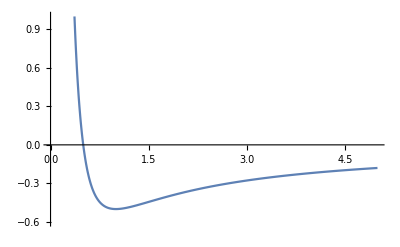

```mathematica
Plot[ Evaluate[(eq3pt14[[2]]  /. 𝓇[t]-> 𝓇  /. G-> 1 /. m-> 1 /. h-> 1 )] , {𝓇,0,5}, PlotRange-> {-0.6 , 1 }  ]
```

```mathematica
(* Try and remember how to do this chain rule *) 

Clear[eq3pt17a]
eq3pt17a = 
 𝓇[t] == 1/u[t]

eq3pt11
```

𝓇[t]==1/u[t]

-h^2/𝓇[t]^3+𝓇''[t]==-(G m)/𝓇[t]^2

```mathematica
D[ eq3pt17a  , t ]
```

𝓇'[t]==-u'[t]/u[t]^2

```mathematica
D[ eq3pt17a, t ]
```

𝓇'[t]==-u'[t]/u[t]^2

```mathematica
Clear[eq3pt17]
eq3pt17 = 
u''[t] + u[t]== (G m)/h^2
```

u[t]+u''[t]==(G m)/h^2

```mathematica
(* Too lazy to do the phase shift *) 

Flatten[DSolve[ eq3pt17  , u[t]  , t ] ][[1]]
```

u[t]→(G m)/h^2+C[1] Cos[t]+C[2] Sin[t]

```mathematica
Clear[eq3pt18]
eq3pt18 = 
u[t] == (G m)/h^2 ( 1 + ℯ Cos[ϕ[t]-ω] )
```

u[t]==(G m (1+ℯ Cos[ω-ϕ[t]]))/h^2

```mathematica
Clear[eq3pt20]
eq3pt20 = 
p == h^2/(G m)
```

p==h^2/(G m)

```mathematica
Flatten[Solve[ eq3pt20 , G ] ][[1]]
```

G→h^2/(m p)

```mathematica
eq3pt17a  /. ( eq3pt18  /. Equal-> Rule )
```

𝓇[t]==h^2/(G m (1+ℯ Cos[ω-ϕ[t]]))

```mathematica
Clear[eq3pt19]
eq3pt19 = 
eq3pt17a  /. ( eq3pt18  /. Equal-> Rule )   /. Flatten[Solve[ eq3pt20 , G ] ][[1]]
```

𝓇[t]==p/(1+ℯ Cos[ω-ϕ[t]])

```mathematica
Clear[eq3pt21]
eq3pt21 = {
Subscript[r, peri] == p/(1+ℯ), 
Subscript[r, apo] == p/(1-ℯ)
} ;
eq3pt21  // TableForm
```

r_peri==p/(1+ℯ)
r_apo==p/(1-ℯ)

```mathematica
Flatten[Solve[ eq3pt21  , {p,ℯ} ]] // TableForm
```

p→(2 r_apo r_peri)/(r_apo+r_peri)
ℯ→-(-r_apo+r_peri)/(r_apo+r_peri)

```mathematica
Clear[eq3pt22]
eq3pt22 = 
a ==( (  1/2( Subscript[r, peri] + Subscript[r, apo] ) /. (eq3pt21   /. Equal-> Rule ) )  // Expand  // Simplify  )
```

a==p/(1-ℯ^2)

```mathematica
Flatten[Solve[ eq3pt22  , p ]][[1]]
```

p→-a (-1+ℯ^2)

```mathematica
eq3pt10
( eq3pt19 /. Equal-> Rule )  
Flatten[Solve[eq3pt20 ,h]][[2]]
```

𝓇[t]^2 ϕ'[t]==h

𝓇[t]→p/(1+ℯ Cos[ω-ϕ[t]])

h→√G √m √p

```mathematica
Flatten[Solve[ eq3pt10 , ϕ'[t]]][[1]] 
Flatten[Solve[ eq3pt10 , ϕ'[t]]][[1]]  /. ( eq3pt19 /. Equal-> Rule  ) 

Clear[eq3pt25b]
eq3pt25b = 
( Flatten[Solve[ eq3pt10 , ϕ'[t]]][[1]]  /. ( eq3pt19 /. Equal-> Rule  )  /. (Flatten[Solve[eq3pt20 ,h]][[2]] ) )  /. Rule-> Equal
```

ϕ'[t]→h/𝓇[t]^2

ϕ'[t]→(h (1+ℯ Cos[ω-ϕ[t]])^2)/p^2

ϕ'[t]==(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)/p^(3/2)

```mathematica
D[ eq3pt19 , t ] 

Clear[eq3pt25a]
eq3pt25a= 
D[ eq3pt19 , t ]  /. (eq3pt25b  /. Equal-> Rule )
```

𝓇'[t]==-(p ℯ Sin[ω-ϕ[t]] ϕ'[t])/(1+ℯ Cos[ω-ϕ[t]])^2

𝓇'[t]==-(√G √m ℯ Sin[ω-ϕ[t]])/(√p)

```mathematica
𝓇'[t]^2+ 𝓇[t]^2 ϕ'[t]^2
```

𝓇'[t]^2+𝓇[t]^2 ϕ'[t]^2

```mathematica
( eq3pt19 /. Equal-> Rule )  
( eq3pt25a /. Equal-> Rule )
( eq3pt25b /. Equal-> Rule )
```

𝓇[t]→p/(1+ℯ Cos[ω-ϕ[t]])

𝓇'[t]→-(√G √m ℯ Sin[ω-ϕ[t]])/(√p)

ϕ'[t]→(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)/p^(3/2)

```mathematica
( 𝓇'[t]^2+ 𝓇[t]^2 ϕ'[t]^2 ) /. ( eq3pt25a /. Equal-> Rule ) /. ( eq3pt25b /. Equal-> Rule )   /. ( eq3pt19 /. Equal-> Rule )
```

(G m (1+ℯ Cos[ω-ϕ[t]])^2)/p+(G m ℯ^2 Sin[ω-ϕ[t]]^2)/p

```mathematica
Clear[eq3pt26a]
eq3pt26a = 
v^2== ( ( 𝓇'[t]^2+ 𝓇[t]^2 ϕ'[t]^2 ) /. ( eq3pt25a /. Equal-> Rule ) /. ( eq3pt25b /. Equal-> Rule )   /. ( eq3pt19 /. Equal-> Rule )  )   //   TrigExpand  // FullSimplify
```

v^2==(G m (1+ℯ^2+2 ℯ Cos[ω-ϕ[t]]))/p

```mathematica
( Flatten[Solve[ ( eq3pt19  /. ( Cos[ω-ϕ[t]]-> β )  ), β ]][[1]]  /. β-> Cos[ω-ϕ[t]] )
```

Cos[ω-ϕ[t]]→(p-𝓇[t])/(ℯ 𝓇[t])

```mathematica
Clear[eq3pt26b]
eq3pt26b = 
v^2== Collect[ ( eq3pt26a  /. ( Flatten[Solve[ ( eq3pt19  /. ( Cos[ω-ϕ[t]]-> β )  ), β ]][[1]]  /. β-> Cos[ω-ϕ[t]] )  // Expand  ) , G m ]
```

v^2==(v^2==G m (-1/p+ℯ^2/p+2/𝓇[t]))

```mathematica
Clear[eq3pt26]
eq3pt26 =  { 
eq3pt26a  , 
eq3pt26b 
} ;
eq3pt26  // TableForm
```

v^2==(G m (1+ℯ^2+2 ℯ Cos[ω-ϕ[t]]))/p
v^2==(v^2==G m (-1/p+ℯ^2/p+2/𝓇[t]))

```mathematica
eq3pt26[[2]]
eq3pt26[[2]][[2]]
Sqrt[ eq3pt26[[2]][[2]] ] 
eq3pt12
```

v^2==(v^2==G m (-1/p+ℯ^2/p+2/𝓇[t]))

v^2==G m (-1/p+ℯ^2/p+2/𝓇[t])

√(v^2==G m (-1/p+ℯ^2/p+2/𝓇[t]))

h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]+1/2 𝓇'[t]^2==ε

```mathematica
(* remember, on the lhs of 3.22 you have kinetic minus potential *) 

Flatten[Solve[eq3pt20, h ]][[2]] 
Flatten[Solve[ eq3pt22, p ]][[1]] 
eq3pt12
eq3pt12[[1]]
eq3pt26[[2]]
eq3pt26[[2]][[2]]
```

h→√G √m √p

p→-a (-1+ℯ^2)

h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]+1/2 𝓇'[t]^2==ε

h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]+1/2 𝓇'[t]^2

v^2==(v^2==G m (-1/p+ℯ^2/p+2/𝓇[t]))

v^2==G m (-1/p+ℯ^2/p+2/𝓇[t])

```mathematica
Clear[eq3pt27a]
eq3pt27a = 
μ ( ( 1/2 eq3pt26[[2]][[2]] -(G m)/𝓇[t]  ) // Expand  // Simplify  )
```

μ (1/2 (v^2==G m ((-1+ℯ^2)/p+2/𝓇[t]))-(G m)/𝓇[t])

```mathematica
Clear[eq3pt27b]
eq3pt27b =
eq3pt27a /. Flatten[Solve[ eq3pt22, p ]][[1]]
```

μ (1/2 (v^2==G m (-1/a+2/𝓇[t]))-(G m)/𝓇[t])

```mathematica
eq3pt5
Flatten[Solve[eq3pt20, h ]][[2]] 

Clear[eq3pt28] (* Change to vector *) 
eq3pt28 = eq3pt5 /. Flatten[Solve[eq3pt20, h ]][[2]]
```

L==h μ

h→√G √m √p

L==√G √m √p μ

```mathematica
eq3pt25b
eq3pt25b /. ϕ'[t] -> (dϕ/dt) 

Clear[eq3pt29a]
eq3pt29a = 
( Flatten[Solve[ ( eq3pt25b /. ϕ'[t] -> (dϕ/dt)  ) , dt ] ][[1]]  ) /.Rule-> Equal
```

ϕ'[t]==(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)/p^(3/2)

dϕ/dt==(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)/p^(3/2)

dt==(dϕ p^(3/2))/(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)

```mathematica
eq3pt29a[[1]] (* Integrate this *) 
Coefficient[ ( eq3pt29a[[2]] /. ϕ[t]-> φ[t] )  , dϕ ] (* Integrate this *)
```

dt

p^(3/2)/(√G √m (1+ℯ Cos[ω-φ[t]])^2)

```mathematica
(* get rid of time dependence in trig functions? This doesn't work, change this *) 

Clear[eq3pt29]
eq3pt29 = 
t- T == Inactive[ Integrate[ Coefficient[ ( eq3pt29a[[2]] /. ϕ[t]-> φ[t] )  , dϕ ] , {φ[t], ω,ϕ[t] } ] ]
```

t-T==Inactive[∫_ω^ϕ[t] Coefficient[eq3pt29a⟦2⟧/.ϕ[t]→φ[t],dϕ]ⅆφ[t]]

```mathematica
Clear[eq3pt30]
eq3pt30 = {
Cos[f] == (Cos[u]-ℯ)/(1 - ℯ Cos[u]) , 
Sin[f] == (√(1-ℯ^2)Sin[u])/(1 - ℯ Cos[u]) , 
f == ϕ- ω (* Make f and ϕ time dependent or leave? remember ω is constant of integration?  *) 
} ;
eq3pt30  // TableForm
```

Cos[f]==(-ℯ+Cos[u])/(1-ℯ Cos[u])
Sin[f]==(√(1-ℯ^2) Sin[u])/(1-ℯ Cos[u])
f==ϕ-ω

```mathematica
eq3pt30 /. Sin[u]-> α  /. Cos[u]-> β

Clear[eq3pt31]
eq3pt31 = 
( ( Flatten[Solve[ ( eq3pt30 /. Sin[u]-> α  /. Cos[u]-> β ) , {α,β} ]]  /. { α-> Sin[u] , β-> Cos[u] }  )  // Expand  // Simplify  ) /. Rule-> Equal
```

{Cos[f]==(-ℯ+β)/(1-ℯ β),Sin[f]==(√(1-ℯ^2) α)/(1-ℯ β),f==ϕ-ω}

{}

```mathematica
eq3pt30[[2]]
eq3pt30[[1]]

Numerator[ eq3pt30[[2]][[2]] ] 
Denominator[ eq3pt30[[2]][[2]] ] 
Numerator[ eq3pt30[[1]][[2]] ]
```

Sin[f]==(√(1-ℯ^2) Sin[u])/(1-ℯ Cos[u])

Cos[f]==(-ℯ+Cos[u])/(1-ℯ Cos[u])

√(1-ℯ^2) Sin[u]

1-ℯ Cos[u]

-ℯ+Cos[u]

```mathematica
(* Try to verify this later *) 

Clear[eq3pt31a] 
eq3pt31a = {
opp == Numerator[ eq3pt30[[2]][[2]] ]  , 
adj == Numerator[ eq3pt30[[1]][[2]] ]   , 
hyp == Denominator[ eq3pt30[[2]][[2]] ] 
}  /. Equal-> Rule ;
eq3pt31a  // TableForm
```

opp→√(1-ℯ^2) Sin[u]
adj→-ℯ+Cos[u]
hyp→1-ℯ Cos[u]

```mathematica
Clear[eq3pt32]
eq3pt32 =  { 
Tan[f/2] == √((1+ℯ)/(1-ℯ)) Tan[u/2] , 
Tan[f[u]/2] == √((1+ℯ)/(1-ℯ)) Tan[u/2] , 
Tan[u/2] == √((1+ℯ)/(1-ℯ)) Tan[u[f]/2]
} ;
eq3pt32  // TableForm
```

Tan[f/2]==√((1+ℯ)/(1-ℯ)) Tan[u/2]
Tan[f[u]/2]==√((1+ℯ)/(1-ℯ)) Tan[u/2]
Tan[u/2]==√((1+ℯ)/(1-ℯ)) Tan[u[f]/2]

```mathematica
(* Too tired to change the variables to do the appropriate differentiation *) 

D[ eq3pt32[[2]] , u ] 
Flatten[Solve[ D[ eq3pt32[[2]] , u ]  , f'[u] ] ][[1]]
```

1/2 Sec[f[u]/2]^2 f'[u]==1/2 √((1+ℯ)/(1-ℯ)) Sec[u/2]^2

f'[u]→√((-1-ℯ)/(-1+ℯ)) Cos[f[u]/2]^2 Sec[u/2]^2

```mathematica
(* Box 3.2 Page 153 Needed Before Equations 3.40 *) 
(* Poisson and Will Gravity page 153 *)

Clear[R1]
R1=
({{Cos[ω], -Sin[ω], 0}, {Sin[ω], Cos[ω], 0}, {0, 0, 1}});

Clear[R2]
R2 = 
({{1, 0, 0}, {0, Cos[ι], -Sin[ι]}, {0, Sin[ι], Cos[ι]}});

Clear[R3]
R3 = 
({{Cos[Ω], -Sin[Ω], 0}, {Sin[Ω], Cos[Ω], 0}, {0, 0, 1}});

Clear[𝓍]
𝓍 = { x ,  y , z }  ;

Clear[𝒳]
𝒳 = { X , Y , Z }  ;
```

```mathematica
R3 . R2 . R1 . 𝓍  // Expand // Simplify  // MatrixForm
```

(-y Cos[Ω] Sin[ω]+(z Sin[ι]-x Cos[ι] Sin[ω]) Sin[Ω]+Cos[ω] (x Cos[Ω]-y Cos[ι] Sin[Ω])
-z Cos[Ω] Sin[ι]+Cos[ι] Cos[Ω] (y Cos[ω]+x Sin[ω])+(x Cos[ω]-y Sin[ω]) Sin[Ω]
z Cos[ι]+Sin[ι] (y Cos[ω]+x Sin[ω]))

```mathematica
Clear[box3pt2a]
box3pt2a = { 
Collect[ Thread[ 𝒳 == (  R3 . R2 . R1 . 𝓍  // Expand // Simplify ) ][[1]]  , {x,y,z} ]  , 
Collect[ Thread[ 𝒳 == (  R3 . R2 . R1 . 𝓍  // Expand // Simplify ) ][[2]] , {x,y,z} ]  , 
Collect[ Thread[ 𝒳 == (  R3 . R2 . R1 . 𝓍  // Expand // Simplify ) ][[3]] ,{x,y,z} ] 
} ;
box3pt2a // TableForm
```

X==z Sin[ι] Sin[Ω]+y (-Cos[Ω] Sin[ω]-Cos[ι] Cos[ω] Sin[Ω])+x (Cos[ω] Cos[Ω]-Cos[ι] Sin[ω] Sin[Ω])
Y==-z Cos[Ω] Sin[ι]+x (Cos[ι] Cos[Ω] Sin[ω]+Cos[ω] Sin[Ω])+y (Cos[ι] Cos[ω] Cos[Ω]-Sin[ω] Sin[Ω])
Z==z Cos[ι]+y Cos[ω] Sin[ι]+x Sin[ι] Sin[ω]

```mathematica
Clear[box3pt2b]
box3pt2b= { 
x == r Cos[f] , 
y == r Sin[f] , 
z == 0
}  ;
box3pt2b /. Equal-> Rule  // TableForm
```

x→r Cos[f]
y→r Sin[f]
z→0

```mathematica
(* set these equal to basis vectors if needed and figure out why transpose  *) 

Clear[box3pt2d]
box3pt2d  = 
Transpose[Table[{ Coefficient[ box3pt2a[[i]][[2]], x ] ,Coefficient[ box3pt2a[[i]][[2]], y ] , Coefficient[ box3pt2a[[i]][[2]], z ]  } , {i,1,3}]]   ;
box3pt2d // MatrixForm
```

(Cos[ω] Cos[Ω]-Cos[ι] Sin[ω] Sin[Ω] | Cos[ι] Cos[Ω] Sin[ω]+Cos[ω] Sin[Ω] | Sin[ι] Sin[ω]
-Cos[Ω] Sin[ω]-Cos[ι] Cos[ω] Sin[Ω] | Cos[ι] Cos[ω] Cos[Ω]-Sin[ω] Sin[Ω] | Cos[ω] Sin[ι]
Sin[ι] Sin[Ω] | -Cos[Ω] Sin[ι] | Cos[ι])

```mathematica
box3pt2d [[1,1;;3]] /. ω-> ω+f (* needed for equation 3.42 *) 
box3pt2d [[2,1;;3]]  /. ω-> ω+f (* needed for equation 3.43 *)
```

{Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[f+ω]+Cos[f+ω] Sin[Ω],Sin[ι] Sin[f+ω]}

{-Cos[Ω] Sin[f+ω]-Cos[ι] Cos[f+ω] Sin[Ω],Cos[ι] Cos[f+ω] Cos[Ω]-Sin[f+ω] Sin[Ω],Cos[f+ω] Sin[ι]}

```mathematica
Clear[eq3pt40]
eq3pt40 = 
Flatten[Solve[ ( box3pt2a /. ( box3pt2b /. Equal-> Rule  ) ) , {X,Y,Z} ]] // Expand // FullSimplify   ;
eq3pt40// TableForm
```

X→r (Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω])
Y→r (Cos[ι] Cos[Ω] Sin[f+ω]+Cos[f+ω] Sin[Ω])
Z→r Sin[ι] Sin[f+ω]

```mathematica
Clear[eq3pt40a]
eq3pt40a = 
eq3pt40[[1]]
```

X→r (Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω])

```mathematica
Clear[eq3pt40b]
eq3pt40b = 
eq3pt40[[2]]
```

Y→r (Cos[ι] Cos[Ω] Sin[f+ω]+Cos[f+ω] Sin[Ω])

```mathematica
Clear[eq3pt40c]
eq3pt40c = 
eq3pt40[[3]]
```

Z→r Sin[ι] Sin[f+ω]

```mathematica
(* Not numbered *) 

Clear[eq3pt40d,p,ℯ]
eq3pt40d = 
( 𝓇[t] == p/(1+ ℯ Cos[f[t]])   ) /. Equal-> Rule
```

𝓇[t]→p/(1+ℯ Cos[f[t]])

```mathematica
(* Make time dependent? *) 

eq3pt30[[3]]  
eq3pt40d 
( ( eq3pt25a  /. Equal-> Rule  )  /.  ϕ[t]-> ( ω-f[t] ) )  
eq3pt40a[[2]] /. r-> 𝓇[t] /. f-> f[t] 
D[ ( eq3pt40a[[2]] /. r-> 𝓇[t] /. f-> f[t]  ) , t ]
```

f==ϕ-ω

𝓇[t]→p/(1+ℯ Cos[f[t]])

𝓇'[t]→-(√G √m ℯ Sin[f[t]])/(√p)

(Cos[Ω] Cos[ω+f[t]]-Cos[ι] Sin[Ω] Sin[ω+f[t]]) 𝓇[t]

𝓇[t] (-Cos[ι] Cos[ω+f[t]] Sin[Ω] f'[t]-Cos[Ω] Sin[ω+f[t]] f'[t])+(Cos[Ω] Cos[ω+f[t]]-Cos[ι] Sin[Ω] Sin[ω+f[t]]) 𝓇'[t]

```mathematica
D[ ( eq3pt40a[[2]] /. r-> 𝓇[t] /. f-> f[t]  ) , t ]  /. eq3pt40d
```

(p (-Cos[ι] Cos[ω+f[t]] Sin[Ω] f'[t]-Cos[Ω] Sin[ω+f[t]] f'[t]))/(1+ℯ Cos[f[t]])+(Cos[Ω] Cos[ω+f[t]]-Cos[ι] Sin[Ω] Sin[ω+f[t]]) 𝓇'[t]

```mathematica
Clear[eq3pt41a] (* No idea if this is right, but looks close *) 
eq3pt41a = 
( D[ ( eq3pt40a[[2]] /. r-> 𝓇[t] /. f-> f[t]  ) , t ]  /. eq3pt40d  ) /.( ( eq3pt25a  /. Equal-> Rule  )  /.  ϕ[t]-> ( ω-f[t] ) )   /. f'[t]-> 0  // FullSimplify
```

(√G √m ℯ Sin[f[t]] (-Cos[Ω] Cos[ω+f[t]]+Cos[ι] Sin[Ω] Sin[ω+f[t]]))/(√p)

```mathematica
Clear[eq3pt41b]
eq3pt41b = 
D[ ( eq3pt40b[[2]]/. r-> 𝓇[t] /. f-> f[t]  ) , t ]  /. f'[t]-> 0  /. ( ( eq3pt25a  /. Equal-> Rule  )  /.  ϕ[t]-> ( ω-f[t] ) )
```

-(√G √m ℯ Sin[f[t]] (Cos[ω+f[t]] Sin[Ω]+Cos[ι] Cos[Ω] Sin[ω+f[t]]))/(√p)

```mathematica
eq3pt40c[[2]] /. r-> 𝓇[t] /. f-> f[t]
D[ ( eq3pt40c[[2]] /. r-> 𝓇[t] /. f-> f[t] ) , t ]  /. f'[t]-> 0
```

Sin[ι] Sin[ω+f[t]] 𝓇[t]

Sin[ι] Sin[ω+f[t]] 𝓇'[t]

```mathematica
Clear[eq3pt41c]
eq3pt41c = 
D[ ( eq3pt40c[[2]] /. r-> 𝓇[t] /. f-> f[t] ) , t ]  /. f'[t]-> 0  /. ( ( eq3pt25a  /. Equal-> Rule  )  /.  ϕ[t]-> ( ω-f[t] ) )
```

-(√G √m ℯ Sin[ι] Sin[f[t]] Sin[ω+f[t]])/(√p)

```mathematica
box3pt2d[[1,1;;3]] /. ω-> ω+f
```

{Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[f+ω]+Cos[f+ω] Sin[Ω],Sin[ι] Sin[f+ω]}

```mathematica
Clear[eq3pt42] (* Do dot product with {eX,eY,eZ}  or leave implied? *) 
eq3pt42 = 
n == box3pt2d [[1,1;;3]] /. ω-> ω+f
```

n=={Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[f+ω]+Cos[f+ω] Sin[Ω],Sin[ι] Sin[f+ω]}

```mathematica
Clear[eq3pt43](* Do dot product with {eX,eY,eZ}  or leave implied? *)  
eq3pt43 = 
λ == box3pt2d [[2,1;;3]]  /. ω-> ω+f
```

λ=={-Cos[Ω] Sin[f+ω]-Cos[ι] Cos[f+ω] Sin[Ω],Cos[ι] Cos[f+ω] Cos[Ω]-Sin[f+ω] Sin[Ω],Cos[f+ω] Sin[ι]}

```mathematica
Clear[eq3pt44](* Do dot product with {eX,eY,eZ}  or leave implied? *)   
eq3pt44 = 
Subscript[e, x]== box3pt2d [[1,1;;3]]
```

e_x=={Cos[ω] Cos[Ω]-Cos[ι] Sin[ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[ω]+Cos[ω] Sin[Ω],Sin[ι] Sin[ω]}

```mathematica
Clear[eq3pt45](* Do dot product with {eX,eY,eZ}  or leave implied? *)   
eq3pt45 = 
Subscript[e, z]== box3pt2d [[3,1;;3]]
```

e_z=={Sin[ι] Sin[Ω],-Cos[Ω] Sin[ι],Cos[ι]}

```mathematica
(* Not listed in book but parameters are described *) 

Clear[eq3pt45a] 
eq3pt45a = { 
𝒜 == ℯ * ( Subscript[e, x] /. (eq3pt44  /. Equal-> Rule ) )  , 
𝒽 == h * ( Subscript[e, z] /. ( eq3pt45 /. Equal-> Rule ) )  , 
h^2 == G m p 
} ;
eq3pt45a  // TableForm
```

𝒜=={ℯ (Cos[ω] Cos[Ω]-Cos[ι] Sin[ω] Sin[Ω]),ℯ (Cos[ι] Cos[Ω] Sin[ω]+Cos[ω] Sin[Ω]),ℯ Sin[ι] Sin[ω]}
𝒽=={h Sin[ι] Sin[Ω],-h Cos[Ω] Sin[ι],h Cos[ι]}
h^2==G m p

```mathematica
(* Just checking to make sure these defintions work for later on *) 

𝒜 /. ( eq3pt45a [[1]] /. Equal-> Rule  ) 
𝒽 /. ( eq3pt45a [[2]] /. Equal-> Rule  )
```

{ℯ (Cos[ω] Cos[Ω]-Cos[ι] Sin[ω] Sin[Ω]),ℯ (Cos[ι] Cos[Ω] Sin[ω]+Cos[ω] Sin[Ω]),ℯ Sin[ι] Sin[ω]}

{h Sin[ι] Sin[Ω],-h Cos[Ω] Sin[ι],h Cos[ι]}

```mathematica
Clear[eq3pt46]
eq3pt46 = 
p == h^2/(G m)
```

p==h^2/(G m)

```mathematica
(* Change this to absolute value *) 

Clear[eq3pt46a]
eq3pt46a = 
ℯ == A
```

ℯ==A

```mathematica
Clear[eq3pt46b]
eq3pt46b =
```

```mathematica
Clear[eq3pt107]
eq3pt107 = 
n1 == { Cos[Ω1 t] , Sin[Ω1 t], 0} /. Equal-> Rule
```

n1→{Cos[t Ω1],Sin[t Ω1],0}

```mathematica
Clear[eq3pt108]
eq3pt108 = 
n2 == { Cos[Ω2 t+ψ] , Sin[Ω2 t+ψ], 0} /. Equal-> Rule
```

n2→{Cos[ψ+t Ω2],Sin[ψ+t Ω2],0}

```mathematica
Clear[eq3pt109]
eq3pt109 = 
e == { Sin[α] Cos[β] , Sin[α] Sin[β] , Cos[α] }  /. Equal-> Rule
```

e→{Cos[β] Sin[α],Sin[α] Sin[β],Cos[α]}

```mathematica
Clear[eq3pt106]
eq3pt106 = 
(* consant in front *) ( (m1/r1^3)( e  . n1 ) Cross[e,n1] +(m2/r2^3)  ( e  . n2 ) Cross[e,n2] /. eq3pt109 /. eq3pt108 /. eq3pt107 ) // Expand // Simplify
```

{{(Sin[2 α] (-((m2 r1^3+m1 r2^3) Sin[β])+m1 r2^3 Sin[β-2 t Ω1]+m2 r1^3 Sin[β-2 (ψ+t Ω2)]))/(4 r1^3 r2^3),(Sin[2 α] (m1 r2^3 Cos[β]+m1 r2^3 Cos[β-2 t Ω1]+m2 r1^3 (-Sin[β]+Sin[β-2 (ψ+t Ω2)])))/(4 r1^3 r2^3),-(Sin[α] (-m1 r2^3 Cos[α+2 β-2 t Ω1]+m1 r2^3 Cos[α-2 β+2 t Ω1]+4 m2 r1^3 Cos[α] Cos[β-ψ-t Ω2] Sin[ψ+t Ω2]))/(4 r1^3 r2^3)},{(Sin[2 α] (m2 r1^3 Cos[β]+m2 r1^3 Cos[β-2 (ψ+t Ω2)]-2 m1 r2^3 Cos[β-t Ω1] Sin[t Ω1]))/(4 r1^3 r2^3),(((m2 r1^3+m1 r2^3) Cos[β]+m1 r2^3 Cos[β-2 t Ω1]+m2 r1^3 Cos[β-2 (ψ+t Ω2)]) Sin[2 α])/(4 r1^3 r2^3),((m2 r1^3 Cos[α-β]+m2 r1^3 Cos[α+β]+m1 r2^3 Cos[α+2 β-2 t Ω1]-m1 r2^3 Cos[α-2 β+2 t Ω1]+m2 r1^3 Cos[α-β+2 ψ+2 t Ω2]+m2 r1^3 Cos[α+β-2 (ψ+t Ω2)]) Sin[α])/(4 r1^3 r2^3)},{(Sin[α] (m2 r1^3 Cos[α+2 β-2 ψ-2 t Ω2]-m2 r1^3 Cos[α+2 (-β+ψ+t Ω2)]-4 m1 r2^3 Cos[α] Cos[β-t Ω1] Sin[t Ω1]))/(4 r1^3 r2^3),((m1 r2^3 Cos[α-β]+m1 r2^3 Cos[α+β]+m1 r2^3 Cos[α+β-2 t Ω1]+m1 r2^3 Cos[α-β+2 t Ω1]+m2 r1^3 Cos[α+2 β-2 ψ-2 t Ω2]-m2 r1^3 Cos[α-2 β+2 ψ+2 t Ω2]) Sin[α])/(4 r1^3 r2^3),-(Sin[α]^2 (m1 r2^3 Sin[2 (β-t Ω1)]+m2 r1^3 Sin[2 β-2 ψ-2 t Ω2]))/(2 r1^3 r2^3)}}

```mathematica
eq3pt106[[1]]
```

{(Sin[2 α] (-((m2 r1^3+m1 r2^3) Sin[β])+m1 r2^3 Sin[β-2 t Ω1]+m2 r1^3 Sin[β-2 (ψ+t Ω2)]))/(4 r1^3 r2^3),(Sin[2 α] (m1 r2^3 Cos[β]+m1 r2^3 Cos[β-2 t Ω1]+m2 r1^3 (-Sin[β]+Sin[β-2 (ψ+t Ω2)])))/(4 r1^3 r2^3),-(Sin[α] (-m1 r2^3 Cos[α+2 β-2 t Ω1]+m1 r2^3 Cos[α-2 β+2 t Ω1]+4 m2 r1^3 Cos[α] Cos[β-ψ-t Ω2] Sin[ψ+t Ω2]))/(4 r1^3 r2^3)}

```mathematica
eq3pt106[[2]]
```

{(Sin[2 α] (m2 r1^3 Cos[β]+m2 r1^3 Cos[β-2 (ψ+t Ω2)]-2 m1 r2^3 Cos[β-t Ω1] Sin[t Ω1]))/(4 r1^3 r2^3),(((m2 r1^3+m1 r2^3) Cos[β]+m1 r2^3 Cos[β-2 t Ω1]+m2 r1^3 Cos[β-2 (ψ+t Ω2)]) Sin[2 α])/(4 r1^3 r2^3),((m2 r1^3 Cos[α-β]+m2 r1^3 Cos[α+β]+m1 r2^3 Cos[α+2 β-2 t Ω1]-m1 r2^3 Cos[α-2 β+2 t Ω1]+m2 r1^3 Cos[α-β+2 ψ+2 t Ω2]+m2 r1^3 Cos[α+β-2 (ψ+t Ω2)]) Sin[α])/(4 r1^3 r2^3)}

```mathematica
eq3pt106[[3]]
```

{(Sin[α] (m2 r1^3 Cos[α+2 β-2 ψ-2 t Ω2]-m2 r1^3 Cos[α+2 (-β+ψ+t Ω2)]-4 m1 r2^3 Cos[α] Cos[β-t Ω1] Sin[t Ω1]))/(4 r1^3 r2^3),((m1 r2^3 Cos[α-β]+m1 r2^3 Cos[α+β]+m1 r2^3 Cos[α+β-2 t Ω1]+m1 r2^3 Cos[α-β+2 t Ω1]+m2 r1^3 Cos[α+2 β-2 ψ-2 t Ω2]-m2 r1^3 Cos[α-2 β+2 ψ+2 t Ω2]) Sin[α])/(4 r1^3 r2^3),-(Sin[α]^2 (m1 r2^3 Sin[2 (β-t Ω1)]+m2 r1^3 Sin[2 β-2 ψ-2 t Ω2]))/(2 r1^3 r2^3)}

```mathematica
Clear[m]
m = { m1,m2,m3}
```

{m1,m2,m3}

```mathematica
Clear[v]
v = {v1,v2,v3}
```

{v1,v2,v3}

```mathematica
Clear[eq3pt112a]
eq3pt112a = 
Sum[ m[[i]] v[[i]] , {i,1,3} ]
```

m1 v1+m2 v2+m3 v3

```mathematica
(* r is really a list of three vectors each of which has three components *)

Clear[eq3pt112b]
eq3pt112b = 
Inactive[Sum[ [Cross[r[[i]], v[[i]] ]], {i,1,3} ] ]
```

```mathematica
?Mod

Clear[eq3pt112c]
eq3pt112c = 
Sum[ (1/2)m[[i]]  v[[i]]^2 -(g m[[ Mod[i,3,1] ]] m[[ Mod[i+1,3,1] ]])/(𝓇  [Mod[i,3,1]][  Mod[i+1,3,1] ]) , {i,1,3} ]
```

(m1 v1^2)/2+(m2 v2^2)/2+(m3 v3^2)/2-(g m1 m2)/(𝓇[1][2])-(g m2 m3)/(𝓇[2][3])-(g m1 m3)/(𝓇[3][1])

```mathematica
Clear[eq3pt144a]
eq3pt144a = { 
x[t] == r[t] Sin[θ[t]] Cos[ϕ[t]] , 
y[t] == r[t] Sin[θ[t]] Sin[ϕ[t]] , 
z[t] == r[t] Cos[θ[t]] 
} /. Equal-> Rule  ;
eq3pt144a // TableForm
```

x[t]→Cos[ϕ[t]] r[t] Sin[θ[t]]
y[t]→r[t] Sin[θ[t]] Sin[ϕ[t]]
z[t]→Cos[θ[t]] r[t]

```mathematica
(* put potential in, then leave r[t] or change both to just r? *) 

Clear[m] 
Clear[eq3pt145a]
eq3pt145a = 
L == 1/2 μ(x'[t]^2+ y'[t]^2+ z'[t]^2)   (* + (G μ m)/r *)
```

L==1/2 μ (x'[t]^2+y'[t]^2+z'[t]^2)

```mathematica
D[ eq3pt144a , t ]  // TableForm
```

x'[t]→Cos[ϕ[t]] Sin[θ[t]] r'[t]+Cos[θ[t]] Cos[ϕ[t]] r[t] θ'[t]-r[t] Sin[θ[t]] Sin[ϕ[t]] ϕ'[t]
y'[t]→Sin[θ[t]] Sin[ϕ[t]] r'[t]+Cos[θ[t]] r[t] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] r[t] Sin[θ[t]] ϕ'[t]
z'[t]→Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t]

```mathematica
(* put potential in, then leave r[t] or change both to just r? *) 

eq3pt145a[[2]] 
eq3pt145a[[2]]  /. D[ eq3pt144a , t ]  // Expand // Simplify
```

1/2 μ (x'[t]^2+y'[t]^2+z'[t]^2)

1/2 μ (r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))

```mathematica
(* put potential in, then leave r[t] or change both to just r? *) 


eq3pt146 = 
Clear[eq3pt146] 
eq3pt145a[[2]]  /. D[ eq3pt144a , t ]   /. θ[t]-> π/2 /. θ'[t] -> 0  // Expand // Simplify
```

1/2 μ (r'[t]^2+r[t]^2 ϕ'[t]^2)

```mathematica
Clear[exercise3pt1]
exercise3pt1 = { 
𝓍 == r Cos[ϕ] + p α , 
𝓎 == r Sin[ϕ] , 
r == p/(1+ ℯ Cos[ϕ])
}  /. Equal-> Rule ;
exercise3pt1  // TableForm
```

{x,y,z}→p α+r Cos[ϕ]
𝓎→r Sin[ϕ]
r→p/(1+ℯ Cos[ϕ])

```mathematica
Clear[exercise3pt1a]
exercise3pt1a = 
(𝓍/A)^2+ (𝓎/B)^2 == 1
```

{x^2/A^2+𝓎^2/B^2,y^2/A^2+𝓎^2/B^2,z^2/A^2+𝓎^2/B^2}==1

```mathematica
exercise3pt1a 
exercise3pt1a  /. exercise3pt1[[1]]
exercise3pt1a  /. exercise3pt1[[1]] /. exercise3pt1[[2]]

Clear[exercise3pt1b]
exercise3pt1b = 
exercise3pt1a  /. exercise3pt1[[1]] /. exercise3pt1[[2]] /. exercise3pt1[[3]]
```

{x^2/A^2+𝓎^2/B^2,y^2/A^2+𝓎^2/B^2,z^2/A^2+𝓎^2/B^2}==1

{x^2/A^2+𝓎^2/B^2,y^2/A^2+𝓎^2/B^2,z^2/A^2+𝓎^2/B^2}==1

{x^2/A^2+(r^2 Sin[ϕ]^2)/B^2,y^2/A^2+(r^2 Sin[ϕ]^2)/B^2,z^2/A^2+(r^2 Sin[ϕ]^2)/B^2}==1

{x^2/A^2+(p^2 Sin[ϕ]^2)/(B^2 (1+ℯ Cos[ϕ])^2),y^2/A^2+(p^2 Sin[ϕ]^2)/(B^2 (1+ℯ Cos[ϕ])^2),z^2/A^2+(p^2 Sin[ϕ]^2)/(B^2 (1+ℯ Cos[ϕ])^2)}==1

```mathematica
exercise3pt1b
```

{x^2/A^2+(p^2 Sin[ϕ]^2)/(B^2 (1+ℯ Cos[ϕ])^2),y^2/A^2+(p^2 Sin[ϕ]^2)/(B^2 (1+ℯ Cos[ϕ])^2),z^2/A^2+(p^2 Sin[ϕ]^2)/(B^2 (1+ℯ Cos[ϕ])^2)}==1

## Line Element and Metric 5.156: Spherically Symmetric Spacetime

```mathematica
Clear[eq5pt156]
eq5pt156 = 
-c^2 Exp[-2 Φ/c^2] dt^2 + Exp[2Λ/c^2] dr^2+ r^2(dθ^2+ Sin[θ]^2 dϕ^2)
```

dr^2 ⅇ^((2 Λ)/c^2)-c^2 dt^2 ⅇ^(-(2 Φ)/c^2)+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
lineToMetric[eq5pt156 ,{dt,dr,dθ,dϕ}]  // MatrixForm // pdConv
```

(-c^2 ⅇ^(-(2 Φ)/c^2) | 0 | 0 | 0
0 | ⅇ^((2 Λ)/c^2) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

```mathematica
Clear[eq5pt156a]
eq5pt156a = {
Φ-> Φ[t,r] , 
Λ-> Λ[t,r]
} ;
eq5pt156a
```

{Φ→Φ[t,r],Λ→Λ[t,r]}

```mathematica
Clear[metric5pt156]
metric5pt156 = 
lineToMetric[eq5pt156  /. eq5pt156a ,{dt,dr,dθ,dϕ}] ;
metric5pt156  // MatrixForm // pdConv
```

(-c^2 ⅇ^(-(2 Φ(t,r))/c^2) | 0 | 0 | 0
0 | ⅇ^((2 Λ(t,r))/c^2) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

```mathematica
Clear[eq5pt158a]
eq5pt158a = 
Exp[-2Λ/c^2] == f[t,r]  /. eq5pt156a
```

ⅇ^(-(2 Λ[t,r])/c^2)==f[t,r]

```mathematica
Clear[lambdaReplace]
lambdaReplace = 
Flatten[Solve[eq5pt158a ,Λ[t,r]]][[1]] /. C[1]-> 0  // PowerExpand
```

Λ[t,r]→-1/2 c^2 Log[f[t,r]]

```mathematica
Clear[lambdaDerivatives]
lambdaDerivatives = { 
lambdaReplace , 
D[lambdaReplace ,t] , 
D[lambdaReplace ,r] , 
D[lambdaReplace ,{t,2}] , 
D[lambdaReplace ,{r,2}] , 
D[D[lambdaReplace ,t],r]
} // Expand // Simplify  // Expand ;
lambdaDerivatives // TableForm // pdConv
```

Λ(t,r)→-1/2 c^2 log(f(t,r))
(∂Λ(t,r))/(∂t)→-(c^2 (∂f(t,r))/(∂t))/(2 f(t,r))
(∂Λ(t,r))/(∂r)→-(c^2 (∂f(t,r))/(∂r))/(2 f(t,r))
(∂^2 Λ(t,r))/(∂t^2)→(c^2 ((∂f(t,r))/(∂t))^2)/(2 (f(t,r))^2)-(c^2 (∂^2 f(t,r))/(∂t^2))/(2 f(t,r))
(∂^2 Λ(t,r))/(∂r^2)→(c^2 ((∂f(t,r))/(∂r))^2)/(2 (f(t,r))^2)-(c^2 (∂^2 f(t,r))/(∂r^2))/(2 f(t,r))
(∂^2 Λ(t,r))/(∂t ∂r)→(c^2 (∂f(t,r))/(∂r) (∂f(t,r))/(∂t))/(2 (f(t,r))^2)-(c^2 (∂^2 f(t,r))/(∂t ∂r))/(2 f(t,r))

```mathematica
Clear[eq5pt158b]
eq5pt158b = 
f[t,r] == 1 - (2 G m[t,r])/(c^2 r)
```

f[t,r]==1-(2 G m[t,r])/(c^2 r)

```mathematica
Clear[fDerivatives]
fDerivatives = { 
eq5pt158b  , 
D[eq5pt158b ,t] , 
D[eq5pt158b ,r] , 
D[eq5pt158b ,{t,2}] , 
D[eq5pt158b ,{r,2}] , 
D[D[eq5pt158b ,t],r]
} /. Equal-> Rule // Expand // Simplify // Expand ;
fDerivatives  // TableForm // pdConv
```

f(t,r)→1-(2 G m(t,r))/(c^2 r)
(∂f(t,r))/(∂t)→-(2 G (∂m(t,r))/(∂t))/(c^2 r)
(∂f(t,r))/(∂r)→(2 G m(t,r))/(c^2 r^2)-(2 G (∂m(t,r))/(∂r))/(c^2 r)
(∂^2 f(t,r))/(∂t^2)→-(2 G (∂^2 m(t,r))/(∂t^2))/(c^2 r)
(∂^2 f(t,r))/(∂r^2)→-(4 G m(t,r))/(c^2 r^3)-(2 G (∂^2 m(t,r))/(∂r^2))/(c^2 r)+(4 G (∂m(t,r))/(∂r))/(c^2 r^2)
(∂^2 f(t,r))/(∂t ∂r)→(2 G (∂m(t,r))/(∂t))/(c^2 r^2)-(2 G (∂^2 m(t,r))/(∂t ∂r))/(c^2 r)

## Calculation of Tensors Associated With Metric 5.156: Spherically Symmetric Spacetime

```mathematica
Clear[input5pt156] 
input5pt156[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList5pt156];
tensorList5pt156 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList5pt156[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList5pt156[[2]]  = 
ChristoffelSymbol[ tensorList5pt156[[1]] , ActWith-> Simplify] ;
tensorList5pt156[[3]] = 
RiemannTensor[ tensorList5pt156[[1]] , ActWithNested-> Simplify ];
tensorList5pt156[[4]] = 
RicciTensor[ tensorList5pt156[[1]] , ActWith-> Simplify ] ;
tensorList5pt156[[5]] = 
RicciScalar[ tensorList5pt156[[1]] , ActWith-> Simplify ] ;
tensorList5pt156[[6]] = 
KretschmannScalar[ tensorList5pt156[[1]] , ActWith-> Simplify] ; 
tensorList5pt156[[7]] = 
EinsteinTensor[ tensorList5pt156[[1]] , ActWith-> Simplify] ;  
tensorList5pt156[[8]] = 
WeylTensor[ tensorList5pt156[[1]] , ActWith-> Simplify ] ;
 tensorList5pt156[[9]] = 
CottonTensor[ tensorList5pt156[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 7.35 for all tensors *) 
input5pt156[ "metric5pt156", metric5pt156, "SphericallytSymmetric","g^sph",{t,r,θ,ϕ}, "Greek"] // Timing
```

{2.37155,Null}

```mathematica
tensorList5pt156
```

{(g^sph)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList5pt156[[1]] 
TensorName[tensorList5pt156[[1]]] 
TensorValues[tensorList5pt156[[1]]] // MatrixForm // pdConv
TensorValues[tensorList5pt156[[1]]]  /. lambdaDerivatives  // MatrixForm // pdConv
TensorValues[tensorList5pt156[[1]]]  /. lambdaDerivatives  /. fDerivatives // MatrixForm // pdConv
```

(g^sph)_αβ^

SphericallytSymmetric

(-c^2 ⅇ^(-(2 Φ(t,r))/c^2) | 0 | 0 | 0
0 | ⅇ^((2 Λ(t,r))/c^2) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

(-c^2 ⅇ^(-(2 Φ(t,r))/c^2) | 0 | 0 | 0
0 | 1/(f(t,r)) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

(-c^2 ⅇ^(-(2 Φ(t,r))/c^2) | 0 | 0 | 0
0 | 1/(1-(2 G m(t,r))/(c^2 r)) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

```mathematica
tensorList5pt156[[2]] 
TensorName[tensorList5pt156[[2]]] 
TensorValues[tensorList5pt156[[2]]] // MatrixForm // pdConv
TensorValues[tensorList5pt156[[2]]]  /. lambdaDerivatives   // Expand //Simplify // MatrixForm // pdConv
TensorValues[tensorList5pt156[[2]]]  /. lambdaDerivatives  /. fDerivatives // Expand //Simplify // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSphericallytSymmetric

((-((∂Φ(t,r))/(∂t))/c^2
-((∂Φ(t,r))/(∂r))/c^2
0
0) | (-((∂Φ(t,r))/(∂r))/c^2
((∂Λ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2))/c^4
0
0) | (0
0
0
0) | (0
0
0
0)
((∂Φ(t,r))/(∂r) (-ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2))
((∂Λ(t,r))/(∂t))/c^2
0
0) | (((∂Λ(t,r))/(∂t))/c^2
((∂Λ(t,r))/(∂r))/c^2
0
0) | (0
0
r (-ⅇ^(-(2 Λ(t,r))/c^2))
0) | (0
0
0
r sin^2(θ) (-ⅇ^(-(2 Λ(t,r))/c^2)))
(0
0
0
0) | (0
0
1/r
0) | (0
1/r
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
0) | (0
0
0
1/r) | (0
0
0
cot(θ)) | (0
1/r
cot(θ)
0))

((-((∂Φ(t,r))/(∂t))/c^2
-((∂Φ(t,r))/(∂r))/c^2
0
0) | (-((∂Φ(t,r))/(∂r))/c^2
-(ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t))/(2 c^2 (f(t,r))^2)
0
0) | (0
0
0
0) | (0
0
0
0)
(f(t,r) (-ⅇ^(-(2 Φ(t,r))/c^2)) (∂Φ(t,r))/(∂r)
-((∂f(t,r))/(∂t))/(2 f(t,r))
0
0) | (-((∂f(t,r))/(∂t))/(2 f(t,r))
-((∂f(t,r))/(∂r))/(2 f(t,r))
0
0) | (0
0
-r f(t,r)
0) | (0
0
0
-r sin^2(θ) f(t,r))
(0
0
0
0) | (0
0
1/r
0) | (0
1/r
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
0) | (0
0
0
1/r) | (0
0
0
cot(θ)) | (0
1/r
cot(θ)
0))

((-((∂Φ(t,r))/(∂t))/c^2
-((∂Φ(t,r))/(∂r))/c^2
0
0) | (-((∂Φ(t,r))/(∂r))/c^2
(G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t))/((c^2 r-2 G m(t,r))^2)
0
0) | (0
0
0
0) | (0
0
0
0)
(-ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) (1-(2 G m(t,r))/(c^2 r))
(G (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r))
0
0) | ((G (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r))
(G (r (∂m(t,r))/(∂r)-m(t,r)))/(r (c^2 r-2 G m(t,r)))
0
0) | (0
0
(2 G m(t,r))/c^2-r
0) | (0
0
0
sin^2(θ) ((2 G m(t,r))/c^2-r))
(0
0
0
0) | (0
0
1/r
0) | (0
1/r
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
0) | (0
0
0
1/r) | (0
0
0
cot(θ)) | (0
1/r
cot(θ)
0))

```mathematica
tensorList5pt156[[3]] 
TensorName[tensorList5pt156[[3]]] 
TensorValues[tensorList5pt156[[3]]] // MatrixForm // pdConv
TensorValues[tensorList5pt156[[3]]]  /. lambdaDerivatives  // Expand //Simplify // MatrixForm // pdConv
TensorValues[tensorList5pt156[[3]]]  /. lambdaDerivatives  /. fDerivatives // Expand //Simplify // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSphericallytSymmetric

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (ⅇ^(-(2 Φ(t,r))/c^2) (c^4 (-(∂^2 Φ(t,r))/(∂r^2))-c^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 (∂Λ(t,r))/(∂r) (∂Φ(t,r))/(∂r)-((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-(∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 ((∂Φ(t,r))/(∂r))^2))/c^4 | 0 | 0
-(ⅇ^(-(2 Φ(t,r))/c^2) (c^4 (-(∂^2 Φ(t,r))/(∂r^2))-c^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 (∂Λ(t,r))/(∂r) (∂Φ(t,r))/(∂r)-((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-(∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 ((∂Φ(t,r))/(∂r))^2))/c^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r (∂Φ(t,r))/(∂r) (-ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2)) | 0
0 | 0 | (r (∂Λ(t,r))/(∂t))/c^2 | 0
r (∂Φ(t,r))/(∂r) ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) | -(r (∂Λ(t,r))/(∂t))/c^2 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | r sin^2(θ) (∂Φ(t,r))/(∂r) (-ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2))
0 | 0 | 0 | (r sin^2(θ) (∂Λ(t,r))/(∂t))/c^2
0 | 0 | 0 | 0
r sin^2(θ) (∂Φ(t,r))/(∂r) ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) | -(r sin^2(θ) (∂Λ(t,r))/(∂t))/c^2 | 0 | 0)
(0 | -(ⅇ^(-(2 Φ(t,r))/c^2) (c^4 (-(∂^2 Φ(t,r))/(∂r^2))-c^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 (∂Λ(t,r))/(∂r) (∂Φ(t,r))/(∂r)-((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-(∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 ((∂Φ(t,r))/(∂r))^2))/c^4 | 0 | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (c^4 (-(∂^2 Φ(t,r))/(∂r^2))-c^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 (∂Λ(t,r))/(∂r) (∂Φ(t,r))/(∂r)-((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-(∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 ((∂Φ(t,r))/(∂r))^2))/c^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (r (∂Λ(t,r))/(∂t))/c^2 | 0
0 | 0 | (r (∂Λ(t,r))/(∂r))/c^2 | 0
-(r (∂Λ(t,r))/(∂t))/c^2 | -(r (∂Λ(t,r))/(∂r))/c^2 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (r sin^2(θ) (∂Λ(t,r))/(∂t))/c^2
0 | 0 | 0 | (r sin^2(θ) (∂Λ(t,r))/(∂r))/c^2
0 | 0 | 0 | 0
-(r sin^2(θ) (∂Λ(t,r))/(∂t))/c^2 | -(r sin^2(θ) (∂Λ(t,r))/(∂r))/c^2 | 0 | 0)
(0 | 0 | r (∂Φ(t,r))/(∂r) ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) | 0
0 | 0 | -(r (∂Λ(t,r))/(∂t))/c^2 | 0
r (∂Φ(t,r))/(∂r) (-ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2)) | (r (∂Λ(t,r))/(∂t))/c^2 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(r (∂Λ(t,r))/(∂t))/c^2 | 0
0 | 0 | -(r (∂Λ(t,r))/(∂r))/c^2 | 0
(r (∂Λ(t,r))/(∂t))/c^2 | (r (∂Λ(t,r))/(∂r))/c^2 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | r^2 sin^2(θ) (1-ⅇ^(-(2 Λ(t,r))/c^2))
0 | 0 | -(r^2 sin^2(θ) (1-ⅇ^(-(2 Λ(t,r))/c^2))) | 0)
(0 | 0 | 0 | r sin^2(θ) (∂Φ(t,r))/(∂r) ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2)
0 | 0 | 0 | -(r sin^2(θ) (∂Λ(t,r))/(∂t))/c^2
0 | 0 | 0 | 0
r sin^2(θ) (∂Φ(t,r))/(∂r) (-ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2)) | (r sin^2(θ) (∂Λ(t,r))/(∂t))/c^2 | 0 | 0) | (0 | 0 | 0 | -(r sin^2(θ) (∂Λ(t,r))/(∂t))/c^2
0 | 0 | 0 | -(r sin^2(θ) (∂Λ(t,r))/(∂r))/c^2
0 | 0 | 0 | 0
(r sin^2(θ) (∂Λ(t,r))/(∂t))/c^2 | (r sin^2(θ) (∂Λ(t,r))/(∂r))/c^2 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(r^2 sin^2(θ) (1-ⅇ^(-(2 Λ(t,r))/c^2)))
0 | 0 | r^2 sin^2(θ) (1-ⅇ^(-(2 Λ(t,r))/c^2)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/4 ((2 (((∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))/c^2+(∂^2 f(t,r))/(∂t^2)))/(f(t,r))^2-(2 ⅇ^(-(2 Φ(t,r))/c^2) (∂f(t,r))/(∂r) (∂Φ(t,r))/(∂r))/(f(t,r))+(4 ⅇ^(-(2 Φ(t,r))/c^2) (((∂Φ(t,r))/(∂r))^2-c^2 (∂^2 Φ(t,r))/(∂r^2)))/c^2-(3 ((∂f(t,r))/(∂t))^2)/(f(t,r))^3) | 0 | 0
1/4 ((-(2 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))/c^2-2 (∂^2 f(t,r))/(∂t^2))/(f(t,r))^2+(2 ⅇ^(-(2 Φ(t,r))/c^2) (∂f(t,r))/(∂r) (∂Φ(t,r))/(∂r))/(f(t,r))+(4 ⅇ^(-(2 Φ(t,r))/c^2) (c^2 (∂^2 Φ(t,r))/(∂r^2)-((∂Φ(t,r))/(∂r))^2))/c^2+(3 ((∂f(t,r))/(∂t))^2)/(f(t,r))^3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r f(t,r) (-ⅇ^(-(2 Φ(t,r))/c^2)) (∂Φ(t,r))/(∂r) | 0
0 | 0 | -(r (∂f(t,r))/(∂t))/(2 f(t,r)) | 0
r f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) | (r (∂f(t,r))/(∂t))/(2 f(t,r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | r sin^2(θ) f(t,r) (-ⅇ^(-(2 Φ(t,r))/c^2)) (∂Φ(t,r))/(∂r)
0 | 0 | 0 | -(r sin^2(θ) (∂f(t,r))/(∂t))/(2 f(t,r))
0 | 0 | 0 | 0
r sin^2(θ) f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) | (r sin^2(θ) (∂f(t,r))/(∂t))/(2 f(t,r)) | 0 | 0)
(0 | 1/4 ((-(2 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))/c^2-2 (∂^2 f(t,r))/(∂t^2))/(f(t,r))^2+(2 ⅇ^(-(2 Φ(t,r))/c^2) (∂f(t,r))/(∂r) (∂Φ(t,r))/(∂r))/(f(t,r))+(4 ⅇ^(-(2 Φ(t,r))/c^2) (c^2 (∂^2 Φ(t,r))/(∂r^2)-((∂Φ(t,r))/(∂r))^2))/c^2+(3 ((∂f(t,r))/(∂t))^2)/(f(t,r))^3) | 0 | 0
1/4 ((2 (((∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))/c^2+(∂^2 f(t,r))/(∂t^2)))/(f(t,r))^2-(2 ⅇ^(-(2 Φ(t,r))/c^2) (∂f(t,r))/(∂r) (∂Φ(t,r))/(∂r))/(f(t,r))+(4 ⅇ^(-(2 Φ(t,r))/c^2) (((∂Φ(t,r))/(∂r))^2-c^2 (∂^2 Φ(t,r))/(∂r^2)))/c^2-(3 ((∂f(t,r))/(∂t))^2)/(f(t,r))^3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(r (∂f(t,r))/(∂t))/(2 f(t,r)) | 0
0 | 0 | -(r (∂f(t,r))/(∂r))/(2 f(t,r)) | 0
(r (∂f(t,r))/(∂t))/(2 f(t,r)) | (r (∂f(t,r))/(∂r))/(2 f(t,r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(r sin^2(θ) (∂f(t,r))/(∂t))/(2 f(t,r))
0 | 0 | 0 | -(r sin^2(θ) (∂f(t,r))/(∂r))/(2 f(t,r))
0 | 0 | 0 | 0
(r sin^2(θ) (∂f(t,r))/(∂t))/(2 f(t,r)) | (r sin^2(θ) (∂f(t,r))/(∂r))/(2 f(t,r)) | 0 | 0)
(0 | 0 | r f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) | 0
0 | 0 | (r (∂f(t,r))/(∂t))/(2 f(t,r)) | 0
r f(t,r) (-ⅇ^(-(2 Φ(t,r))/c^2)) (∂Φ(t,r))/(∂r) | -(r (∂f(t,r))/(∂t))/(2 f(t,r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (r (∂f(t,r))/(∂t))/(2 f(t,r)) | 0
0 | 0 | (r (∂f(t,r))/(∂r))/(2 f(t,r)) | 0
-(r (∂f(t,r))/(∂t))/(2 f(t,r)) | -(r (∂f(t,r))/(∂r))/(2 f(t,r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -r^2 sin^2(θ) (f(t,r)-1)
0 | 0 | r^2 sin^2(θ) (f(t,r)-1) | 0)
(0 | 0 | 0 | r sin^2(θ) f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r)
0 | 0 | 0 | (r sin^2(θ) (∂f(t,r))/(∂t))/(2 f(t,r))
0 | 0 | 0 | 0
r sin^2(θ) f(t,r) (-ⅇ^(-(2 Φ(t,r))/c^2)) (∂Φ(t,r))/(∂r) | -(r sin^2(θ) (∂f(t,r))/(∂t))/(2 f(t,r)) | 0 | 0) | (0 | 0 | 0 | (r sin^2(θ) (∂f(t,r))/(∂t))/(2 f(t,r))
0 | 0 | 0 | (r sin^2(θ) (∂f(t,r))/(∂r))/(2 f(t,r))
0 | 0 | 0 | 0
-(r sin^2(θ) (∂f(t,r))/(∂t))/(2 f(t,r)) | -(r sin^2(θ) (∂f(t,r))/(∂r))/(2 f(t,r)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | r^2 sin^2(θ) (f(t,r)-1)
0 | 0 | -r^2 sin^2(θ) (f(t,r)-1) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 (-(2 ((∂Φ(t,r))/(∂r))^2)/c^2+2 (∂^2 Φ(t,r))/(∂r^2)-((∂Φ(t,r))/(∂r))/r)+4 G^2 (m(t,r))^2 ((∂Φ(t,r))/(∂r) (G (∂m(t,r))/(∂r)+c^2)-3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+3 r ((∂Φ(t,r))/(∂r))^2)-c^2 r (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G r (∂m(t,r))/(∂r) (∂Φ(t,r))/(∂r)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+G r m(t,r) (6 c^4 r (∂^2 Φ(t,r))/(∂r^2)+2 G ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 m(t,r))/(∂t^2)+(∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))-6 c^2 r ((∂Φ(t,r))/(∂r))^2-(∂Φ(t,r))/(∂r) (4 c^2 G (∂m(t,r))/(∂r)+c^4))))/((c^2 r-2 G m(t,r))^3) | 0 | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 ((2 ((∂Φ(t,r))/(∂r))^2)/c^2-2 (∂^2 Φ(t,r))/(∂r^2)+((∂Φ(t,r))/(∂r))/r)-4 G^2 (m(t,r))^2 ((∂Φ(t,r))/(∂r) (G (∂m(t,r))/(∂r)+c^2)-3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+3 r ((∂Φ(t,r))/(∂r))^2)+c^2 r (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G r (∂m(t,r))/(∂r) (∂Φ(t,r))/(∂r)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+G r m(t,r) (-6 c^4 r (∂^2 Φ(t,r))/(∂r^2)-2 G ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 m(t,r))/(∂t^2)+(∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))+6 c^2 r ((∂Φ(t,r))/(∂r))^2+(∂Φ(t,r))/(∂r) (4 c^2 G (∂m(t,r))/(∂r)+c^4))))/((c^2 r-2 G m(t,r))^3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) (c^2 r-2 G m(t,r)))/c^2 | 0
0 | 0 | (G r (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r)) | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) (c^2 r-2 G m(t,r)))/c^2 | (G r (∂m(t,r))/(∂t))/(2 G m(t,r)-c^2 r) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) (c^2 r-2 G m(t,r)))/c^2
0 | 0 | 0 | (G r sin^2(θ) (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r))
0 | 0 | 0 | 0
(sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) (c^2 r-2 G m(t,r)))/c^2 | (G r sin^2(θ) (∂m(t,r))/(∂t))/(2 G m(t,r)-c^2 r) | 0 | 0)
(0 | (ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 ((2 ((∂Φ(t,r))/(∂r))^2)/c^2-2 (∂^2 Φ(t,r))/(∂r^2)+((∂Φ(t,r))/(∂r))/r)-4 G^2 (m(t,r))^2 ((∂Φ(t,r))/(∂r) (G (∂m(t,r))/(∂r)+c^2)-3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+3 r ((∂Φ(t,r))/(∂r))^2)+c^2 r (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G r (∂m(t,r))/(∂r) (∂Φ(t,r))/(∂r)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+G r m(t,r) (-6 c^4 r (∂^2 Φ(t,r))/(∂r^2)-2 G ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 m(t,r))/(∂t^2)+(∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))+6 c^2 r ((∂Φ(t,r))/(∂r))^2+(∂Φ(t,r))/(∂r) (4 c^2 G (∂m(t,r))/(∂r)+c^4))))/((c^2 r-2 G m(t,r))^3) | 0 | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 (-(2 ((∂Φ(t,r))/(∂r))^2)/c^2+2 (∂^2 Φ(t,r))/(∂r^2)-((∂Φ(t,r))/(∂r))/r)+4 G^2 (m(t,r))^2 ((∂Φ(t,r))/(∂r) (G (∂m(t,r))/(∂r)+c^2)-3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+3 r ((∂Φ(t,r))/(∂r))^2)-c^2 r (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G r (∂m(t,r))/(∂r) (∂Φ(t,r))/(∂r)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+G r m(t,r) (6 c^4 r (∂^2 Φ(t,r))/(∂r^2)+2 G ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 m(t,r))/(∂t^2)+(∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))-6 c^2 r ((∂Φ(t,r))/(∂r))^2-(∂Φ(t,r))/(∂r) (4 c^2 G (∂m(t,r))/(∂r)+c^4))))/((c^2 r-2 G m(t,r))^3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (G r (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r)) | 0
0 | 0 | (G (r (∂m(t,r))/(∂r)-m(t,r)))/(c^2 r-2 G m(t,r)) | 0
(G r (∂m(t,r))/(∂t))/(2 G m(t,r)-c^2 r) | (G (m(t,r)-r (∂m(t,r))/(∂r)))/(c^2 r-2 G m(t,r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (G r sin^2(θ) (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r))
0 | 0 | 0 | (G sin^2(θ) (r (∂m(t,r))/(∂r)-m(t,r)))/(c^2 r-2 G m(t,r))
0 | 0 | 0 | 0
(G r sin^2(θ) (∂m(t,r))/(∂t))/(2 G m(t,r)-c^2 r) | (G sin^2(θ) (r (∂m(t,r))/(∂r)-m(t,r)))/(2 G m(t,r)-c^2 r) | 0 | 0)
(0 | 0 | (ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) (c^2 r-2 G m(t,r)))/c^2 | 0
0 | 0 | (G r (∂m(t,r))/(∂t))/(2 G m(t,r)-c^2 r) | 0
-(ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) (c^2 r-2 G m(t,r)))/c^2 | (G r (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (G r (∂m(t,r))/(∂t))/(2 G m(t,r)-c^2 r) | 0
0 | 0 | (G (m(t,r)-r (∂m(t,r))/(∂r)))/(c^2 r-2 G m(t,r)) | 0
(G r (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r)) | (G (r (∂m(t,r))/(∂r)-m(t,r)))/(c^2 r-2 G m(t,r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (2 G r sin^2(θ) m(t,r))/c^2
0 | 0 | -(2 G r sin^2(θ) m(t,r))/c^2 | 0)
(0 | 0 | 0 | (sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) (c^2 r-2 G m(t,r)))/c^2
0 | 0 | 0 | (G r sin^2(θ) (∂m(t,r))/(∂t))/(2 G m(t,r)-c^2 r)
0 | 0 | 0 | 0
-(sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (∂Φ(t,r))/(∂r) (c^2 r-2 G m(t,r)))/c^2 | (G r sin^2(θ) (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r)) | 0 | 0) | (0 | 0 | 0 | (G r sin^2(θ) (∂m(t,r))/(∂t))/(2 G m(t,r)-c^2 r)
0 | 0 | 0 | (G sin^2(θ) (r (∂m(t,r))/(∂r)-m(t,r)))/(2 G m(t,r)-c^2 r)
0 | 0 | 0 | 0
(G r sin^2(θ) (∂m(t,r))/(∂t))/(c^2 r-2 G m(t,r)) | (G sin^2(θ) (r (∂m(t,r))/(∂r)-m(t,r)))/(c^2 r-2 G m(t,r)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(2 G r sin^2(θ) m(t,r))/c^2
0 | 0 | (2 G r sin^2(θ) m(t,r))/c^2 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList5pt156[[4]] 
TensorName[tensorList5pt156[[4]]] 
TensorValues[tensorList5pt156[[4]]] // MatrixForm // pdConv
TensorValues[tensorList5pt156[[4]]]  /. lambdaDerivatives  // Expand //Simplify // MatrixForm // pdConv
TensorValues[tensorList5pt156[[4]]]  /. lambdaDerivatives  /. fDerivatives // Expand //Simplify // MatrixForm // pdConv
```

R_βγ^

RicciTensorSphericallytSymmetric

((ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 r ((∂Φ(t,r))/(∂r))^2-r (c^4 (∂^2 Φ(t,r))/(∂r^2)+ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^2 Λ(t,r))/(∂t^2)+(∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t)+((∂Λ(t,r))/(∂t))^2))+(∂Φ(t,r))/(∂r) (c^2 r (∂Λ(t,r))/(∂r)-2 c^4)))/(c^4 r) | (2 (∂Λ(t,r))/(∂t))/(c^2 r) | 0 | 0
(2 (∂Λ(t,r))/(∂t))/(c^2 r) | (r (c^4 (∂^2 Φ(t,r))/(∂r^2)+ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^2 Λ(t,r))/(∂t^2)+(∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t)+((∂Λ(t,r))/(∂t))^2)-c^2 ((∂Φ(t,r))/(∂r))^2)+(∂Λ(t,r))/(∂r) (2 c^4-c^2 r (∂Φ(t,r))/(∂r)))/(c^6 r) | 0 | 0
0 | 0 | (ⅇ^(-(2 Λ(t,r))/c^2) (c^2 (ⅇ^((2 Λ(t,r))/c^2)-1)+r (∂Λ(t,r))/(∂r)+r (∂Φ(t,r))/(∂r)))/c^2 | 0
0 | 0 | 0 | (sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^2 (ⅇ^((2 Λ(t,r))/c^2)-1)+r (∂Λ(t,r))/(∂r)+r (∂Φ(t,r))/(∂r)))/c^2)

(1/4 (-(4 f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (c^2 r (∂^2 Φ(t,r))/(∂r^2)+2 c^2 (∂Φ(t,r))/(∂r)-r ((∂Φ(t,r))/(∂r))^2))/(c^2 r)+(2 (((∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))/c^2+(∂^2 f(t,r))/(∂t^2)))/(f(t,r))-2 ⅇ^(-(2 Φ(t,r))/c^2) (∂f(t,r))/(∂r) (∂Φ(t,r))/(∂r)-(3 ((∂f(t,r))/(∂t))^2)/(f(t,r))^2) | -((∂f(t,r))/(∂t))/(r f(t,r)) | 0 | 0
-((∂f(t,r))/(∂t))/(r f(t,r)) | (-4 r (f(t,r))^3 (((∂Φ(t,r))/(∂r))^2-c^2 (∂^2 Φ(t,r))/(∂r^2))-2 r f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+2 c^2 (f(t,r))^2 (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)-2 c^2)+3 c^2 r ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2)/(4 c^4 r (f(t,r))^3) | 0 | 0
0 | 0 | f(t,r) ((r (∂Φ(t,r))/(∂r))/c^2-1)-1/2 r (∂f(t,r))/(∂r)+1 | 0
0 | 0 | 0 | -(sin^2(θ) (2 f(t,r) (c^2-r (∂Φ(t,r))/(∂r))+c^2 (r (∂f(t,r))/(∂r)-2)))/(2 c^2))

((ⅇ^(-(2 Φ(t,r))/c^2) (-(∂^2 Φ(t,r))/(∂r^2) (c^2 r-2 G m(t,r))^3-G r ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 m(t,r))/(∂t^2) (c^2 r-2 G m(t,r))+(∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t) (c^2 r-2 G m(t,r))+3 c^2 G ((∂m(t,r))/(∂t))^2)+(((∂Φ(t,r))/(∂r))^2 (c^2 r-2 G m(t,r))^3)/c^2-((∂Φ(t,r))/(∂r) (c^2 r-2 G m(t,r))^2 (-3 G m(t,r)-G r (∂m(t,r))/(∂r)+2 c^2 r))/r))/(r (c^3 r-2 c G m(t,r))^2) | (2 G (∂m(t,r))/(∂t))/(c^2 r^2-2 G r m(t,r)) | 0 | 0
(2 G (∂m(t,r))/(∂t))/(c^2 r^2-2 G r m(t,r)) | (c^4 (∂^2 Φ(t,r))/(∂r^2)-c^2 ((∂Φ(t,r))/(∂r))^2+(3 c^6 G^2 r ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2)/((c^2 r-2 G m(t,r))^3)+(c^6 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2))/((c^2 r-2 G m(t,r))^2)+(c^4 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))/((c^2 r-2 G m(t,r))^2)+(G m(t,r) (c^4 r (∂Φ(t,r))/(∂r)-2 c^6))/(r^2 (c^2 r-2 G m(t,r)))+(G (∂m(t,r))/(∂r) (2 c^6-c^4 r (∂Φ(t,r))/(∂r)))/(r (c^2 r-2 G m(t,r))))/c^6 | 0 | 0
0 | 0 | (G (∂m(t,r))/(∂r)+r (∂Φ(t,r))/(∂r))/c^2+(G m(t,r) (c^2-2 r (∂Φ(t,r))/(∂r)))/(c^4 r) | 0
0 | 0 | 0 | (sin^2(θ) (c^2 r (G (∂m(t,r))/(∂r)+r (∂Φ(t,r))/(∂r))+G m(t,r) (c^2-2 r (∂Φ(t,r))/(∂r))))/(c^4 r))

```mathematica
tensorList5pt156[[5]] 
TensorName[tensorList5pt156[[5]]] 
TensorValues[tensorList5pt156[[5]]] // MatrixForm // pdConv
TensorValues[tensorList5pt156[[5]]]  /. lambdaDerivatives  // Expand //Simplify // MatrixForm // pdConv
TensorValues[tensorList5pt156[[5]]]  /. lambdaDerivatives  /. fDerivatives // Expand //Simplify // MatrixForm // pdConv
```

R

RicciScalarSphericallytSymmetric

(2 ⅇ^(-(2 Λ(t,r))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+2 c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2+c^2 r (∂Λ(t,r))/(∂r) (2 c^2-r (∂Φ(t,r))/(∂r))+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(c^6 r^2)

(-2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2-4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)-2 c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+(f(t,r))^2 (2 c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)-2 c^2)+4 c^4))/(2 c^4 r^2 (f(t,r))^2)

1/(c^6 r^2 (c^2 r-2 G m(t,r))^2)2 (c^2 r ((∂^2 Φ(t,r))/(∂r^2) (c^2 r-2 G m(t,r))^3+G r ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 m(t,r))/(∂t^2) (c^2 r-2 G m(t,r))+(∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t) (c^2 r-2 G m(t,r))+3 c^2 G ((∂m(t,r))/(∂t))^2))-r ((∂Φ(t,r))/(∂r))^2 (c^2 r-2 G m(t,r))^3+G (∂m(t,r))/(∂r) (c^3 r-2 c G m(t,r))^2 (2 c^2-r (∂Φ(t,r))/(∂r))+(∂Φ(t,r))/(∂r) (2 c^2 r-3 G m(t,r)) (c^3 r-2 c G m(t,r))^2)

```mathematica
tensorList5pt156[[6]] 
TensorName[tensorList5pt156[[6]]] 
TensorValues[tensorList5pt156[[6]]] // MatrixForm // pdConv
TensorValues[tensorList5pt156[[6]]]  /. lambdaDerivatives  // Expand //Simplify // MatrixForm // pdConv
TensorValues[tensorList5pt156[[6]]]  /. lambdaDerivatives  /. fDerivatives // Expand //Simplify // MatrixForm // pdConv
```

K

KretschmannScalarSphericallytSymmetric

1/(c^12 r^4)4 ⅇ^(-(4 Λ(t,r))/c^2) (c^8 r^4 ((∂^2 Φ(t,r))/(∂r^2))^2+c^4 r^4 ((∂Φ(t,r))/(∂r))^4+2 c^2 r^4 ((∂Λ(t,r))/(∂t))^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((4 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^2 r^4 (∂Λ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t^2) (∂Φ(t,r))/(∂t) ⅇ^((4 (Λ(t,r)+Φ(t,r)))/c^2)+r^4 ((∂Λ(t,r))/(∂t))^4 ⅇ^((4 (Λ(t,r)+Φ(t,r)))/c^2)+r^4 ((∂Λ(t,r))/(∂t))^2 ((∂Φ(t,r))/(∂t))^2 ⅇ^((4 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^4 ((∂Λ(t,r))/(∂t))^3 (∂Φ(t,r))/(∂t) ⅇ^((4 (Λ(t,r)+Φ(t,r)))/c^2)-2 c^12 ⅇ^((2 Λ(t,r))/c^2)+c^12 ⅇ^((4 Λ(t,r))/c^2)+((∂Λ(t,r))/(∂r))^2 (c^4 r^4 ((∂Φ(t,r))/(∂r))^2+2 c^8 r^2)-4 c^6 r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^6 r^4 (∂^2 Λ(t,r))/(∂t^2) (∂^2 Φ(t,r))/(∂r^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^4 r^4 ((∂^2 Λ(t,r))/(∂t^2))^2 ⅇ^((4 (Λ(t,r)+Φ(t,r)))/c^2)-2 c^2 r^4 (∂Λ(t,r))/(∂r) (∂Φ(t,r))/(∂r) (c^4 (∂^2 Φ(t,r))/(∂r^2)+ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^2 Λ(t,r))/(∂t^2)+(∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t)+((∂Λ(t,r))/(∂t))^2)-c^2 ((∂Φ(t,r))/(∂r))^2)+2 c^4 r^4 ((∂Λ(t,r))/(∂t))^2 (∂^2 Φ(t,r))/(∂r^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^4 r^4 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) (∂^2 Φ(t,r))/(∂r^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^6)+c^12)

1/(4 c^8 r^4 (f(t,r))^4)(-12 c^2 r^4 f(t,r) ⅇ^((4 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2 (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-16 (f(t,r))^5 (c^2 r^4 (∂f(t,r))/(∂r) (∂Φ(t,r))/(∂r) (((∂Φ(t,r))/(∂r))^2-c^2 (∂^2 Φ(t,r))/(∂r^2))+2 c^8)+4 r^4 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (3 c^4 (∂f(t,r))/(∂r) ((∂f(t,r))/(∂t))^2 (∂Φ(t,r))/(∂r)+ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))^2)+9 c^4 r^4 ⅇ^((4 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^4-8 c^2 r^2 (f(t,r))^3 ⅇ^((2 Φ(t,r))/c^2) (c^2 r^2 (∂f(t,r))/(∂r) (∂^2 f(t,r))/(∂t^2) (∂Φ(t,r))/(∂r)+((∂f(t,r))/(∂t))^2 (-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 r^2 ((∂Φ(t,r))/(∂r))^2+2 c^4)+r^2 (∂f(t,r))/(∂r) (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂r) (∂Φ(t,r))/(∂t))+4 (f(t,r))^4 (((∂f(t,r))/(∂r))^2 (c^4 r^4 ((∂Φ(t,r))/(∂r))^2+2 c^8 r^2)+4 (r^4 ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂r))^2 (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-c^2 r^4 ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂r^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+c^8))+16 (f(t,r))^6 (c^4 r^4 ((∂^2 Φ(t,r))/(∂r^2))^2+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2 (c^2-r^2 (∂^2 Φ(t,r))/(∂r^2))+r^4 ((∂Φ(t,r))/(∂r))^4+c^8))

1/(c^12 r^6 (c^2 r-2 G m(t,r))^4)4 (r^6 (r^4 ((∂^2 Φ(t,r))/(∂r^2))^2 c^8-4 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2 c^6+2 ⅇ^((2 Φ(t,r))/c^2) G r^3 (∂^2 m(t,r))/(∂t^2) (∂^2 Φ(t,r))/(∂r^2) c^6+r^4 ((∂Φ(t,r))/(∂r))^4 c^4+ⅇ^((4 Φ(t,r))/c^2) G^2 r^2 ((∂^2 m(t,r))/(∂t^2))^2 c^4+G^2 ((∂m(t,r))/(∂r))^2 (2 c^4+r^2 ((∂Φ(t,r))/(∂r))^2) c^4+6 ⅇ^((2 Φ(t,r))/c^2) G^2 r^2 ((∂m(t,r))/(∂t))^2 (∂^2 Φ(t,r))/(∂r^2) c^4+2 ⅇ^((2 Φ(t,r))/c^2) G r^3 (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t) (∂^2 Φ(t,r))/(∂r^2) c^4+6 ⅇ^((4 Φ(t,r))/c^2) G^3 r ((∂m(t,r))/(∂t))^2 (∂^2 m(t,r))/(∂t^2) c^2+2 ⅇ^((4 Φ(t,r))/c^2) G^2 r^2 (∂m(t,r))/(∂t) (∂^2 m(t,r))/(∂t^2) (∂Φ(t,r))/(∂t) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2 (c^6-r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-3 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2-ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) c^2-2 G r (∂m(t,r))/(∂r) (∂Φ(t,r))/(∂r) (r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-r^2 ((∂Φ(t,r))/(∂r))^2 c^2+ⅇ^((2 Φ(t,r))/c^2) G (r (∂^2 m(t,r))/(∂t^2) c^2+3 G ((∂m(t,r))/(∂t))^2+r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) c^2+9 ⅇ^((4 Φ(t,r))/c^2) G^4 ((∂m(t,r))/(∂t))^4+ⅇ^((4 Φ(t,r))/c^2) G^2 r^2 ((∂m(t,r))/(∂t))^2 ((∂Φ(t,r))/(∂t))^2+6 ⅇ^((4 Φ(t,r))/c^2) G^3 r ((∂m(t,r))/(∂t))^3 (∂Φ(t,r))/(∂t)) c^8-2 G r^5 (r^3 ((∂Φ(t,r))/(∂r))^3 c^6+6 r^4 ((∂Φ(t,r))/(∂r))^4 c^4+4 G^2 ((∂m(t,r))/(∂r))^2 (2 c^4+r^2 ((∂Φ(t,r))/(∂r))^2) c^4-r (∂Φ(t,r))/(∂r) (r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+ⅇ^((2 Φ(t,r))/c^2) G (r (∂^2 m(t,r))/(∂t^2) c^2+3 G ((∂m(t,r))/(∂t))^2+r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) c^4+2 r^2 ((∂Φ(t,r))/(∂r))^2 (6 c^6-6 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-9 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) c^2+G (∂m(t,r))/(∂r) (2 c^8+r^2 ((∂Φ(t,r))/(∂r))^2 c^4+10 r^3 ((∂Φ(t,r))/(∂r))^3 c^2-2 r (∂Φ(t,r))/(∂r) (5 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+3 ⅇ^((2 Φ(t,r))/c^2) G (r (∂^2 m(t,r))/(∂t^2) c^2+2 G ((∂m(t,r))/(∂t))^2+r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)))) c^2+2 (3 r^4 ((∂^2 Φ(t,r))/(∂r^2))^2 c^8+ⅇ^((2 Φ(t,r))/c^2) G r^2 (4 r (∂^2 m(t,r))/(∂t^2) c^2+9 G ((∂m(t,r))/(∂t))^2+4 r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) (∂^2 Φ(t,r))/(∂r^2) c^4+ⅇ^((2 Φ(t,r))/c^2) G^2 (ⅇ^((2 Φ(t,r))/c^2) r^2 ((∂^2 m(t,r))/(∂t^2))^2 c^4+2 ⅇ^((2 Φ(t,r))/c^2) r^2 (∂m(t,r))/(∂t) (∂^2 m(t,r))/(∂t^2) (∂Φ(t,r))/(∂t) c^2+3 ⅇ^((2 Φ(t,r))/c^2) G r ((∂m(t,r))/(∂t))^3 (∂Φ(t,r))/(∂t)+((∂m(t,r))/(∂t))^2 (-6 c^6+3 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2+ⅇ^((2 Φ(t,r))/c^2) r^2 ((∂Φ(t,r))/(∂t))^2)))) m(t,r) c^6-8 G^3 r^3 (10 r^3 ((∂Φ(t,r))/(∂r))^3 c^4+20 r^4 ((∂Φ(t,r))/(∂r))^4 c^2+4 G^2 ((∂m(t,r))/(∂r))^2 (2 c^4+r^2 ((∂Φ(t,r))/(∂r))^2) c^2-r (∂Φ(t,r))/(∂r) (10 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+3 ⅇ^((2 Φ(t,r))/c^2) G (r (∂^2 m(t,r))/(∂t^2) c^2+G ((∂m(t,r))/(∂t))^2+r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) c^2+2 (3 c^8+10 r^4 ((∂^2 Φ(t,r))/(∂r^2))^2 c^4-2 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2 c^2+ⅇ^((2 Φ(t,r))/c^2) G r^2 (4 r (∂^2 m(t,r))/(∂t^2) c^2+3 G ((∂m(t,r))/(∂t))^2+4 r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) (∂^2 Φ(t,r))/(∂r^2)) c^2-r^2 ((∂Φ(t,r))/(∂r))^2 (-41 c^6+40 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+8 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2+6 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2+8 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))-2 G (∂m(t,r))/(∂r) (-6 c^8-3 r^2 ((∂Φ(t,r))/(∂r))^2 c^4-10 r^3 ((∂Φ(t,r))/(∂r))^3 c^2+r^2 (∂Φ(t,r))/(∂r) (10 r (∂^2 Φ(t,r))/(∂r^2) c^4+ⅇ^((2 Φ(t,r))/c^2) G ((∂^2 m(t,r))/(∂t^2) c^2+(∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))))) (m(t,r))^3 c^4+G^2 r^4 (6 c^12+60 r^4 ((∂^2 Φ(t,r))/(∂r^2))^2 c^8+20 r^3 ((∂Φ(t,r))/(∂r))^3 c^6-48 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2 c^6+48 ⅇ^((2 Φ(t,r))/c^2) G r^3 (∂^2 m(t,r))/(∂t^2) (∂^2 Φ(t,r))/(∂r^2) c^6+60 r^4 ((∂Φ(t,r))/(∂r))^4 c^4+4 ⅇ^((4 Φ(t,r))/c^2) G^2 r^2 ((∂^2 m(t,r))/(∂t^2))^2 c^4+24 G^2 ((∂m(t,r))/(∂r))^2 (2 c^4+r^2 ((∂Φ(t,r))/(∂r))^2) c^4+72 ⅇ^((2 Φ(t,r))/c^2) G^2 r^2 ((∂m(t,r))/(∂t))^2 (∂^2 Φ(t,r))/(∂r^2) c^4+48 ⅇ^((2 Φ(t,r))/c^2) G r^3 (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t) (∂^2 Φ(t,r))/(∂r^2) c^4-4 r (∂Φ(t,r))/(∂r) (5 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+3 ⅇ^((2 Φ(t,r))/c^2) G (r (∂^2 m(t,r))/(∂t^2) c^2+2 G ((∂m(t,r))/(∂t))^2+r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) c^4+8 ⅇ^((4 Φ(t,r))/c^2) G^2 r^2 (∂m(t,r))/(∂t) (∂^2 m(t,r))/(∂t^2) (∂Φ(t,r))/(∂t) c^2+r^2 ((∂Φ(t,r))/(∂r))^2 (121 c^6-120 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-48 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-72 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2-48 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) c^2+8 G (∂m(t,r))/(∂r) (4 c^8+2 r^2 ((∂Φ(t,r))/(∂r))^2 c^4+10 r^3 ((∂Φ(t,r))/(∂r))^3 c^2-r (∂Φ(t,r))/(∂r) (10 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+3 ⅇ^((2 Φ(t,r))/c^2) G (r (∂^2 m(t,r))/(∂t^2) c^2+G ((∂m(t,r))/(∂t))^2+r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)))) c^2+4 ⅇ^((4 Φ(t,r))/c^2) G^2 r^2 ((∂m(t,r))/(∂t))^2 ((∂Φ(t,r))/(∂t))^2) (m(t,r))^2 c^4-32 G^5 r (-5 r^3 (∂Φ(t,r))/(∂r) (∂^2 Φ(t,r))/(∂r^2) c^4+5 r^3 ((∂Φ(t,r))/(∂r))^3 c^2+6 r^4 ((∂Φ(t,r))/(∂r))^4+((∂Φ(t,r))/(∂r))^2 (13 c^4 r^2-12 c^2 r^4 (∂^2 Φ(t,r))/(∂r^2))+G (∂m(t,r))/(∂r) (2 c^6+r^2 ((∂Φ(t,r))/(∂r))^2 c^2-2 r^3 (∂Φ(t,r))/(∂r) (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^3 ((∂Φ(t,r))/(∂r))^3)+6 (c^8+r^4 ((∂^2 Φ(t,r))/(∂r^2))^2 c^4)) (m(t,r))^5 c^2+8 G^4 r^2 (20 r^3 ((∂Φ(t,r))/(∂r))^3 c^4+30 r^4 ((∂Φ(t,r))/(∂r))^4 c^2+2 G^2 ((∂m(t,r))/(∂r))^2 (2 c^4+r^2 ((∂Φ(t,r))/(∂r))^2) c^2-2 r^2 (∂Φ(t,r))/(∂r) (10 r (∂^2 Φ(t,r))/(∂r^2) c^4+ⅇ^((2 Φ(t,r))/c^2) G ((∂^2 m(t,r))/(∂t^2) c^2+(∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) c^2+4 G (∂m(t,r))/(∂r) (4 c^6+2 r^2 ((∂Φ(t,r))/(∂r))^2 c^2-5 r^3 (∂Φ(t,r))/(∂r) (∂^2 Φ(t,r))/(∂r^2) c^2+5 r^3 ((∂Φ(t,r))/(∂r))^3) c^2+2 (9 c^8+15 r^4 ((∂^2 Φ(t,r))/(∂r^2))^2 c^4+2 ⅇ^((2 Φ(t,r))/c^2) G r^3 ((∂^2 m(t,r))/(∂t^2) c^2+(∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) (∂^2 Φ(t,r))/(∂r^2)) c^2-r^2 ((∂Φ(t,r))/(∂r))^2 (-63 c^6+60 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+4 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2+4 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) (m(t,r))^4 c^2+16 G^6 (6 c^8+4 r^4 ((∂^2 Φ(t,r))/(∂r^2))^2 c^4-4 r^3 (∂Φ(t,r))/(∂r) (∂^2 Φ(t,r))/(∂r^2) c^4+4 r^3 ((∂Φ(t,r))/(∂r))^3 c^2+4 r^4 ((∂Φ(t,r))/(∂r))^4+((∂Φ(t,r))/(∂r))^2 (9 c^4 r^2-8 c^2 r^4 (∂^2 Φ(t,r))/(∂r^2))) (m(t,r))^6)

```mathematica
tensorList5pt156[[7]] 
TensorName[tensorList5pt156[[7]]] 
TensorValues[tensorList5pt156[[7]]]  // MatrixForm // pdConv
TensorValues[tensorList5pt156[[7]]]  /. lambdaDerivatives  // Expand //Simplify // MatrixForm // pdConv
TensorValues[tensorList5pt156[[7]]]  /. lambdaDerivatives  /. fDerivatives // Expand //Simplify // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSphericallytSymmetric

((ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (ⅇ^((2 Λ(t,r))/c^2)-1)+2 r (∂Λ(t,r))/(∂r)))/r^2 | (2 (∂Λ(t,r))/(∂t))/(c^2 r) | 0 | 0
(2 (∂Λ(t,r))/(∂t))/(c^2 r) | -(ⅇ^((2 Λ(t,r))/c^2)+(2 r (∂Φ(t,r))/(∂r))/c^2-1)/r^2 | 0 | 0
0 | 0 | -(r ⅇ^(-(2 Λ(t,r))/c^2) (c^4 r (∂^2 Φ(t,r))/(∂r^2)+c^4 (∂Φ(t,r))/(∂r)+r ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^2 Λ(t,r))/(∂t^2)+(∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t)+((∂Λ(t,r))/(∂t))^2)-c^2 r ((∂Φ(t,r))/(∂r))^2+(∂Λ(t,r))/(∂r) (c^4-c^2 r (∂Φ(t,r))/(∂r))))/c^6 | 0
0 | 0 | 0 | -(r sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^4 r (∂^2 Φ(t,r))/(∂r^2)+c^4 (∂Φ(t,r))/(∂r)+r ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^2 Λ(t,r))/(∂t^2)+(∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t)+((∂Λ(t,r))/(∂t))^2)-c^2 r ((∂Φ(t,r))/(∂r))^2+(∂Λ(t,r))/(∂r) (c^4-c^2 r (∂Φ(t,r))/(∂r))))/c^6)

(-(c^2 ⅇ^(-(2 Φ(t,r))/c^2) (f(t,r)+r (∂f(t,r))/(∂r)-1))/r^2 | -((∂f(t,r))/(∂t))/(r f(t,r)) | 0 | 0
-((∂f(t,r))/(∂t))/(r f(t,r)) | -((2 r (∂Φ(t,r))/(∂r))/c^2+1/(f(t,r))-1)/r^2 | 0 | 0
0 | 0 | (r (-4 (f(t,r))^3 (c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-r ((∂Φ(t,r))/(∂r))^2)+2 r f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+2 c^2 (f(t,r))^2 (∂f(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))-3 c^2 r ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2))/(4 c^4 (f(t,r))^2) | 0
0 | 0 | 0 | (r sin^2(θ) (-4 (f(t,r))^3 (c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-r ((∂Φ(t,r))/(∂r))^2)+2 r f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+2 c^2 (f(t,r))^2 (∂f(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))-3 c^2 r ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2))/(4 c^4 (f(t,r))^2))

((2 G ⅇ^(-(2 Φ(t,r))/c^2) (∂m(t,r))/(∂r))/r^2 | (2 G (∂m(t,r))/(∂t))/(c^2 r^2-2 G r m(t,r)) | 0 | 0
(2 G (∂m(t,r))/(∂t))/(c^2 r^2-2 G r m(t,r)) | (-(2 G m(t,r))/(c^2 r-2 G m(t,r))-(2 r (∂Φ(t,r))/(∂r))/c^2)/r^2 | 0 | 0
0 | 0 | (4 G^3 (m(t,r))^3 (2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)-2 r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-4 c^2 G^2 r (m(t,r))^2 (G (∂m(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))+3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+2 c^2 r (∂Φ(t,r))/(∂r)-3 r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+c^4 (-r^3) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+c^2 G r^2 m(t,r) (6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+5 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))+2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+c^6))/(c^6 r (c^2 r-2 G m(t,r))^2) | 0
0 | 0 | 0 | -(sin^2(θ) (-4 G^3 (m(t,r))^3 (2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)-2 r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+4 c^2 G^2 r (m(t,r))^2 (G (∂m(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))+3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+2 c^2 r (∂Φ(t,r))/(∂r)-3 r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+c^4 r^3 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-c^2 G r^2 m(t,r) (6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+5 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))+2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+c^6)))/(c^6 r (c^2 r-2 G m(t,r))^2))

```mathematica
tensorList5pt156[[8]] 
TensorName[tensorList5pt156[[8]]] 
TensorValues[tensorList5pt156[[8]]] // MatrixForm // pdConv
TensorValues[tensorList5pt156[[8]]]  /. lambdaDerivatives  // Expand //Simplify // MatrixForm // pdConv
TensorValues[tensorList5pt156[[8]]]  /. lambdaDerivatives  /. fDerivatives // Expand //Simplify // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSphericallytSymmetric

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (ⅇ^(-(2 Φ(t,r))/c^2) (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2+c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 (-ⅇ^((2 Λ(t,r))/c^2))+c^6))/(3 c^4 r^2) | 0 | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(3 c^4 r^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^4) | 0
0 | 0 | 0 | 0
(ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2+c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 (-ⅇ^((2 Λ(t,r))/c^2))+c^6))/(6 c^4) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ) ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^4)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(sin^2(θ) ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^4) | 0 | 0 | 0)
(0 | (ⅇ^(-(2 Φ(t,r))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(3 c^4 r^2) | 0 | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2+c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 (-ⅇ^((2 Λ(t,r))/c^2))+c^6))/(3 c^4 r^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2+c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 (-ⅇ^((2 Λ(t,r))/c^2))+c^6)/(6 c^6) | 0
0 | (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6)/(6 c^6) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^6)
0 | 0 | 0 | 0
0 | (sin^2(θ) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^6) | 0 | 0)
(0 | 0 | (ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2+c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 (-ⅇ^((2 Λ(t,r))/c^2))+c^6))/(6 c^4) | 0
0 | 0 | 0 | 0
(ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^4) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6)/(6 c^6) | 0
0 | (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2+c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 (-ⅇ^((2 Λ(t,r))/c^2))+c^6)/(6 c^6) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r^2 sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(3 c^6)
0 | 0 | -(r^2 sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(3 c^6) | 0)
(0 | 0 | 0 | -(sin^2(θ) ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^4)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^4) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^6)
0 | 0 | 0 | 0
0 | -(sin^2(θ) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(6 c^6) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(r^2 sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(3 c^6)
0 | 0 | (r^2 sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6))/(3 c^6) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/12 (-(2 ⅇ^(-(2 Φ(t,r))/c^2) (r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^2))/(r^2 f(t,r))+(2 (((∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))/c^2+(∂^2 f(t,r))/(∂t^2)))/(f(t,r))^2+(4 ⅇ^(-(2 Φ(t,r))/c^2) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))/(c^2 r^2)-(3 ((∂f(t,r))/(∂t))^2)/(f(t,r))^3) | 0 | 0
1/12 ((ⅇ^(-(2 Φ(t,r))/c^2) (2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+4 c^2))/(r^2 f(t,r))+(-(2 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))/c^2-2 (∂^2 f(t,r))/(∂t^2))/(f(t,r))^2-(4 ⅇ^(-(2 Φ(t,r))/c^2) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))/(c^2 r^2)+(3 ((∂f(t,r))/(∂t))^2)/(f(t,r))^3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/24 (-(2 r^2 (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t)))/(c^2 f(t,r))+ⅇ^(-(2 Φ(t,r))/c^2) (2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+4 c^2)-(4 f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))/c^2+(3 r^2 ((∂f(t,r))/(∂t))^2)/(f(t,r))^2) | 0
0 | 0 | 0 | 0
1/24 ((2 r^2 (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t)))/(c^2 f(t,r))-2 ⅇ^(-(2 Φ(t,r))/c^2) (r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^2)+(4 f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))/c^2-(3 r^2 ((∂f(t,r))/(∂t))^2)/(f(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(24 c^2 (f(t,r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(24 c^2 (f(t,r))^2) | 0 | 0 | 0)
(0 | 1/12 ((ⅇ^(-(2 Φ(t,r))/c^2) (2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+4 c^2))/(r^2 f(t,r))+(-(2 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))/c^2-2 (∂^2 f(t,r))/(∂t^2))/(f(t,r))^2-(4 ⅇ^(-(2 Φ(t,r))/c^2) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))/(c^2 r^2)+(3 ((∂f(t,r))/(∂t))^2)/(f(t,r))^3) | 0 | 0
1/12 (-(2 ⅇ^(-(2 Φ(t,r))/c^2) (r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^2))/(r^2 f(t,r))+(2 (((∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))/c^2+(∂^2 f(t,r))/(∂t^2)))/(f(t,r))^2+(4 ⅇ^(-(2 Φ(t,r))/c^2) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))/(c^2 r^2)-(3 ((∂f(t,r))/(∂t))^2)/(f(t,r))^3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4))/(24 c^4 (f(t,r))^3) | 0
0 | (-2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2-4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4))/(24 c^4 (f(t,r))^3) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(24 c^4 (f(t,r))^3)
0 | 0 | 0 | 0
0 | -(sin^2(θ) (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(24 c^4 (f(t,r))^3) | 0 | 0)
(0 | 0 | 1/24 ((2 r^2 (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t)))/(c^2 f(t,r))-2 ⅇ^(-(2 Φ(t,r))/c^2) (r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^2)+(4 f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))/c^2-(3 r^2 ((∂f(t,r))/(∂t))^2)/(f(t,r))^2) | 0
0 | 0 | 0 | 0
1/24 (-(2 r^2 (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t)))/(c^2 f(t,r))+ⅇ^(-(2 Φ(t,r))/c^2) (2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+4 c^2)-(4 f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))/c^2+(3 r^2 ((∂f(t,r))/(∂t))^2)/(f(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (-2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2-4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4))/(24 c^4 (f(t,r))^3) | 0
0 | (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4))/(24 c^4 (f(t,r))^3) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r^2 sin^2(θ) (-2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2-4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(12 c^4 (f(t,r))^2)
0 | 0 | -(r^2 sin^2(θ) (-2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2-4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(12 c^4 (f(t,r))^2) | 0)
(0 | 0 | 0 | (sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(24 c^2 (f(t,r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(24 c^2 (f(t,r))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(24 c^4 (f(t,r))^3)
0 | 0 | 0 | 0
0 | (sin^2(θ) (2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2+4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(24 c^4 (f(t,r))^3) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(r^2 sin^2(θ) (-2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2-4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(12 c^4 (f(t,r))^2)
0 | 0 | (r^2 sin^2(θ) (-2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+3 c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2-4 (f(t,r))^3 (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)+2 (f(t,r))^2 (c^2 r (∂f(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^4)))/(12 c^4 (f(t,r))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(3 r (c^2 r-2 G m(t,r))^3) | 0 | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(3 r (c^2 r-2 G m(t,r))^3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 (c^3 r-2 c G m(t,r))^2) | 0
0 | 0 | 0 | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 (c^3 r-2 c G m(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 (c^3 r-2 c G m(t,r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 (c^3 r-2 c G m(t,r))^2) | 0 | 0 | 0)
(0 | (ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(3 r (c^2 r-2 G m(t,r))^3) | 0 | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(3 r (c^2 r-2 G m(t,r))^3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (r (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 c^2 (c^2 r-2 G m(t,r))^3) | 0
0 | (r (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 c^2 (c^2 r-2 G m(t,r))^3) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (r sin^2(θ) (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 c^2 (c^2 r-2 G m(t,r))^3)
0 | 0 | 0 | 0
0 | (r sin^2(θ) (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 c^2 (c^2 r-2 G m(t,r))^3) | 0 | 0)
(0 | 0 | (ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 (c^3 r-2 c G m(t,r))^2) | 0
0 | 0 | 0 | 0
(ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 (c^3 r-2 c G m(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (r (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 c^2 (c^2 r-2 G m(t,r))^3) | 0
0 | (r (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 c^2 (c^2 r-2 G m(t,r))^3) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r sin^2(θ) (4 G^3 (m(t,r))^3 (-2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r (∂Φ(t,r))/(∂r)+2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-4 c^2 G^2 r (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+c^4 r^3 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+c^2 G r^2 m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(3 c^6 (c^2 r-2 G m(t,r))^2)
0 | 0 | -(r sin^2(θ) (4 G^3 (m(t,r))^3 (-2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r (∂Φ(t,r))/(∂r)+2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-4 c^2 G^2 r (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+c^4 r^3 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+c^2 G r^2 m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(3 c^6 (c^2 r-2 G m(t,r))^2) | 0)
(0 | 0 | 0 | (sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 (c^3 r-2 c G m(t,r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) ⅇ^(-(2 Φ(t,r))/c^2) (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 (c^3 r-2 c G m(t,r))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (r sin^2(θ) (4 G^3 (m(t,r))^3 ((2 r ((∂Φ(t,r))/(∂r))^2)/c^2-2 r (∂^2 Φ(t,r))/(∂r^2)+3 (∂Φ(t,r))/(∂r)+(3 c^2)/r)+c^2 r^2 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)-4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 c^2 (c^2 r-2 G m(t,r))^3)
0 | 0 | 0 | 0
0 | (r sin^2(θ) (4 G^3 (m(t,r))^3 (-(2 r ((∂Φ(t,r))/(∂r))^2)/c^2+2 r (∂^2 Φ(t,r))/(∂r^2)-3 (∂Φ(t,r))/(∂r)-(3 c^2)/r)+c^2 r^2 (-c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 r (∂Φ(t,r))/(∂r)-3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2-c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+4 G^2 (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-G r m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(6 c^2 (c^2 r-2 G m(t,r))^3) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(r sin^2(θ) (4 G^3 (m(t,r))^3 (-2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r (∂Φ(t,r))/(∂r)+2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-4 c^2 G^2 r (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+c^4 r^3 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+c^2 G r^2 m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(3 c^6 (c^2 r-2 G m(t,r))^2)
0 | 0 | (r sin^2(θ) (4 G^3 (m(t,r))^3 (-2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r (∂Φ(t,r))/(∂r)+2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)-4 c^2 G^2 r (m(t,r))^2 (G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-3 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+4 c^2 r (∂Φ(t,r))/(∂r)+3 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+c^4 r^3 (c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^4 (-r) (∂Φ(t,r))/(∂r)+3 G^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2+c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)-c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)-c^2 r^2 ((∂Φ(t,r))/(∂r))^2)+c^2 G r^2 m(t,r) (-6 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+7 c^4 r (∂Φ(t,r))/(∂r)-2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+4 c^2 G (∂m(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)-2 G r ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)+6 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^6)))/(3 c^6 (c^2 r-2 G m(t,r))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList5pt156[[9]] 
TensorName[tensorList5pt156[[9]]] 
TensorValues[tensorList5pt156[[9]]] // MatrixForm // pdConv
TensorValues[tensorList5pt156[[9]]]  /. lambdaDerivatives  // Expand //Simplify // MatrixForm // pdConv
TensorValues[tensorList5pt156[[9]]]  /. lambdaDerivatives  /. fDerivatives // Expand //Simplify // MatrixForm // pdConv
```

C_αβγ^

CottonTensorSphericallytSymmetric

((0
-(2 ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (c^2 r^3 (∂^3 Λ(t,r))/(∂t^2 ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Φ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Λ(t,r))/(∂t) (∂^2 Φ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^4 r^3 (∂^3 Φ(t,r))/(∂r^3)-c^4 r^2 (∂^2 Λ(t,r))/(∂r^2)+2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6)-3 c^4 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r^2 (∂Λ(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2)+2 c^2 r^2 ((∂Λ(t,r))/(∂r))^2 (r (∂Φ(t,r))/(∂r)+c^2)+(∂Φ(t,r))/(∂r) (-c^4 r^3 (∂^2 Λ(t,r))/(∂r^2)-2 c^4 r^3 (∂^2 Φ(t,r))/(∂r^2)+2 c^2 r^3 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-2 c^6 r)))/(3 c^6 r^3)
0
0) | ((2 ⅇ^(-(2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (c^2 r^3 (∂^3 Λ(t,r))/(∂t^2 ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Φ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Λ(t,r))/(∂t) (∂^2 Φ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^4 r^3 (∂^3 Φ(t,r))/(∂r^3)-c^4 r^2 (∂^2 Λ(t,r))/(∂r^2)+2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6)-3 c^4 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r^2 (∂Λ(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2)+2 c^2 r^2 ((∂Λ(t,r))/(∂r))^2 (r (∂Φ(t,r))/(∂r)+c^2)+(∂Φ(t,r))/(∂r) (-c^4 r^3 (∂^2 Λ(t,r))/(∂r^2)-2 c^4 r^3 (∂^2 Φ(t,r))/(∂r^2)+2 c^2 r^3 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-2 c^6 r)))/(3 c^6 r^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
-(2 (c^2 r (c^4 r (∂^3 Φ(t,r))/(∂t ∂r^2)-c^2 (∂^2 Φ(t,r))/(∂t ∂r) (r (∂Λ(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-(∂^2 Λ(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4)+r ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^3 Λ(t,r))/(∂t^3)+3 (∂^2 Λ(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))+2 r^2 ((∂Λ(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+(∂Λ(t,r))/(∂t) (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+2 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 (∂^2 Φ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^2 ((∂Φ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^6)))/(3 c^8 r^2)
0
0) | ((2 (c^2 r (c^4 r (∂^3 Φ(t,r))/(∂t ∂r^2)-c^2 (∂^2 Φ(t,r))/(∂t ∂r) (r (∂Λ(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-(∂^2 Λ(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4)+r ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^3 Λ(t,r))/(∂t^3)+3 (∂^2 Λ(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))+2 r^2 ((∂Λ(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+(∂Λ(t,r))/(∂t) (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+2 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 (∂^2 Φ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^2 ((∂Φ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^6)))/(3 c^8 r^2)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
(ⅇ^(-(2 Λ(t,r))/c^2) (c^2 r (c^4 r (∂^3 Φ(t,r))/(∂t ∂r^2)-c^2 (∂^2 Φ(t,r))/(∂t ∂r) (r (∂Λ(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-(∂^2 Λ(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4)+r ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^3 Λ(t,r))/(∂t^3)+3 (∂^2 Λ(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))+2 r^2 ((∂Λ(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+(∂Λ(t,r))/(∂t) (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+2 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 (∂^2 Φ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^2 ((∂Φ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^6)))/(3 c^8)
0) | (0
0
(ⅇ^(-(2 Λ(t,r))/c^2) (c^2 (c^2 r^3 (∂^3 Λ(t,r))/(∂t^2 ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Φ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Λ(t,r))/(∂t) (∂^2 Φ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^4 r^3 (∂^3 Φ(t,r))/(∂r^3)-c^4 r^2 (∂^2 Λ(t,r))/(∂r^2)+2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6)-3 c^4 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r^2 (∂Λ(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2)+2 c^2 r^2 ((∂Λ(t,r))/(∂r))^2 (r (∂Φ(t,r))/(∂r)+c^2)+(∂Φ(t,r))/(∂r) (-c^4 r^3 (∂^2 Λ(t,r))/(∂r^2)-2 c^4 r^3 (∂^2 Φ(t,r))/(∂r^2)+2 c^2 r^3 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-2 c^6 r)))/(3 c^8 r)
0) | ((ⅇ^(-(2 Λ(t,r))/c^2) (c^2 (-r) (c^4 r (∂^3 Φ(t,r))/(∂t ∂r^2)-c^2 (∂^2 Φ(t,r))/(∂t ∂r) (r (∂Λ(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-(∂^2 Λ(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4)+r ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^3 Λ(t,r))/(∂t^3)+3 (∂^2 Λ(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))-2 r^2 ((∂Λ(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-(∂Λ(t,r))/(∂t) (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+2 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 (∂^2 Φ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^2 ((∂Φ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^6)))/(3 c^8)
(ⅇ^(-(2 Λ(t,r))/c^2) (-c^2 (c^2 r^3 (∂^3 Λ(t,r))/(∂t^2 ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Φ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Λ(t,r))/(∂t) (∂^2 Φ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^4 r^3 (∂^3 Φ(t,r))/(∂r^3)-c^4 r^2 (∂^2 Λ(t,r))/(∂r^2)+2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6)+3 c^4 r^2 ((∂Φ(t,r))/(∂r))^2+c^2 r^2 (∂Λ(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2)-2 c^2 r^2 ((∂Λ(t,r))/(∂r))^2 (r (∂Φ(t,r))/(∂r)+c^2)+r (∂Φ(t,r))/(∂r) (c^4 r^2 (∂^2 Λ(t,r))/(∂r^2)+2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)-2 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-2 r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-2 r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^6)))/(3 c^8 r)
0
0) | (0
0
0
0)
(0
0
0
(sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^2 r (c^4 r (∂^3 Φ(t,r))/(∂t ∂r^2)-c^2 (∂^2 Φ(t,r))/(∂t ∂r) (r (∂Λ(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-(∂^2 Λ(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4)+r ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^3 Λ(t,r))/(∂t^3)+3 (∂^2 Λ(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))+2 r^2 ((∂Λ(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+(∂Λ(t,r))/(∂t) (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+2 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 (∂^2 Φ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^2 ((∂Φ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^6)))/(3 c^8)) | (0
0
0
(sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^2 (c^2 r^3 (∂^3 Λ(t,r))/(∂t^2 ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Φ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Λ(t,r))/(∂t) (∂^2 Φ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^4 r^3 (∂^3 Φ(t,r))/(∂r^3)-c^4 r^2 (∂^2 Λ(t,r))/(∂r^2)+2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6)-3 c^4 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r^2 (∂Λ(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2)+2 c^2 r^2 ((∂Λ(t,r))/(∂r))^2 (r (∂Φ(t,r))/(∂r)+c^2)+(∂Φ(t,r))/(∂r) (-c^4 r^3 (∂^2 Λ(t,r))/(∂r^2)-2 c^4 r^3 (∂^2 Φ(t,r))/(∂r^2)+2 c^2 r^3 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-2 c^6 r)))/(3 c^8 r)) | (0
0
0
0) | (-(sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^2 r (c^4 r (∂^3 Φ(t,r))/(∂t ∂r^2)-c^2 (∂^2 Φ(t,r))/(∂t ∂r) (r (∂Λ(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-(∂^2 Λ(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4)+r ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2) (c^2 (∂^3 Λ(t,r))/(∂t^3)+3 (∂^2 Λ(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))+2 r^2 ((∂Λ(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+(∂Λ(t,r))/(∂t) (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+2 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^2 r^2 (∂^2 Φ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^2 ((∂Φ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 c^2 r (∂Λ(t,r))/(∂r) (r (∂Φ(t,r))/(∂r)+c^2)+2 c^6)))/(3 c^8)
-(sin^2(θ) ⅇ^(-(2 Λ(t,r))/c^2) (c^2 (c^2 r^3 (∂^3 Λ(t,r))/(∂t^2 ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Φ(t,r))/(∂t) (∂^2 Λ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+r^3 (∂Λ(t,r))/(∂t) (∂^2 Φ(t,r))/(∂t ∂r) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^4 r^3 (∂^3 Φ(t,r))/(∂r^3)-c^4 r^2 (∂^2 Λ(t,r))/(∂r^2)+2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r^2 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+3 r^2 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+c^6 ⅇ^((2 Λ(t,r))/c^2)-c^6)-3 c^4 r^2 ((∂Φ(t,r))/(∂r))^2-c^2 r^2 (∂Λ(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2)+2 c^2 r^2 ((∂Λ(t,r))/(∂r))^2 (r (∂Φ(t,r))/(∂r)+c^2)+(∂Φ(t,r))/(∂r) (-c^4 r^3 (∂^2 Λ(t,r))/(∂r^2)-2 c^4 r^3 (∂^2 Φ(t,r))/(∂r^2)+2 c^2 r^3 (∂^2 Λ(t,r))/(∂t^2) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 ((∂Λ(t,r))/(∂t))^2 ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)+2 r^3 (∂Λ(t,r))/(∂t) (∂Φ(t,r))/(∂t) ⅇ^((2 (Λ(t,r)+Φ(t,r)))/c^2)-2 c^6 r)))/(3 c^8 r)
0
0))

((0
1/6 (-((∂f(t,r))/(∂t) (2 r (c^2 (∂^2 f(t,r))/(∂t ∂r)+(∂f(t,r))/(∂r) (∂Φ(t,r))/(∂t))+(∂f(t,r))/(∂t) (6 r (∂Φ(t,r))/(∂r)+9 c^2)))/(c^2 r (f(t,r))^2)-(2 ⅇ^(-(2 Φ(t,r))/c^2) (2 (r^3 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^2 ∂r)+c^4)+c^2 r^2 (∂^2 f(t,r))/(∂r^2) (r (∂Φ(t,r))/(∂r)+c^2)+r^2 (∂f(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2)))/(c^2 r^3)+(2 (c^2 (r (∂Φ(t,r))/(∂t) (∂^2 f(t,r))/(∂t ∂r)+(∂^2 f(t,r))/(∂t^2) (2 r (∂Φ(t,r))/(∂r)+3 c^2))+(∂f(t,r))/(∂t) (c^2 r (∂^2 Φ(t,r))/(∂t ∂r)+(∂Φ(t,r))/(∂t) (2 r (∂Φ(t,r))/(∂r)+3 c^2))))/(c^4 r f(t,r))+(4 f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (2 r (∂Φ(t,r))/(∂r) (r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+c^2 (r^3 (-(∂^3 Φ(t,r))/(∂r^3))-2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+3 r^2 ((∂Φ(t,r))/(∂r))^2))/(c^2 r^3)+(2 (∂f(t,r))/(∂r) ((∂f(t,r))/(∂t))^2)/(f(t,r))^3)
0
0) | (1/6 (((∂f(t,r))/(∂t) (2 r (c^2 (∂^2 f(t,r))/(∂t ∂r)+(∂f(t,r))/(∂r) (∂Φ(t,r))/(∂t))+(∂f(t,r))/(∂t) (6 r (∂Φ(t,r))/(∂r)+9 c^2)))/(c^2 r (f(t,r))^2)+(2 ⅇ^(-(2 Φ(t,r))/c^2) (2 (r^3 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^2 ∂r)+c^4)+c^2 r^2 (∂^2 f(t,r))/(∂r^2) (r (∂Φ(t,r))/(∂r)+c^2)+r^2 (∂f(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2)))/(c^2 r^3)-(2 (c^2 (r (∂Φ(t,r))/(∂t) (∂^2 f(t,r))/(∂t ∂r)+(∂^2 f(t,r))/(∂t^2) (2 r (∂Φ(t,r))/(∂r)+3 c^2))+(∂f(t,r))/(∂t) (c^2 r (∂^2 Φ(t,r))/(∂t ∂r)+(∂Φ(t,r))/(∂t) (2 r (∂Φ(t,r))/(∂r)+3 c^2))))/(c^4 r f(t,r))-(4 f(t,r) ⅇ^(-(2 Φ(t,r))/c^2) (2 r (∂Φ(t,r))/(∂r) (r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+c^2 (r^3 (-(∂^3 Φ(t,r))/(∂r^3))-2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+3 r^2 ((∂Φ(t,r))/(∂r))^2))/(c^2 r^3)-(2 (∂f(t,r))/(∂r) ((∂f(t,r))/(∂t))^2)/(f(t,r))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
(2 c^2 r (f(t,r))^4 ((∂^2 Φ(t,r))/(∂t ∂r) (2 r (∂Φ(t,r))/(∂r)+c^2)-c^2 r (∂^3 Φ(t,r))/(∂t ∂r^2))+c^2 (f(t,r))^3 (2 (∂f(t,r))/(∂t) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-r (r (c^2 (∂f(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r)+2 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^3))+(∂^2 f(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4)))-c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (c^2 (∂^2 f(t,r))/(∂t^2)+4 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (3 c^2 (∂^2 f(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)+(∂f(t,r))/(∂t) (c^2 (∂^2 Φ(t,r))/(∂t^2)+2 ((∂Φ(t,r))/(∂t))^2))+c^4 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^3)/(3 c^6 r^2 (f(t,r))^4)
0
0) | ((2 c^2 r (f(t,r))^4 (c^2 r (∂^3 Φ(t,r))/(∂t ∂r^2)-(∂^2 Φ(t,r))/(∂t ∂r) (2 r (∂Φ(t,r))/(∂r)+c^2))+c^2 (f(t,r))^3 (r (r (c^2 (∂f(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r)+2 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^3))+(∂^2 f(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4))-2 (∂f(t,r))/(∂t) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))+c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (c^2 (∂^2 f(t,r))/(∂t^2)+4 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (3 c^2 (∂^2 f(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)+(∂f(t,r))/(∂t) (c^2 (∂^2 Φ(t,r))/(∂t^2)+2 ((∂Φ(t,r))/(∂t))^2))+c^4 r^2 (-ⅇ^((2 Φ(t,r))/c^2)) ((∂f(t,r))/(∂t))^3)/(3 c^6 r^2 (f(t,r))^4)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
(2 c^2 r (f(t,r))^4 (c^2 r (∂^3 Φ(t,r))/(∂t ∂r^2)-(∂^2 Φ(t,r))/(∂t ∂r) (2 r (∂Φ(t,r))/(∂r)+c^2))+c^2 (f(t,r))^3 (r (r (c^2 (∂f(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r)+2 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^3))+(∂^2 f(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4))-2 (∂f(t,r))/(∂t) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))+c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (c^2 (∂^2 f(t,r))/(∂t^2)+4 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (3 c^2 (∂^2 f(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)+(∂f(t,r))/(∂t) (c^2 (∂^2 Φ(t,r))/(∂t^2)+2 ((∂Φ(t,r))/(∂t))^2))+c^4 r^2 (-ⅇ^((2 Φ(t,r))/c^2)) ((∂f(t,r))/(∂t))^3)/(6 c^6 (f(t,r))^3)
0) | (0
0
(-2 r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (c^2 (r (∂Φ(t,r))/(∂t) (∂^2 f(t,r))/(∂t ∂r)+(∂^2 f(t,r))/(∂t^2) (2 r (∂Φ(t,r))/(∂r)+3 c^2))+(∂f(t,r))/(∂t) (c^2 r (∂^2 Φ(t,r))/(∂t ∂r)+(∂Φ(t,r))/(∂t) (2 r (∂Φ(t,r))/(∂r)+3 c^2)))+c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (2 r (c^2 (∂^2 f(t,r))/(∂t ∂r)+(∂f(t,r))/(∂r) (∂Φ(t,r))/(∂t))+(∂f(t,r))/(∂t) (6 r (∂Φ(t,r))/(∂r)+9 c^2))+2 c^2 (f(t,r))^3 (2 (r^3 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^2 ∂r)+c^4)+c^2 r^2 (∂^2 f(t,r))/(∂r^2) (r (∂Φ(t,r))/(∂r)+c^2)+r^2 (∂f(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2))-4 c^2 (f(t,r))^4 (2 r (∂Φ(t,r))/(∂r) (r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+c^2 (r^3 (-(∂^3 Φ(t,r))/(∂r^3))-2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+3 r^2 ((∂Φ(t,r))/(∂r))^2)-2 c^4 r^3 ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂r) ((∂f(t,r))/(∂t))^2)/(12 c^6 r (f(t,r))^3)
0) | ((2 c^2 r (f(t,r))^4 ((∂^2 Φ(t,r))/(∂t ∂r) (2 r (∂Φ(t,r))/(∂r)+c^2)-c^2 r (∂^3 Φ(t,r))/(∂t ∂r^2))+c^2 (f(t,r))^3 (2 (∂f(t,r))/(∂t) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-r (r (c^2 (∂f(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r)+2 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^3))+(∂^2 f(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4)))-c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (c^2 (∂^2 f(t,r))/(∂t^2)+4 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (3 c^2 (∂^2 f(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)+(∂f(t,r))/(∂t) (c^2 (∂^2 Φ(t,r))/(∂t^2)+2 ((∂Φ(t,r))/(∂t))^2))+c^4 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^3)/(6 c^6 (f(t,r))^3)
(2 r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (c^2 (r (∂Φ(t,r))/(∂t) (∂^2 f(t,r))/(∂t ∂r)+(∂^2 f(t,r))/(∂t^2) (2 r (∂Φ(t,r))/(∂r)+3 c^2))+(∂f(t,r))/(∂t) (c^2 r (∂^2 Φ(t,r))/(∂t ∂r)+(∂Φ(t,r))/(∂t) (2 r (∂Φ(t,r))/(∂r)+3 c^2)))-c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (2 r (c^2 (∂^2 f(t,r))/(∂t ∂r)+(∂f(t,r))/(∂r) (∂Φ(t,r))/(∂t))+(∂f(t,r))/(∂t) (6 r (∂Φ(t,r))/(∂r)+9 c^2))-2 c^2 (f(t,r))^3 (2 (r^3 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^2 ∂r)+c^4)+c^2 r^2 (∂^2 f(t,r))/(∂r^2) (r (∂Φ(t,r))/(∂r)+c^2)+r^2 (∂f(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2))+4 c^2 (f(t,r))^4 (2 r (∂Φ(t,r))/(∂r) (r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+c^2 (r^3 (-(∂^3 Φ(t,r))/(∂r^3))-2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+3 r^2 ((∂Φ(t,r))/(∂r))^2)+2 c^4 r^3 ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂r) ((∂f(t,r))/(∂t))^2)/(12 c^6 r (f(t,r))^3)
0
0) | (0
0
0
0)
(0
0
0
(sin^2(θ) (2 c^2 r (f(t,r))^4 (c^2 r (∂^3 Φ(t,r))/(∂t ∂r^2)-(∂^2 Φ(t,r))/(∂t ∂r) (2 r (∂Φ(t,r))/(∂r)+c^2))+c^2 (f(t,r))^3 (r (r (c^2 (∂f(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r)+2 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^3))+(∂^2 f(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4))-2 (∂f(t,r))/(∂t) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4))+c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (c^2 (∂^2 f(t,r))/(∂t^2)+4 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))-r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (3 c^2 (∂^2 f(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)+(∂f(t,r))/(∂t) (c^2 (∂^2 Φ(t,r))/(∂t^2)+2 ((∂Φ(t,r))/(∂t))^2))+c^4 r^2 (-ⅇ^((2 Φ(t,r))/c^2)) ((∂f(t,r))/(∂t))^3))/(6 c^6 (f(t,r))^3)) | (0
0
0
(sin^2(θ) (-2 r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (c^2 (r (∂Φ(t,r))/(∂t) (∂^2 f(t,r))/(∂t ∂r)+(∂^2 f(t,r))/(∂t^2) (2 r (∂Φ(t,r))/(∂r)+3 c^2))+(∂f(t,r))/(∂t) (c^2 r (∂^2 Φ(t,r))/(∂t ∂r)+(∂Φ(t,r))/(∂t) (2 r (∂Φ(t,r))/(∂r)+3 c^2)))+c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (2 r (c^2 (∂^2 f(t,r))/(∂t ∂r)+(∂f(t,r))/(∂r) (∂Φ(t,r))/(∂t))+(∂f(t,r))/(∂t) (6 r (∂Φ(t,r))/(∂r)+9 c^2))+2 c^2 (f(t,r))^3 (2 (r^3 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^2 ∂r)+c^4)+c^2 r^2 (∂^2 f(t,r))/(∂r^2) (r (∂Φ(t,r))/(∂r)+c^2)+r^2 (∂f(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2))-4 c^2 (f(t,r))^4 (2 r (∂Φ(t,r))/(∂r) (r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+c^2 (r^3 (-(∂^3 Φ(t,r))/(∂r^3))-2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+3 r^2 ((∂Φ(t,r))/(∂r))^2)-2 c^4 r^3 ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂r) ((∂f(t,r))/(∂t))^2))/(12 c^6 r (f(t,r))^3)) | (0
0
0
0) | ((sin^2(θ) (2 c^2 r (f(t,r))^4 ((∂^2 Φ(t,r))/(∂t ∂r) (2 r (∂Φ(t,r))/(∂r)+c^2)-c^2 r (∂^3 Φ(t,r))/(∂t ∂r^2))+c^2 (f(t,r))^3 (2 (∂f(t,r))/(∂t) (-c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2 r (∂Φ(t,r))/(∂r)+r^2 ((∂Φ(t,r))/(∂r))^2+c^4)-r (r (c^2 (∂f(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r)+2 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^3))+(∂^2 f(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4)))-c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (c^2 (∂^2 f(t,r))/(∂t^2)+4 (∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (3 c^2 (∂^2 f(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)+(∂f(t,r))/(∂t) (c^2 (∂^2 Φ(t,r))/(∂t^2)+2 ((∂Φ(t,r))/(∂t))^2))+c^4 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^3))/(6 c^6 (f(t,r))^3)
(sin^2(θ) (2 r^2 (f(t,r))^2 ⅇ^((2 Φ(t,r))/c^2) (c^2 (r (∂Φ(t,r))/(∂t) (∂^2 f(t,r))/(∂t ∂r)+(∂^2 f(t,r))/(∂t^2) (2 r (∂Φ(t,r))/(∂r)+3 c^2))+(∂f(t,r))/(∂t) (c^2 r (∂^2 Φ(t,r))/(∂t ∂r)+(∂Φ(t,r))/(∂t) (2 r (∂Φ(t,r))/(∂r)+3 c^2)))-c^2 r^2 f(t,r) ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t) (2 r (c^2 (∂^2 f(t,r))/(∂t ∂r)+(∂f(t,r))/(∂r) (∂Φ(t,r))/(∂t))+(∂f(t,r))/(∂t) (6 r (∂Φ(t,r))/(∂r)+9 c^2))-2 c^2 (f(t,r))^3 (2 (r^3 ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^2 ∂r)+c^4)+c^2 r^2 (∂^2 f(t,r))/(∂r^2) (r (∂Φ(t,r))/(∂r)+c^2)+r^2 (∂f(t,r))/(∂r) (3 c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-2 r ((∂Φ(t,r))/(∂r))^2))+4 c^2 (f(t,r))^4 (2 r (∂Φ(t,r))/(∂r) (r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+c^2 (r^3 (-(∂^3 Φ(t,r))/(∂r^3))-2 r^2 (∂^2 Φ(t,r))/(∂r^2)+c^2)+3 r^2 ((∂Φ(t,r))/(∂r))^2)+2 c^4 r^3 ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂r) ((∂f(t,r))/(∂t))^2))/(12 c^6 r (f(t,r))^3)
0
0))

((0
(2 ⅇ^(-(2 Φ(t,r))/c^2) (r ((∂Φ(t,r))/(∂r))^2 (3 c^2 r-4 G m(t,r)) (c^2 r-2 G m(t,r))^3+(∂Φ(t,r))/(∂r) (c^2 (G r (∂^2 m(t,r))/(∂r^2) c^4+2 (c^6+r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-3 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2-ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) r^3-G (11 c^6+4 G r (∂^2 m(t,r))/(∂r^2) c^4+12 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) r^2+4 c^2 G^2 (5 c^2+G r (∂^2 m(t,r))/(∂r^2)+6 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^2 r-4 G^3 (3 c^2+4 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^3) (c^2 r-2 G m(t,r))-G (∂m(t,r))/(∂r) (r^3 (2 c^6+r (∂Φ(t,r))/(∂r) c^4-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+2 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+4 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) c^4+12 G^2 r (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^2 c^2-2 G r^2 (6 c^6+3 r (∂Φ(t,r))/(∂r) c^4-9 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+6 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) c^2-8 G^3 (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^3)-c^2 r (r (∂^3 Φ(t,r))/(∂r^3) (c^2 r-2 G m(t,r))^4-c^2 G (∂^2 m(t,r))/(∂r^2) (c^2 r-2 G m(t,r))^3+(∂^2 Φ(t,r))/(∂r^2) (2 c^2 r-G m(t,r)) (c^2 r-2 G m(t,r))^3+ⅇ^((2 Φ(t,r))/c^2) r (c^2 G^2 (7 c^2 r-18 G m(t,r)) ((∂m(t,r))/(∂t))^2+G (c^2 r-2 G m(t,r)) (2 G r (∂^2 m(t,r))/(∂t ∂r) c^2+2 (∂Φ(t,r))/(∂t) (c^2 r-3 G m(t,r))+r (∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r))) (∂m(t,r))/(∂t)+(c^2 r-2 G m(t,r))^2 (3 G (∂^2 m(t,r))/(∂t^2) c^2+G r (∂Φ(t,r))/(∂t) (∂^2 m(t,r))/(∂t ∂r)+r (∂^3 Λ(t,r))/(∂t^2 ∂r) (c^2 r-2 G m(t,r)))))))/(3 c^4 r^3 (c^2 r-2 G m(t,r))^3)
0
0) | ((2 ⅇ^(-(2 Φ(t,r))/c^2) (-r ((∂Φ(t,r))/(∂r))^2 (3 c^2 r-4 G m(t,r)) (c^2 r-2 G m(t,r))^3-(∂Φ(t,r))/(∂r) (c^2 (G r (∂^2 m(t,r))/(∂r^2) c^4+2 (c^6+r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-3 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2-ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) r^3-G (11 c^6+4 G r (∂^2 m(t,r))/(∂r^2) c^4+12 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) r^2+4 c^2 G^2 (5 c^2+G r (∂^2 m(t,r))/(∂r^2)+6 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^2 r-4 G^3 (3 c^2+4 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^3) (c^2 r-2 G m(t,r))+G (∂m(t,r))/(∂r) (r^3 (2 c^6+r (∂Φ(t,r))/(∂r) c^4-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+2 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+4 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) c^4+12 G^2 r (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^2 c^2-2 G r^2 (6 c^6+3 r (∂Φ(t,r))/(∂r) c^4-9 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+6 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) c^2-8 G^3 (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^3)+c^2 r (r (∂^3 Φ(t,r))/(∂r^3) (c^2 r-2 G m(t,r))^4-c^2 G (∂^2 m(t,r))/(∂r^2) (c^2 r-2 G m(t,r))^3+(∂^2 Φ(t,r))/(∂r^2) (2 c^2 r-G m(t,r)) (c^2 r-2 G m(t,r))^3+ⅇ^((2 Φ(t,r))/c^2) r (c^2 G^2 (7 c^2 r-18 G m(t,r)) ((∂m(t,r))/(∂t))^2+G (c^2 r-2 G m(t,r)) (2 G r (∂^2 m(t,r))/(∂t ∂r) c^2+2 (∂Φ(t,r))/(∂t) (c^2 r-3 G m(t,r))+r (∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r))) (∂m(t,r))/(∂t)+(c^2 r-2 G m(t,r))^2 (3 G (∂^2 m(t,r))/(∂t^2) c^2+G r (∂Φ(t,r))/(∂t) (∂^2 m(t,r))/(∂t ∂r)+r (∂^3 Λ(t,r))/(∂t^2 ∂r) (c^2 r-2 G m(t,r)))))))/(3 c^4 r^3 (c^2 r-2 G m(t,r))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
(2 (-(c^2 G m(t,r) (∂^2 Φ(t,r))/(∂t ∂r))/(c^2 r^2-2 G r m(t,r))+(c^2 G (∂m(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r))/(c^2 r-2 G m(t,r))-c^2 (∂^3 Φ(t,r))/(∂t ∂r^2)+(c^2 (∂^2 Φ(t,r))/(∂t ∂r))/r+(G (∂^2 m(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4))/(r (c^2 r-2 G m(t,r)))+2 (∂Φ(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r)-(8 c^2 G^2 r ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t))/((c^2 r-2 G m(t,r))^3)-(c^2 r ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^3))/(c^2 r-2 G m(t,r))-(3 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2) (∂Φ(t,r))/(∂t))/((c^2 r-2 G m(t,r))^2)-(4 c^4 G^3 r ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^3)/((c^2 r-2 G m(t,r))^4)+G (∂m(t,r))/(∂t) (-(3 c^2 (∂Φ(t,r))/(∂r))/(c^2 r^2-2 G r m(t,r))-(2 ((∂Φ(t,r))/(∂r))^2)/(c^2 r-2 G m(t,r))-(-2 (∂^2 Φ(t,r))/(∂r^2) (c^3 r-2 c G m(t,r))^2+c^2 r ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2) (c^2 r-2 G m(t,r))+2 r ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2 (c^2 r-2 G m(t,r))+(3 c^4 (c^2 r-2 G m(t,r))^2)/r^2+2 c^4 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2))/((c^2 r-2 G m(t,r))^3))))/(3 c^4)
0
0) | ((2 ((c^2 G m(t,r) (∂^2 Φ(t,r))/(∂t ∂r))/(c^2 r^2-2 G r m(t,r))-(c^2 G (∂m(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r))/(c^2 r-2 G m(t,r))+c^2 (∂^3 Φ(t,r))/(∂t ∂r^2)-(c^2 (∂^2 Φ(t,r))/(∂t ∂r))/r-(G (∂^2 m(t,r))/(∂t ∂r) (c^2 r (∂Φ(t,r))/(∂r)+c^4))/(r (c^2 r-2 G m(t,r)))-2 (∂Φ(t,r))/(∂r) (∂^2 Φ(t,r))/(∂t ∂r)+(8 c^2 G^2 r ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t))/((c^2 r-2 G m(t,r))^3)+(c^2 r ⅇ^((2 Φ(t,r))/c^2) (∂^3 Λ(t,r))/(∂t^3))/(c^2 r-2 G m(t,r))+(3 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2) (∂Φ(t,r))/(∂t))/((c^2 r-2 G m(t,r))^2)+(4 c^4 G^3 r ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^3)/((c^2 r-2 G m(t,r))^4)+G (∂m(t,r))/(∂t) ((3 c^2 (∂Φ(t,r))/(∂r))/(c^2 r^2-2 G r m(t,r))+(2 ((∂Φ(t,r))/(∂r))^2)/(c^2 r-2 G m(t,r))+(-2 (∂^2 Φ(t,r))/(∂r^2) (c^3 r-2 c G m(t,r))^2+c^2 r ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2) (c^2 r-2 G m(t,r))+2 r ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2 (c^2 r-2 G m(t,r))+(3 c^4 (c^2 r-2 G m(t,r))^2)/r^2+2 c^4 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2))/((c^2 r-2 G m(t,r))^3))))/(3 c^4)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
((c^2 r-2 G m(t,r))^2 (c^2 r ((∂^3 Φ(t,r))/(∂t ∂r^2) (c^2 r-2 G m(t,r))^2+r ⅇ^((2 Φ(t,r))/c^2) ((∂^3 Λ(t,r))/(∂t^3) (c^2 r-2 G m(t,r))+3 G (∂^2 m(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))+c^2 (-G) (∂^2 m(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r)) (r (∂Φ(t,r))/(∂r)+c^2)-(∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r)) (c^2 r (G (∂m(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-G m(t,r) (4 r (∂Φ(t,r))/(∂r)+3 c^2)))+8 c^2 G^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) (c^2 r-2 G m(t,r))+4 c^4 G^3 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^3+(G (∂m(t,r))/(∂t) (c^2 r-2 G m(t,r)) (4 G^2 (m(t,r))^2 (-2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r (∂Φ(t,r))/(∂r)+2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+c^2 r^2 (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2+3 c^6)-2 G r m(t,r) (-4 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+6 c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2)+4 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2+6 c^6)))/r)/(3 c^6 (c^2 r-2 G m(t,r))^3)
0) | (0
0
(-r ((∂Φ(t,r))/(∂r))^2 (3 c^2 r-4 G m(t,r)) (c^2 r-2 G m(t,r))^3-(∂Φ(t,r))/(∂r) (c^2 (G r (∂^2 m(t,r))/(∂r^2) c^4+2 (c^6+r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-3 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2-ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) r^3-G (11 c^6+4 G r (∂^2 m(t,r))/(∂r^2) c^4+12 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) r^2+4 c^2 G^2 (5 c^2+G r (∂^2 m(t,r))/(∂r^2)+6 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^2 r-4 G^3 (3 c^2+4 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^3) (c^2 r-2 G m(t,r))+G (∂m(t,r))/(∂r) (r^3 (2 c^6+r (∂Φ(t,r))/(∂r) c^4-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+2 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+4 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) c^4+12 G^2 r (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^2 c^2-2 G r^2 (6 c^6+3 r (∂Φ(t,r))/(∂r) c^4-9 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+6 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) c^2-8 G^3 (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^3)+c^2 r (r (∂^3 Φ(t,r))/(∂r^3) (c^2 r-2 G m(t,r))^4-c^2 G (∂^2 m(t,r))/(∂r^2) (c^2 r-2 G m(t,r))^3+(∂^2 Φ(t,r))/(∂r^2) (2 c^2 r-G m(t,r)) (c^2 r-2 G m(t,r))^3+ⅇ^((2 Φ(t,r))/c^2) r (c^2 G^2 (7 c^2 r-18 G m(t,r)) ((∂m(t,r))/(∂t))^2+G (c^2 r-2 G m(t,r)) (2 G r (∂^2 m(t,r))/(∂t ∂r) c^2+2 (∂Φ(t,r))/(∂t) (c^2 r-3 G m(t,r))+r (∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r))) (∂m(t,r))/(∂t)+(c^2 r-2 G m(t,r))^2 (3 G (∂^2 m(t,r))/(∂t^2) c^2+G r (∂Φ(t,r))/(∂t) (∂^2 m(t,r))/(∂t ∂r)+r (∂^3 Λ(t,r))/(∂t^2 ∂r) (c^2 r-2 G m(t,r))))))/(3 c^6 r (c^2 r-2 G m(t,r))^3)
0) | (((c^2 r-2 G m(t,r))^2 (-c^2 r ((∂^3 Φ(t,r))/(∂t ∂r^2) (c^2 r-2 G m(t,r))^2+r ⅇ^((2 Φ(t,r))/c^2) ((∂^3 Λ(t,r))/(∂t^3) (c^2 r-2 G m(t,r))+3 G (∂^2 m(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))+c^2 G (∂^2 m(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r)) (r (∂Φ(t,r))/(∂r)+c^2)+(∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r)) (c^2 r (G (∂m(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-G m(t,r) (4 r (∂Φ(t,r))/(∂r)+3 c^2)))-8 c^2 G^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) (c^2 r-2 G m(t,r))-4 c^4 G^3 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^3+(G (∂m(t,r))/(∂t) (2 G m(t,r)-c^2 r) (4 G^2 (m(t,r))^2 (-2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r (∂Φ(t,r))/(∂r)+2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+c^2 r^2 (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2+3 c^6)-2 G r m(t,r) (-4 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+6 c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2)+4 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2+6 c^6)))/r)/(3 c^6 (c^2 r-2 G m(t,r))^3)
(r ((∂Φ(t,r))/(∂r))^2 (3 c^2 r-4 G m(t,r)) (c^2 r-2 G m(t,r))^3+(∂Φ(t,r))/(∂r) (c^2 (G r (∂^2 m(t,r))/(∂r^2) c^4+2 (c^6+r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-3 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2-ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) r^3-G (11 c^6+4 G r (∂^2 m(t,r))/(∂r^2) c^4+12 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) r^2+4 c^2 G^2 (5 c^2+G r (∂^2 m(t,r))/(∂r^2)+6 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^2 r-4 G^3 (3 c^2+4 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^3) (c^2 r-2 G m(t,r))-G (∂m(t,r))/(∂r) (r^3 (2 c^6+r (∂Φ(t,r))/(∂r) c^4-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+2 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+4 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) c^4+12 G^2 r (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^2 c^2-2 G r^2 (6 c^6+3 r (∂Φ(t,r))/(∂r) c^4-9 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+6 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) c^2-8 G^3 (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^3)-c^2 r (r (∂^3 Φ(t,r))/(∂r^3) (c^2 r-2 G m(t,r))^4-c^2 G (∂^2 m(t,r))/(∂r^2) (c^2 r-2 G m(t,r))^3+(∂^2 Φ(t,r))/(∂r^2) (2 c^2 r-G m(t,r)) (c^2 r-2 G m(t,r))^3+ⅇ^((2 Φ(t,r))/c^2) r (c^2 G^2 (7 c^2 r-18 G m(t,r)) ((∂m(t,r))/(∂t))^2+G (c^2 r-2 G m(t,r)) (2 G r (∂^2 m(t,r))/(∂t ∂r) c^2+2 (∂Φ(t,r))/(∂t) (c^2 r-3 G m(t,r))+r (∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r))) (∂m(t,r))/(∂t)+(c^2 r-2 G m(t,r))^2 (3 G (∂^2 m(t,r))/(∂t^2) c^2+G r (∂Φ(t,r))/(∂t) (∂^2 m(t,r))/(∂t ∂r)+r (∂^3 Λ(t,r))/(∂t^2 ∂r) (c^2 r-2 G m(t,r))))))/(3 c^6 r (c^2 r-2 G m(t,r))^3)
0
0) | (0
0
0
0)
(0
0
0
(sin^2(θ) ((c^2 r-2 G m(t,r))^2 (c^2 r ((∂^3 Φ(t,r))/(∂t ∂r^2) (c^2 r-2 G m(t,r))^2+r ⅇ^((2 Φ(t,r))/c^2) ((∂^3 Λ(t,r))/(∂t^3) (c^2 r-2 G m(t,r))+3 G (∂^2 m(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))+c^2 (-G) (∂^2 m(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r)) (r (∂Φ(t,r))/(∂r)+c^2)-(∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r)) (c^2 r (G (∂m(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-G m(t,r) (4 r (∂Φ(t,r))/(∂r)+3 c^2)))+8 c^2 G^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) (c^2 r-2 G m(t,r))+4 c^4 G^3 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^3+(G (∂m(t,r))/(∂t) (c^2 r-2 G m(t,r)) (4 G^2 (m(t,r))^2 (-2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r (∂Φ(t,r))/(∂r)+2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+c^2 r^2 (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2+3 c^6)-2 G r m(t,r) (-4 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+6 c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2)+4 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2+6 c^6)))/r))/(3 c^6 (c^2 r-2 G m(t,r))^3)) | (0
0
0
((-r ((∂Φ(t,r))/(∂r))^2 (3 c^2 r-4 G m(t,r)) (c^2 r-2 G m(t,r))^3-(∂Φ(t,r))/(∂r) (c^2 (G r (∂^2 m(t,r))/(∂r^2) c^4+2 (c^6+r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-3 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2-ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) r^3-G (11 c^6+4 G r (∂^2 m(t,r))/(∂r^2) c^4+12 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) r^2+4 c^2 G^2 (5 c^2+G r (∂^2 m(t,r))/(∂r^2)+6 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^2 r-4 G^3 (3 c^2+4 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^3) (c^2 r-2 G m(t,r))+G (∂m(t,r))/(∂r) (r^3 (2 c^6+r (∂Φ(t,r))/(∂r) c^4-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+2 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+4 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) c^4+12 G^2 r (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^2 c^2-2 G r^2 (6 c^6+3 r (∂Φ(t,r))/(∂r) c^4-9 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+6 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) c^2-8 G^3 (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^3)+c^2 r (r (∂^3 Φ(t,r))/(∂r^3) (c^2 r-2 G m(t,r))^4-c^2 G (∂^2 m(t,r))/(∂r^2) (c^2 r-2 G m(t,r))^3+(∂^2 Φ(t,r))/(∂r^2) (2 c^2 r-G m(t,r)) (c^2 r-2 G m(t,r))^3+ⅇ^((2 Φ(t,r))/c^2) r (c^2 G^2 (7 c^2 r-18 G m(t,r)) ((∂m(t,r))/(∂t))^2+G (c^2 r-2 G m(t,r)) (2 G r (∂^2 m(t,r))/(∂t ∂r) c^2+2 (∂Φ(t,r))/(∂t) (c^2 r-3 G m(t,r))+r (∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r))) (∂m(t,r))/(∂t)+(c^2 r-2 G m(t,r))^2 (3 G (∂^2 m(t,r))/(∂t^2) c^2+G r (∂Φ(t,r))/(∂t) (∂^2 m(t,r))/(∂t ∂r)+r (∂^3 Λ(t,r))/(∂t^2 ∂r) (c^2 r-2 G m(t,r)))))) sin^2(θ))/(3 c^6 r (c^2 r-2 G m(t,r))^3)) | (0
0
0
0) | ((sin^2(θ) ((c^2 r-2 G m(t,r))^2 (-c^2 r ((∂^3 Φ(t,r))/(∂t ∂r^2) (c^2 r-2 G m(t,r))^2+r ⅇ^((2 Φ(t,r))/c^2) ((∂^3 Λ(t,r))/(∂t^3) (c^2 r-2 G m(t,r))+3 G (∂^2 m(t,r))/(∂t^2) (∂Φ(t,r))/(∂t)))+c^2 G (∂^2 m(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r)) (r (∂Φ(t,r))/(∂r)+c^2)+(∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r)) (c^2 r (G (∂m(t,r))/(∂r)+2 r (∂Φ(t,r))/(∂r)+c^2)-G m(t,r) (4 r (∂Φ(t,r))/(∂r)+3 c^2)))-8 c^2 G^2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^2 (∂Φ(t,r))/(∂t) (c^2 r-2 G m(t,r))-4 c^4 G^3 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂m(t,r))/(∂t))^3+(G (∂m(t,r))/(∂t) (2 G m(t,r)-c^2 r) (4 G^2 (m(t,r))^2 (-2 c^2 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^2 r (∂Φ(t,r))/(∂r)+2 r^2 ((∂Φ(t,r))/(∂r))^2+3 c^4)+c^2 r^2 (-2 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+3 c^4 r (∂Φ(t,r))/(∂r)+2 c^2 G r ⅇ^((2 Φ(t,r))/c^2) (∂^2 m(t,r))/(∂t^2)+c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2)+2 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2+3 c^6)-2 G r m(t,r) (-4 c^4 r^2 (∂^2 Φ(t,r))/(∂r^2)+6 c^4 r (∂Φ(t,r))/(∂r)+c^2 r^2 ⅇ^((2 Φ(t,r))/c^2) (∂^2 Φ(t,r))/(∂t^2)+4 c^2 r^2 ((∂Φ(t,r))/(∂r))^2+2 r^2 ⅇ^((2 Φ(t,r))/c^2) ((∂Φ(t,r))/(∂t))^2+6 c^6)))/r))/(3 c^6 (c^2 r-2 G m(t,r))^3)
((r ((∂Φ(t,r))/(∂r))^2 (3 c^2 r-4 G m(t,r)) (c^2 r-2 G m(t,r))^3+(∂Φ(t,r))/(∂r) (c^2 (G r (∂^2 m(t,r))/(∂r^2) c^4+2 (c^6+r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-3 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2-ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t))) r^3-G (11 c^6+4 G r (∂^2 m(t,r))/(∂r^2) c^4+12 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂^2 m(t,r))/(∂t^2) c^2-4 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) r^2+4 c^2 G^2 (5 c^2+G r (∂^2 m(t,r))/(∂r^2)+6 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^2 r-4 G^3 (3 c^2+4 r^2 (∂^2 Φ(t,r))/(∂r^2)) (m(t,r))^3) (c^2 r-2 G m(t,r))-G (∂m(t,r))/(∂r) (r^3 (2 c^6+r (∂Φ(t,r))/(∂r) c^4-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+2 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+4 ⅇ^((2 Φ(t,r))/c^2) G^2 ((∂m(t,r))/(∂t))^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) c^4+12 G^2 r (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^2 c^2-2 G r^2 (6 c^6+3 r (∂Φ(t,r))/(∂r) c^4-9 r^2 (∂^2 Φ(t,r))/(∂r^2) c^4+6 r^2 ((∂Φ(t,r))/(∂r))^2 c^2+2 ⅇ^((2 Φ(t,r))/c^2) G r (∂m(t,r))/(∂t) (∂Φ(t,r))/(∂t)) m(t,r) c^2-8 G^3 (2 c^4+r (∂Φ(t,r))/(∂r) c^2-3 r^2 (∂^2 Φ(t,r))/(∂r^2) c^2+2 r^2 ((∂Φ(t,r))/(∂r))^2) (m(t,r))^3)-c^2 r (r (∂^3 Φ(t,r))/(∂r^3) (c^2 r-2 G m(t,r))^4-c^2 G (∂^2 m(t,r))/(∂r^2) (c^2 r-2 G m(t,r))^3+(∂^2 Φ(t,r))/(∂r^2) (2 c^2 r-G m(t,r)) (c^2 r-2 G m(t,r))^3+ⅇ^((2 Φ(t,r))/c^2) r (c^2 G^2 (7 c^2 r-18 G m(t,r)) ((∂m(t,r))/(∂t))^2+G (c^2 r-2 G m(t,r)) (2 G r (∂^2 m(t,r))/(∂t ∂r) c^2+2 (∂Φ(t,r))/(∂t) (c^2 r-3 G m(t,r))+r (∂^2 Φ(t,r))/(∂t ∂r) (c^2 r-2 G m(t,r))) (∂m(t,r))/(∂t)+(c^2 r-2 G m(t,r))^2 (3 G (∂^2 m(t,r))/(∂t^2) c^2+G r (∂Φ(t,r))/(∂t) (∂^2 m(t,r))/(∂t ∂r)+r (∂^3 Λ(t,r))/(∂t^2 ∂r) (c^2 r-2 G m(t,r)))))) sin^2(θ))/(3 c^6 r (c^2 r-2 G m(t,r))^3)
0
0))

## Field Equations For Metric 5.156 Given as Equations 5.159 and 5.160

```mathematica
Clear[eq5pt159a]
eq5pt159a = 
tensorList5pt156[[7]][t,-t]  /. lambdaDerivatives /. fDerivatives // Expand // FullSimplify ;
eq5pt159a  // pdConv
```

-(2 G (∂m(t,r))/(∂r))/(c^2 r^2)

```mathematica
Clear[eq5pt159b]
eq5pt159b = 
tensorList5pt156[[7]][t,-r]  /. lambdaDerivatives  /. fDerivatives[[2]]  // Expand // FullSimplify ;
eq5pt159b  // pdConv
```

-(2 G ⅇ^((2 Φ(t,r))/c^2) (∂m(t,r))/(∂t))/(c^4 r^2 f(t,r))

```mathematica
Clear[eq5pt159c1]
eq5pt159c1 = 
tensorList5pt156[[7]][r,-r]  /. lambdaDerivatives // Expand // FullSimplify  // Expand ;
eq5pt159c1  // pdConv
```

-(2 f(t,r) (∂Φ(t,r))/(∂r))/(c^2 r)+(f(t,r))/r^2-1/r^2

```mathematica
Clear[eq5pt159c]
eq5pt159c = 
eq5pt159c1[[3]] +( eq5pt159c1[[1;;2]] /. fDerivatives // Expand // Simplify )   ;
eq5pt159c  // pdConv
```

-(2 f(t,r) (∂Φ(t,r))/(∂r))/(c^2 r)-(2 G m(t,r))/(c^2 r^3)

```mathematica
(* We use the letter O for time - the 0 looks like a θ *) 

Clear[variables]
variables = 
{O,r,θ,ϕ}
```

{O,r,θ,ϕ}

```mathematica
Clear[subSuperScriptedSET]
subSuperScriptedSET = 
Table[If[i>=  j , Subsuperscript[T,variables[[i]],variables[[j]]],Subsuperscript[T,variables[[j]],variables[[i]]]],{i,1,4},{j,1,4}] ;
subSuperScriptedSET  // MatrixForm
```

(T_O^O | T_r^O | T_θ^O | T_ϕ^O
T_r^O | T_r^r | T_θ^r | T_ϕ^r
T_θ^O | T_θ^r | T_θ^θ | T_ϕ^θ
T_ϕ^O | T_ϕ^r | T_ϕ^θ | T_ϕ^ϕ)

```mathematica
Clear[fieldEquationsMetric5pt156]
fieldEquationsMetric5pt156 = 
DeleteDuplicates[Thread[Flatten[( TensorValues[tensorList5pt156[[7]][α,-β]] /. lambdaDerivatives // Expand // Simplify ) ] == Flatten[((8π G)/c^4) subSuperScriptedSET ] ]] ;
fieldEquationsMetric5pt156 //TableForm // pdConv
```

(f(t,r)+r (∂f(t,r))/(∂r)-1)/r^2==(8 π G T_O^O)/c^4
(ⅇ^((2 Φ(t,r))/c^2) (∂f(t,r))/(∂t))/(c^2 r f(t,r))==(8 π G T_r^O)/c^4
0==(8 π G T_θ^O)/c^4
0==(8 π G T_ϕ^O)/c^4
-((∂f(t,r))/(∂t))/r==(8 π G T_r^O)/c^4
(f(t,r) (c^2-2 r (∂Φ(t,r))/(∂r))-c^2)/(c^2 r^2)==(8 π G T_r^r)/c^4
0==(8 π G T_θ^r)/c^4
0==(8 π G T_ϕ^r)/c^4
(-4 (f(t,r))^3 (c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-r ((∂Φ(t,r))/(∂r))^2)+2 r f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+2 c^2 (f(t,r))^2 (∂f(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))-3 c^2 r ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2)/(4 c^4 r (f(t,r))^2)==(8 π G T_θ^θ)/c^4
0==(8 π G T_ϕ^θ)/c^4
(-4 (f(t,r))^3 (c^2 r (∂^2 Φ(t,r))/(∂r^2)+c^2 (∂Φ(t,r))/(∂r)-r ((∂Φ(t,r))/(∂r))^2)+2 r f(t,r) ⅇ^((2 Φ(t,r))/c^2) (c^2 (∂^2 f(t,r))/(∂t^2)+(∂f(t,r))/(∂t) (∂Φ(t,r))/(∂t))+2 c^2 (f(t,r))^2 (∂f(t,r))/(∂r) (c^2-r (∂Φ(t,r))/(∂r))-3 c^2 r ⅇ^((2 Φ(t,r))/c^2) ((∂f(t,r))/(∂t))^2)/(4 c^4 r (f(t,r))^2)==(8 π G T_ϕ^ϕ)/c^4

```mathematica
Clear[eq5pt160a]
eq5pt160a = 
Flatten[ Solve[( fieldEquationsMetric5pt156[[1]] /. fDerivatives ),Derivative[0,1][m][t,r]] ][[1]] /. Rule-> Equal  ;
eq5pt160a// pdConv
```

(∂m(t,r))/(∂r)==-(4 π r^2 T_O^O)/c^2

```mathematica
(* We don't have a c in the denominator... *) 

Clear[eq5pt160b]
eq5pt160b= 
( Flatten[Solve[ ( fieldEquationsMetric5pt156[[2]] /. fDerivatives[[2]] ),Derivative[1,0][m][t,r]]][[1]] // Expand // Simplify  ) /. Rule-> Equal ;
eq5pt160b // pdConv
```

(∂m(t,r))/(∂t)==-4 π r^2 f(t,r) T_r^O ⅇ^(-(2 Φ(t,r))/c^2)

```mathematica
Clear[eq5pt160c1]
eq5pt160c1= 
( Flatten[Solve[fieldEquationsMetric5pt156[[6]], Derivative[0,1][Φ][t,r]]][[1]] // Expand // Simplify  )  /. Rule-> Equal  ;
eq5pt160c1 // pdConv
```

(∂Φ(t,r))/(∂r)==-(c^4 (-f(t,r))+c^4+8 π G r^2 T_r^r)/(2 c^2 r f(t,r))

```mathematica
(* They factor our a c^2 and I'm too lazy... *) 

Clear[eq5pt160c]
eq5pt160c= 
eq5pt160c1[[1]] == ( Numerator[eq5pt160c1[[2]]] /. fDerivatives // Expand // Simplify )/Denominator[eq5pt160c1[[2]]] ;
eq5pt160c // pdConv
```

(∂Φ(t,r))/(∂r)==-(G (c^2 m(t,r)+4 π r^3 T_r^r))/(c^2 r^2 f(t,r))

## Metric Functions Λ and Φ Replaced To Give Schwarzschild Metric

```mathematica
Clear[eq5pt161]
eq5pt161 = 
m == M
```

m==M

```mathematica
Clear[eq5pt162]
eq5pt162 = 
Exp[-2Φ/c^2] == (1 - (2 G M)/(c^2 r))
```

ⅇ^(-(2 Φ)/c^2)==1-(2 G M)/(c^2 r)

```mathematica
Clear[eq5pt164]
eq5pt164 = 
R == (2 G M)/c^2
```

R==(2 G M)/c^2

```mathematica
Clear[mRepalce]
mRepalce = 
Flatten[Solve[eq5pt164,M]][[1]]
```

M→(c^2 R)/(2 G)

```mathematica
Clear[phiLambdaExponentialReplace]
phiLambdaExponentialReplace = { 
lambdaReplace  /.q_[t,r] :> q   /. ( fDerivatives[[1]]  /.q_[t,r] :> q  ) /. (eq5pt161  /. Equal-> Rule) , 
Flatten[Solve[eq5pt162 ,Φ]][[1]] /. C[1]-> 0 
} ;
phiLambdaExponentialReplace  // TableForm
```

Λ→-1/2 c^2 Log[1-(2 G M)/(c^2 r)]
Φ→1/2 c^2 Log[(c^2 r)/(-2 G M+c^2 r)]

```mathematica
eq5pt156
eq5pt156 /. phiLambdaExponentialReplace
eq5pt156 /. phiLambdaExponentialReplace /. mRepalce

Clear[metric5pt163]
metric5pt163 = 
lineToMetric[(eq5pt156 /. phiLambdaExponentialReplace /. mRepalce),{dt,dr,dθ,dϕ}] // Expand // Simplify  ;
metric5pt163// MatrixForm // pdConv
```

dr^2 ⅇ^((2 Λ)/c^2)-c^2 dt^2 ⅇ^(-(2 Φ)/c^2)+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

dr^2/(1-(2 G M)/(c^2 r))-(dt^2 (-2 G M+c^2 r))/r+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

-(dt^2 (c^2 r-c^2 R))/r+dr^2/(1-R/r)+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

(c^2 (R/r-1) | 0 | 0 | 0
0 | r/(r-R) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

```mathematica
Clear[eq5pt163]
eq5pt163 = 
metricToLine[metric5pt163,{dt,dr,dθ,dϕ}]
```

dθ^2 r^2+(dr^2 r)/(r-R)+c^2 dt^2 (-1+R/r)+dϕ^2 r^2 Sin[θ]^2

## Schwarzschild Metric in Isotropic Coordinates Equation 5.166 (Not Finished... )

```mathematica
Clear[eq5pt165]
eq5pt165 = 
r == (riso(1 + R/(4 riso)))^2
```

r==(1+R/(4 riso))^2 riso^2

```mathematica
(* I'm sure we'll need R as a coordinate and differential later... *) 

Clear[R]
R/: Dt[R] = 0 ;
```

```mathematica
Dt[eq5pt165/. Equal-> Rule ] /. dtReplace
```

dr→-1/2 driso R (1+R/(4 riso))+2 driso (1+R/(4 riso))^2 riso

```mathematica
eq5pt163
eq5pt163 /.(eq5pt165  /. Equal-> Rule ) 
eq5pt163 /.(eq5pt165  /. Equal-> Rule )  /. ( Dt[eq5pt165/. Equal-> Rule ] /. dtReplace  )
```

dθ^2 r^2+(dr^2 r)/(r-R)+c^2 dt^2 (-1+R/r)+dϕ^2 r^2 Sin[θ]^2

c^2 dt^2 (-1+R/((1+R/(4 riso))^2 riso^2))+dθ^2 (1+R/(4 riso))^4 riso^4+(dr^2 (1+R/(4 riso))^2 riso^2)/(-R+(1+R/(4 riso))^2 riso^2)+dϕ^2 (1+R/(4 riso))^4 riso^4 Sin[θ]^2

c^2 dt^2 (-1+R/((1+R/(4 riso))^2 riso^2))+dθ^2 (1+R/(4 riso))^4 riso^4+((1+R/(4 riso))^2 riso^2 (-1/2 driso R (1+R/(4 riso))+2 driso (1+R/(4 riso))^2 riso)^2)/(-R+(1+R/(4 riso))^2 riso^2)+dϕ^2 (1+R/(4 riso))^4 riso^4 Sin[θ]^2

```mathematica
(* I'm too lazy to do the multiplying and dividing to get this in appropriatae form... *) 
(* Come back and do this later... *) 

Clear[metric5pt166a]
metric5pt166a = 
lineToMetric[ ( eq5pt163 /.(eq5pt165  /. Equal-> Rule )  /. ( Dt[eq5pt165/. Equal-> Rule ] /. dtReplace  )) , {dt,driso,dθ,dϕ}] // Expand // FullSimplify // Together;
metric5pt166a// MatrixForm
```

(-(c^2 (-16 R+R^2+8 R riso+16 riso^2))/(R+4 riso)^2 | 0 | 0 | 0
0 | (R+4 riso)^4/(4 (-16 R+R^2+8 R riso+16 riso^2)) | 0 | 0
0 | 0 | 1/256 (R+4 riso)^4 | 0
0 | 0 | 0 | 1/256 (R+4 riso)^4 Sin[θ]^2)

```mathematica
Clear[eq5pt166]
eq5pt166 = 
 - c^2*((1 - R/(4riso))/(1 + R/(4 riso)))^2 dt^2 + (1 + R/(4 riso))^4  * (driso^2+ riso^2 (dθ^2+ Sin[θ]^2 dϕ^2) )
```

-(c^2 dt^2 (1-R/(4 riso))^2)/(1+R/(4 riso))^2+(1+R/(4 riso))^4 (driso^2+riso^2 (dθ^2+dϕ^2 Sin[θ]^2))

```mathematica
Clear[metric5pt166]
metric5pt166 = 
lineToMetric[Expand[eq5pt166 ], {dt,driso,dθ,dϕ}]  // Expand // Simplify ;
metric5pt166// MatrixForm
```

(-(c^2 (R-4 riso)^2)/(R+4 riso)^2 | 0 | 0 | 0
0 | (R+4 riso)^4/(256 riso^4) | 0 | 0
0 | 0 | (R+4 riso)^4/(256 riso^2) | 0
0 | 0 | 0 | ((R+4 riso)^4 Sin[θ]^2)/(256 riso^2))

```mathematica
(* There's a mistake somewhere and I'm too lazy fo find it... *) 

Thread[Flatten[metric5pt166a] == Flatten[metric5pt166] ] // Expand // FullSimplify
```

{(c R (-1+riso))/(R+4 riso)==0,True,True,True,True,1/256 (R+4 riso)^4 (-1/riso^4+64/(R^2+8 R (-2+riso)+16 riso^2))==0,True,True,True,True,((R+4 riso) (-1+riso^2))/riso==0,True,True,True,True,((R+4 riso) (-1+riso^2) Sin[θ])/riso==0}

## Schwarzschild Metric in Harmonic Coordinates Equation 5.170

```mathematica
Clear[eq5pt169]
eq5pt169 = 
r == Subscript[r, h] + 1/2 R
```

r==R/2+r_h

```mathematica
Dt[ ( eq5pt169  /. Equal-> Rule ) ] /. dtReplace
```

dr→dr_h

```mathematica
eq5pt163
eq5pt163 /. ( eq5pt169  /. Equal-> Rule )
eq5pt163 /. ( eq5pt169  /. Equal-> Rule ) /.(  Dt[ ( eq5pt169  /. Equal-> Rule ) ] /. dtReplace )
```

dθ^2 r^2+(dr^2 r)/(r-R)+c^2 dt^2 (-1+R/r)+dϕ^2 r^2 Sin[θ]^2

(dr^2 (R/2+r_h))/(-R/2+r_h)+dθ^2 (R/2+r_h)^2+c^2 dt^2 (-1+R/(R/2+r_h))+dϕ^2 (R/2+r_h)^2 Sin[θ]^2

dθ^2 (R/2+r_h)^2+c^2 dt^2 (-1+R/(R/2+r_h))+dϕ^2 (R/2+r_h)^2 Sin[θ]^2+((R/2+r_h) dr_h^2)/(-R/2+r_h)

```mathematica
Clear[metric5pt170]
metric5pt170 = 
lineToMetric[ (eq5pt163 /. ( eq5pt169  /. Equal-> Rule ) /.(  Dt[ ( eq5pt169  /. Equal-> Rule ) ] /. dtReplace )  ),{dt,Subscript[dr, h],dθ,dϕ}] // Together ;
metric5pt170 // MatrixForm
```

((c^2 (R-2 r_h))/(R+2 r_h) | 0 | 0 | 0
0 | (-R-2 r_h)/(R-2 r_h) | 0 | 0
0 | 0 | 1/4 (R+2 r_h)^2 | 0
0 | 0 | 0 | 1/4 (R+2 r_h)^2 Sin[θ]^2)

```mathematica
(* Too lazy to factor... looks about right... *) 

Clear[eq5pt170]
eq5pt170 = 
Collect[ metricToLine[metric5pt170 ,{dt,Subscript[dr, h],dθ,dϕ}],1/4(R+2 Subscript[r, h])^2]
```

(c^2 dt^2 (R-2 r_h))/(R+2 r_h)+1/4 (R+2 r_h)^2 (dθ^2+dϕ^2 Sin[θ]^2)+((-R-2 r_h) dr_h^2)/(R-2 r_h)

```mathematica
(* They  must be doing this after the coordinate transformation to cartesian...fix this... *) 

Clear[eq5pt173]
eq5pt173 = 
PowerExpand[Sqrt[FullSimplify[Expand[(-1)Det[metric5pt170]]]]] /. c-> 1
```

1/4 (R+2 r_h)^2 Sin[θ]

## Schwarzschild Metric in Painleve Gullstrand Coordinates Equation 5.179

```mathematica
Clear[eq5pt179]
eq5pt179 =
 c dT == c dt + (1 - R/r)^-1 √(R/r) dr
```

c dT==c dt+(dr √(R/r))/(1-R/r)

```mathematica
Clear[eq5pt180]
eq5pt180 =
Integrate[Coefficient[eq5pt179[[1]],dT],T] == 
Integrate[Coefficient[eq5pt179[[2]],dt],t] + Integrate[Coefficient[eq5pt179[[2]],dr],r]
```

c T==c t+2 √r √(R/r) (√r-√R ArcTanh[(√r)/(√R)])

```mathematica
Flatten[Solve[eq5pt179,dt]][[1]]
```

dt→(c dT r-c dT R-dr r √(R/r))/(c (r-R))

```mathematica
eq5pt163
eq5pt163 /. Flatten[Solve[eq5pt179,dt]][[1]]
```

dθ^2 r^2+(dr^2 r)/(r-R)+c^2 dt^2 (-1+R/r)+dϕ^2 r^2 Sin[θ]^2

dθ^2 r^2+(dr^2 r)/(r-R)+((-1+R/r) (c dT r-c dT R-dr r √(R/r))^2)/(r-R)^2+dϕ^2 r^2 Sin[θ]^2

```mathematica
Clear[metric5pt181]
metric5pt181 = 
lineToMetric[ (eq5pt163 /. Flatten[Solve[eq5pt179,dt]][[1]] ),{dT,dr,dθ,dϕ}] // Expand // FullSimplify  ;
metric5pt181// MatrixForm // pdConv
```

(c^2 (R/r-1) | c √(R/r) | 0 | 0
c √(R/r) | 1 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

```mathematica
(* Also to lazy to add and subtact same term then factor... *) 

Clear[eq5pt181]
eq5pt181 = 
metricToLine[metric5pt181,{dT,dr,dθ,dϕ}]
```

dr^2+dθ^2 r^2+2 c dr dT √(R/r)+c^2 dT^2 (-1+R/r)+dϕ^2 r^2 Sin[θ]^2

```mathematica
eq5pt181 /. dθ-> 0 /. dϕ-> 0
```

dr^2+2 c dr dT √(R/r)+c^2 dT^2 (-1+R/r)

```mathematica
Clear[eq5pt182]
eq5pt182 = 
dr/dT == - c √(R/r)
```

dr/dT==-c √(R/r)

```mathematica
Flatten[Solve[eq5pt182 ,dr]][[1]]
```

dr→-c dT √(R/r)

```mathematica
(eq5pt181 /. dθ-> 0 /. dϕ-> 0 )
(eq5pt181 /. dθ-> 0 /. dϕ-> 0 ) /. Flatten[Solve[eq5pt182 ,dr]][[1]]
(eq5pt181 /. dθ-> 0 /. dϕ-> 0 ) /. Flatten[Solve[eq5pt182 ,dr]][[1]] // Expand // Simplify
```

dr^2+2 c dr dT √(R/r)+c^2 dT^2 (-1+R/r)

-(c^2 dT^2 R)/r+c^2 dT^2 (-1+R/r)

-c^2 dT^2

```mathematica
eq5pt182  /.{ dr-> r'[T] dT ,r-> r[T]}
```

r'[T]==-c √(R/r[T])

```mathematica
(* Also too lazy to fix these constants... *) 

Flatten[DSolve[(eq5pt182  /.{ dr-> r'[T] dT ,r-> r[T]}),r[T],T ]]  // PowerExpand
```

{r[T]→(3/2)^(2/3) R^(1/3) (c T-C[1])^(2/3),r[T]→((-3)^(2/3) R^(1/3) (c T-C[1])^(2/3))/2^(2/3),r[T]→-((-1)^(1/3) 3^(2/3) R^(1/3) (c T-C[1])^(2/3))/2^(2/3)}

## Euler Lagrange Equations Giving Geodesic Equations and First Integrals For Schwarzschild Metric 5.163

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric5pt163]
geodesicEquationsMetric5pt163 =
eulerLagrangeEquations[metric5pt163,{t,r,θ,ϕ},τ]  // Expand ;
geodesicEquationsMetric5pt163 // TableForm
```

t''[τ]==(R r'[τ] t'[τ])/((R-r[τ]) r[τ])
r''[τ]==-(R r'[τ]^2)/(2 (-R+r[τ])^2)+(r[τ] r'[τ]^2)/(2 (-R+r[τ])^2)-r'[τ]^2/(2 (-R+r[τ]))+(R r'[τ]^2)/(2 r[τ] (-R+r[τ]))+(c^2 R^2 t'[τ]^2)/(2 r[τ]^3)-(c^2 R t'[τ]^2)/(2 r[τ]^2)-R θ'[τ]^2+r[τ] θ'[τ]^2-R Sin[θ[τ]]^2 ϕ'[τ]^2+r[τ] Sin[θ[τ]]^2 ϕ'[τ]^2
θ''[τ]==-(2 r'[τ] θ'[τ])/r[τ]+Cos[θ[τ]] Sin[θ[τ]] ϕ'[τ]^2
ϕ''[τ]==-(2 r'[τ] ϕ'[τ])/r[τ]-2 Cot[θ[τ]] θ'[τ] ϕ'[τ]

```mathematica
geodesicEquationsMetric5pt163 /. q_[τ] :> q  // TableForm
```

t''==(R r' t')/(r (-r+R))
r''==(r (r')^2)/(2 (r-R)^2)-(r')^2/(2 (r-R))-(R (r')^2)/(2 (r-R)^2)+(R (r')^2)/(2 r (r-R))-(c^2 R (t')^2)/(2 r^2)+(c^2 R^2 (t')^2)/(2 r^3)+r (θ')^2-R (θ')^2+r Sin[θ]^2 (ϕ')^2-R Sin[θ]^2 (ϕ')^2
θ''==-(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2
ϕ''==-(2 r' ϕ')/r-2 Cot[θ] θ' ϕ'

```mathematica
Clear[firstIntegrals5pt163]
firstIntegrals5pt163 = 
FirstIntegrals[ ℒ , q , τ ]   ;
firstIntegrals5pt163// TableForm
```

FirstIntegral[t]→-2 c^2 (-1+R/r[τ]) t'[τ]
FirstIntegral[ϕ]→-2 r[τ]^2 Sin[θ[τ]]^2 ϕ'[τ]
FirstIntegral[τ]→(r[τ] r'[τ]^2)/(-R+r[τ])+c^2 (-1+R/r[τ]) t'[τ]^2+r[τ]^2 θ'[τ]^2+r[τ]^2 Sin[θ[τ]]^2 ϕ'[τ]^2

```mathematica
firstIntegrals5pt163 /.  q_[τ] :> q  // TableForm
```

FirstIntegral[t]→-2 c^2 (-1+R/r) t'
FirstIntegral[ϕ]→-2 r^2 Sin[θ]^2 ϕ'
FirstIntegral→(r (r')^2)/(r-R)+c^2 (-1+R/r) (t')^2+r^2 (θ')^2+r^2 Sin[θ]^2 (ϕ')^2

```mathematica
firstIntegrals5pt163 /.  q_[τ] :> q  /.{  θ-> π/2, θ'-> 0 }  // TableForm
```

FirstIntegral[t]→-2 c^2 (-1+R/r) t'
FirstIntegral[ϕ]→-2 r^2 ϕ'
FirstIntegral→(r (r')^2)/(r-R)+c^2 (-1+R/r) (t')^2+r^2 (ϕ')^2

```mathematica
Clear[eq5pt185]
eq5pt185 = 
Assuming[ -2 c^2 (-1+R/r) != 0 , DivideSides[
( firstIntegrals5pt163[[1]][[2]] /.  q_[τ] :> q  /.{  θ-> π/2, θ'-> 0 } ) == 2 c^2 √(1 + (2 ε)/c^2) ,- 2 c^2 (-1+R/r)]]
```

t'==-(√(1+(2 ε)/c^2))/(-1+R/r)

```mathematica
Clear[eq5pt186]
eq5pt186 = 
Flatten[Solve[( firstIntegrals5pt163[[2]][[2]] /.  q_[τ] :> q  /.{  θ-> π/2, θ'-> 0 } )  == - 2 h ,ϕ']][[1]] /. Rule-> Equal
```

ϕ'==h/r^2

## Regroup These - More Orbital Equations

```mathematica
firstIntegrals5pt163[[3]][[2]] /.  q_[τ] :> q  /.{  θ-> π/2, θ'-> 0 }
 ( firstIntegrals5pt163[[3]][[2]] /.  q_[τ] :> q  /.{  θ-> π/2, θ'-> 0 }  /.(  {eq5pt185 ,eq5pt186 } /. Equal-> Rule )  ) == -c^2
```

(r (r')^2)/(r-R)+c^2 (-1+R/r) (t')^2+r^2 (ϕ')^2

h^2/r^2+(c^2 (1+(2 ε)/c^2))/(-1+R/r)+(r (r')^2)/(r-R)==-c^2

```mathematica
Clear[eq5pt187a]
eq5pt187a = 
ApplySides[#^2&,( Flatten[Solve[ ( firstIntegrals5pt163[[3]][[2]] /.  q_[τ] :> q  /.{  θ-> π/2, θ'-> 0 }  /.(  {eq5pt185 ,eq5pt186 } /. Equal-> Rule )  ) == -c^2 , r']][[2]] /. Rule-> Equal  ) ] // Expand
```

(r')^2==-h^2/r^2+(h^2 R)/r^3+(c^2 R)/r+2 ε

```mathematica
Clear[eq5pt187b]
eq5pt187b = 
Collect[ Expand[DivideSides[eq5pt187a,2]],h^2]
```

(r')^2/2==(c^2 R)/(2 r)+h^2 (-1/(2 r^2)+R/(2 r^3))+ε

```mathematica
eq5pt164
```

R==(2 G M)/c^2

```mathematica
Clear[eq5pt187c]
eq5pt187c = 
eq5pt187b  /. eq5pt187b[[2]][[1]]-> ( eq5pt187b[[2]][[1]] /. (eq5pt164 /. Equal-> Rule) )
```

(r')^2/2==(G M)/r+h^2 (-1/(2 r^2)+R/(2 r^3))+ε

```mathematica
Clear[eq5pt188]
eq5pt188 = 
eq5pt187c[[2]][[1;;2]] ==- ν[r]
```

(G M)/r+h^2 (-1/(2 r^2)+R/(2 r^3))==-ν[r]

```mathematica
Clear[eq5pt187]
eq5pt187 = 
eq5pt187c[[1]] - ( eq5pt187c[[2]][[1;;2]] /. ( eq5pt188 /. Equal-> Rule )  )  == eq5pt187c[[2]][[3]]
```

ν[r]+(r')^2/2==ε

```mathematica
Clear[eq5pt189]
eq5pt189 = { 
SubMinus[r] == p/(1+ℯ), 
SubMinus[r] == p/(1-ℯ)
} ;
eq5pt189  // TableForm
```

r_-==p/(1+ℯ)
r_-==p/(1-ℯ)

```mathematica
( ε - ν[r] /. Flatten[Solve[eq5pt188,ν[r]]][[1]] )  == 0
```

-(h^2 r-2 G M r^2-h^2 R)/(2 r^3)+ε==0

```mathematica
(* Obviously this wasn't well thought out... *) 

Flatten[Solve[( ε - ν[r] /. Flatten[Solve[eq5pt188,ν[r]]][[1]] )  == 0 ,r]] // Expand // Simplify // PowerExpand // TableForm
```

r→(8 2^(1/3) G^2 M^2+12 2^(1/3) h^2 ε-4 G M (-16 G^3 M^3-36 G h^2 M ε-108 h^2 R ε^2+4 √(-2 (2 G^2 M^2+3 h^2 ε)^3+(4 G^3 M^3+9 G h^2 M ε+27 h^2 R ε^2)^2))^(1/3)+2^(2/3) (-16 G^3 M^3-36 G h^2 M ε-108 h^2 R ε^2+4 √(-2 (2 G^2 M^2+3 h^2 ε)^3+(4 G^3 M^3+9 G h^2 M ε+27 h^2 R ε^2)^2))^(2/3))/(12 ε (-16 G^3 M^3-36 G h^2 M ε-108 h^2 R ε^2+4 √(-2 (2 G^2 M^2+3 h^2 ε)^3+(4 G^3 M^3+9 G h^2 M ε+27 h^2 R ε^2)^2))^(1/3))
r→(ⅈ (-2 2^(2/3) (-ⅈ+√3) G^2 M^2-3 2^(2/3) (-ⅈ+√3) h^2 ε+4 ⅈ G M (-4 G^3 M^3-9 G h^2 M ε-27 h^2 R ε^2+3 √3 h ε √(-G^2 h^2 M^2+8 G^3 M^3 R-2 h^4 ε+18 G h^2 M R ε+27 h^2 R^2 ε^2))^(1/3)+2^(1/3) (ⅈ+√3) (-4 G^3 M^3-9 G h^2 M ε-27 h^2 R ε^2+3 √3 h ε √(-G^2 h^2 M^2+8 G^3 M^3 R-2 h^4 ε+18 G h^2 M R ε+27 h^2 R^2 ε^2))^(2/3)))/(12 ε (-4 G^3 M^3-9 G h^2 M ε-27 h^2 R ε^2+3 √3 h ε √(-G^2 h^2 M^2+8 G^3 M^3 R-2 h^4 ε+18 G h^2 M R ε+27 h^2 R^2 ε^2))^(1/3))
r→(ⅈ (2 2^(2/3) (ⅈ+√3) G^2 M^2+3 2^(2/3) (ⅈ+√3) h^2 ε+4 ⅈ G M (-4 G^3 M^3-9 G h^2 M ε-27 h^2 R ε^2+3 √3 h ε √(-G^2 h^2 M^2+8 G^3 M^3 R-2 h^4 ε+18 G h^2 M R ε+27 h^2 R^2 ε^2))^(1/3)-2^(1/3) (-ⅈ+√3) (-4 G^3 M^3-9 G h^2 M ε-27 h^2 R ε^2+3 √3 h ε √(-G^2 h^2 M^2+8 G^3 M^3 R-2 h^4 ε+18 G h^2 M R ε+27 h^2 R^2 ε^2))^(2/3)))/(12 ε (-4 G^3 M^3-9 G h^2 M ε-27 h^2 R ε^2+3 √3 h ε √(-G^2 h^2 M^2+8 G^3 M^3 R-2 h^4 ε+18 G h^2 M R ε+27 h^2 R^2 ε^2))^(1/3))

## Geodesic Equation First Order For Schwarzschild Metric 5.163

```mathematica
Clear[variables]
variables = 
{t,r,θ,ϕ}
```

{t,r,θ,ϕ}

```mathematica
Clear[𝓊]
𝓊 = 
Table[Superscript[u,variables[[i]]][τ],{i,1,4}]
```

{u^t[τ],u^r[τ],u^θ[τ],u^ϕ[τ]}

```mathematica
Clear[Γ]
Γ[a_,b_,c_]:= 
TensorValues[tensorList5pt156[[2]]][[a,b,c]]
```

```mathematica
Clear[geodesicEquationsFirstOrder]
geodesicEquationsFirstOrder = 
Table[Thread[D[ 𝓊[[μ]],τ] == Sum[(-1)* Γ[μ,ν,ρ] 𝓊[[ν]] 𝓊[[ρ]] , {ν,1,4},{ρ,1,4}]],{μ,1,4}]/.q_[τ] :> q    ;
geodesicEquationsFirstOrder// TableForm
```

(u^t)'==(2 u^r u^t Φ^(0,1)[t,r])/c^2-(ⅇ^((2 (Λ[t,r]+Φ[t,r]))/c^2) (u^r)^2 Λ^(1,0)[t,r])/c^4+((u^t)^2 Φ^(1,0)[t,r])/c^2
(u^r)'==ⅇ^(-(2 Λ[t,r])/c^2) r (u^θ)^2+ⅇ^(-(2 Λ[t,r])/c^2) r Sin[θ]^2 (u^ϕ)^2-((u^r)^2 Λ^(0,1)[t,r])/c^2+ⅇ^(-(2 (Λ[t,r]+Φ[t,r]))/c^2) (u^t)^2 Φ^(0,1)[t,r]-(2 u^r u^t Λ^(1,0)[t,r])/c^2
(u^θ)'==-(2 u^r u^θ)/r+Cos[θ] Sin[θ] (u^ϕ)^2
(u^ϕ)'==-(2 u^r u^ϕ)/r-2 Cot[θ] u^θ u^ϕ

```mathematica
Thread[D[Through[variables [τ]],τ] == Table[ Superscript[u,variables[[i]]][τ],{i,1,4}] ]  // TableForm
```

t'[τ]==u^t[τ]
r'[τ]==u^r[τ]
θ'[τ]==u^θ[τ]
ϕ'[τ]==u^ϕ[τ]

## From Lagrangian to Hamiltonian For Schwarzschild Metric 5.163

```mathematica
Clear[hamiltonian] 
hamiltonian[metric_, variables_ , parameter_]:= Module[
 {  q,qReplace,𝓆,𝓅,H,,pReplace,hIntermediate  }   , 

Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[𝓆] ;
𝓆 = variables ;

Clear[𝓅] ;
𝓅 = 
Map[ p,q ] ;

Clear[H] ;
H = 
( Sum[𝓅[[i]] D[q[[i]], parameter] , { i, 1,2 } ] -  ℒ  )  /. Flatten[Solve[ Table[ D[ ℒ ,D[q[[i]], parameter] ] == 𝓅[[i]] , { i, 1, Length[q]} ]  , D[q, parameter] ]] // Expand  ;

Clear[pReplace] ;
pReplace[q_,𝓆_]:= 
Table[Map[p,q][[i]] -> Subscript[ p , 𝓆[[i]]][parameter]   , { i , 1 , Length[q] } ]  ;

 Clear[hIntermediate] ;
hIntermediate = 
Collect[ ( H /. pReplace[q,𝓆]  ) ,Table[( Subscript[ p , 𝓆[[i]] ][parameter] )^2,{i,1, Length[q]}] ]  ;

Clear[ℋ] ;
ℋ = 
Sum[Simplify[hIntermediate[[i]]],{i,1,Length[hIntermediate]}]   (* /.q_[parameter] :> q  *) 
]
```

```mathematica
Clear[hamiltonianMetric5pt163]
hamiltonianMetric5pt163 = 
hamiltonian[metric5pt163,{t,ϕ,r,θ},τ]/. q_[τ] :> q  ;
hamiltonianMetric5pt163// pdConv
```

(r p_t^2)/(4 c^2 (R-r))-(csc^2(θ) p_θ^2)/(4 r^2)-p_r^2/(4 r^2)-(p_ϕ^2 (R-r))/(4 r)

## Equations 5.203 - 5.208

```mathematica
Clear[eq5pt203]
eq5pt203 = 
eq5pt185 /. ε-> 0
```

t'==-1/(-1+R/r)

```mathematica
Clear[eq5pt204]
eq5pt204 = 
eq5pt186
```

ϕ'==h/r^2

```mathematica
Clear[eq5pt205a]
eq5pt205a = 
ApplySides[#^2&,
Flatten[Solve[( firstIntegrals5pt163[[3]][[2]] /.  q_[τ] :> q  /.{  θ-> π/2, θ'-> 0 }  /.(  {eq5pt203,eq5pt204} /. Equal-> Rule  )   ) == 0 ,r']][[2]] /. Rule-> Equal ] // Expand
```

(r')^2==c^2-h^2/r^2+(h^2 R)/r^3

```mathematica
Clear[eq5pt205b]
eq5pt205b = 
eq5pt205a[[1]]-eq5pt205a[[2]][[2;;3]] == eq5pt205a[[2]][[1]]
```

h^2/r^2-(h^2 R)/r^3+(r')^2==c^2

```mathematica
Clear[eq5pt206]
eq5pt206 = 
h^2/r^2-(h^2 R)/r^3 == μ[r]
```

h^2/r^2-(h^2 R)/r^3==μ[r]

```mathematica
Clear[eq5pt205]
eq5pt205 = 
eq5pt205b  /. (eq5pt206  /. Equal-> Rule)
```

μ[r]+(r')^2==c^2

```mathematica
Clear[eq5pt207]
eq5pt207 = 
ApplySides[#^2&,( Flatten[Solve[ ( eq5pt205b   /. r'-> 0  /. r-> p  ),h]][[1]] /. Rule-> Equal  ) ] // Together
```

h^2==(c^2 p^3)/(p-R)

```mathematica
Clear[eq5pt208]
eq5pt208 = { 
r[η] == p/Sin[η] , 
r == p/Sin[η] 
} ;
(* use this form for taking derivatives of both sides.. *) 
eq5pt208[[1]]
```

r[η]==p Csc[η]

```mathematica
(* use this form for replacing*)

eq5pt208[[2]]
```

r==p Csc[η]

```mathematica
eq5pt206 
eq5pt206 /. (eq5pt207  /. Equal-> Rule )
```

h^2/r^2-(h^2 R)/r^3==μ[r]

(c^2 p^3)/(r^2 (p-R))-(c^2 p^3 R)/(r^3 (p-R))==μ[r]

```mathematica
Clear[muReplace]
muReplace = 
Flatten[Solve[ ( ( eq5pt206[[1]] /. (eq5pt207  /. Equal-> Rule ) )  /. (eq5pt208[[2]] /. Equal-> Rule ) ) == eq5pt206[[2]] , μ[r]]][[1]]
```

μ[r]→(c^2 p Sin[η]^2-c^2 R Sin[η]^3)/(p-R)

```mathematica
c^2-(  μ[r] /. muReplace  )
```

c^2-(c^2 p Sin[η]^2-c^2 R Sin[η]^3)/(p-R)

## Chapter 11

```mathematica
Clear[eq11pt63]
eq11pt63 = { 
r1 == (m2/m) r , 
r2 == -(m1/m) r , 
m == m1 + m2 
} ;
eq11pt63  // TableForm
```

r1==(m2 r)/m
r2==-(m1 r)/m
m==m1+m2

```mathematica
Clear[eq11pt64]
eq11pt64 = { 
v1 == (m2/m) v , 
r2 == -(m1/m) v , 
v == v1 -v2
} ;
 eq11pt64  // TableForm
```

v1=={(m2 v1)/m,(m2 v2)/m,(m2 v3)/m}
r2=={-(m1 v1)/m,-(m1 v2)/m,-(m1 v3)/m}
{v1,v2,v3}==v1-v2

```mathematica
Clear[eq11pt66]
eq11pt66 = 
η == (m1 m2)/(√(m1 + m2))
```

η==(m1 m2)/(√(m1+m2))

```mathematica
Clear[eq11pt67]
eq11pt67 = 
h[j_,k_]:= ((4 G η m)/(c^4 R)) (v[j] v[k] - ((G m)/r) n[j] n[k] )
```

```mathematica
Clear[eq11pt68]
eq11pt68 = {
r == p/(1+ℯ Cos[ϕ]) , 
ϕ'[t] == √((G m)/p^3)( 1 + ℯ Cos[ϕ] )^2
} ;
eq11pt68 // TableForm
```

r==p/(1+ℯ Cos[ϕ])
ϕ'[t]==√((G m)/p^3) (1+ℯ Cos[ϕ])^2

```mathematica
Clear[eq11pt69]
eq11pt69 =  { 
n == { Cos[ϕ] , Sin[ϕ] , 0 }  , 
λ == {-Sin[ϕ] , Cos[ϕ] , 0 }
} ;
eq11pt69 // TableForm
```

n=={Cos[ϕ],Sin[ϕ],0}
λ=={-Sin[ϕ],Cos[ϕ],0}

```mathematica
eq11pt69 [[1]] /. Equal-> Rule 
eq11pt69 [[2]] /. Equal-> Rule
```

n→{Cos[ϕ],Sin[ϕ],0}

λ→{-Sin[ϕ],Cos[ϕ],0}

```mathematica
Clear[eq11pt70]
eq11pt70 =  { 
r[t] ==  𝓇[t]*( n  /. ( eq11pt69 [[1]] /. Equal-> Rule  ) )  , 
v[t] ==( (  𝓇'[t] n  /. ( eq11pt69 [[1]] /. Equal-> Rule  ) ) + 𝓇[t] *ϕ'[t] *( λ /.( eq11pt69 [[2]] /. Equal-> Rule)  )  ) 
} ;
eq11pt70  // TableForm
```

r[t]=={Cos[ϕ] 𝓇[t],Sin[ϕ] 𝓇[t],0}
{v1,v2,v3}[t]=={Cos[ϕ] 𝓇'[t]-Sin[ϕ] 𝓇[t] ϕ'[t],Sin[ϕ] 𝓇'[t]+Cos[ϕ] 𝓇[t] ϕ'[t],0}

```mathematica
Clear[eq11pt317a]
eq11pt317a = 
e1 == { Cos[θ] Cos[ϕ] , - Sin[ϕ] , Sin[θ] Cos[ϕ] }
```

e1=={Cos[θ] Cos[ϕ],-Sin[ϕ],Cos[ϕ] Sin[θ]}

```mathematica
Clear[eq11pt317b]
eq11pt317b = 
e2 == { Cos[θ] Sin[ϕ] , Cos[ϕ] , Sin[θ] Sin[ϕ] }
```

e2=={Cos[θ] Sin[ϕ],Cos[ϕ],Sin[θ] Sin[ϕ]}

```mathematica
Clear[eq11pt317c]
eq11pt317c = 
e3 == { -Sin[θ],0,Cos[θ] }
```

e3=={-Sin[θ],0,Cos[θ]}

```mathematica
Clear[R1]
R1 = {
eq11pt317a[[2]],
eq11pt317b[[2]],
eq11pt317c[[2]]
}  ;
R1// MatrixForm
```

(Cos[θ] Cos[ϕ] | -Sin[ϕ] | Cos[ϕ] Sin[θ]
Cos[θ] Sin[ϕ] | Cos[ϕ] | Sin[θ] Sin[ϕ]
-Sin[θ] | 0 | Cos[θ])

```mathematica
Clear[eq11pt318a]
eq11pt318a = 
ℯ1 == {Cos[ψ] , Sin[ψ] , 0 }
```

ℯ1=={Cos[ψ],Sin[ψ],0}

```mathematica
Clear[eq11pt318b]
eq11pt318b = 
ℯ2 == { Sin[ψ] , - Cos[ψ] , 0 }
```

ℯ2=={Sin[ψ],-Cos[ψ],0}

```mathematica
Clear[eq11pt318c]
eq11pt318c = 
ℯ3 ==  {0,0,-1}
```

ℯ3=={0,0,-1}

```mathematica
Clear[R2]
R2 = { 
eq11pt318a[[2]],
eq11pt318b[[2]],
eq11pt318c[[2]]
}  ;
R2// MatrixForm
```

(Cos[ψ] | Sin[ψ] | 0
Sin[ψ] | -Cos[ψ] | 0
0 | 0 | -1)

```mathematica
R1 . R2  // MatrixForm
```

(Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ] | -Cos[ϕ] Sin[θ]
Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | -Cos[ϕ] Cos[ψ]+Cos[θ] Sin[ϕ] Sin[ψ] | -Sin[θ] Sin[ϕ]
-Cos[ψ] Sin[θ] | -Sin[θ] Sin[ψ] | -Cos[θ])

```mathematica
Clear[eq11pt319a]
eq11pt319a = 
e1 == (R1 . R2)[[1,1;;3]]   ;
( eq11pt319a  /. Equal-> Rule  )
```

e1→{Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]}

```mathematica
Clear[eq11pt319b]
eq11pt319b = 
e2 == (R1 . R2)[[2,1;;3]]   ;
( eq11pt319b  /. Equal-> Rule  )
```

e2→{Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ],-Cos[ϕ] Cos[ψ]+Cos[θ] Sin[ϕ] Sin[ψ],-Sin[θ] Sin[ϕ]}

```mathematica
Clear[eq11pt319c]
eq11pt319c = 
e3 == (R1 . R2)[[3,1;;3]]   ;
( eq11pt319c  /. Equal-> Rule  )
```

e3→{-Cos[ψ] Sin[θ],-Sin[θ] Sin[ψ],-Cos[θ]}

```mathematica
Clear[e]
e = { e1 , e2 , e3 } /. ( eq11pt319a  /. Equal-> Rule  )  /. ( eq11pt319b  /. Equal-> Rule  )  /. ( eq11pt319c  /. Equal-> Rule  )
```

{{Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]},{Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ],-Cos[ϕ] Cos[ψ]+Cos[θ] Sin[ϕ] Sin[ψ],-Sin[θ] Sin[ϕ]},{-Cos[ψ] Sin[θ],-Sin[θ] Sin[ψ],-Cos[θ]}}

```mathematica
e[[1]]
e[[2]]
e[[3]]
```

{Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]}

{Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ],-Cos[ϕ] Cos[ψ]+Cos[θ] Sin[ϕ] Sin[ψ],-Sin[θ] Sin[ϕ]}

{-Cos[ψ] Sin[θ],-Sin[θ] Sin[ψ],-Cos[θ]}

```mathematica
Clear[ℯ]
ℯ = {ℯx,ℯy , ℯz }  /. ℯx-> {1,0,0} /. ℯy-> {0,1,0} /. ℯz-> {0,0,1}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
(* Difference between this and the book is the double angle identity for θ , otherwise the same *) 

Clear[eq11pt320a]
eq11pt320a = 
Fplus == ( Sum[ ( e[[1]][[j]]e[[1]][[k]] - e[[2]][[j]]e[[2]][[k]]  )( ℯ[[1]][[j]]ℯ[[1]][[k]] - ℯ[[2]][[j]]ℯ[[2]][[k]]  ), {j,1,3},{k,1,3} ]  //Expand // FullSimplify )
```

Fplus==1/2 (3+Cos[2 θ]) Cos[2 ϕ] Cos[2 ψ]-2 Cos[θ] Sin[2 ϕ] Sin[2 ψ]

```mathematica
Manipulate[
SphericalPlot3D[ 
Evaluate[eq11pt320a[[2]] /. ψ-> psi ] , {θ,0,π} , {ϕ,0,2π} ] , {psi,0,2π} ]
```

```mathematica
(* I'll be damned, it's the same as in the book *) 

Clear[eq11pt320b]
eq11pt320b = 
Fcross ==  ( Sum[ ( e[[1]][[j]]e[[1]][[k]] - e[[2]][[j]]e[[2]][[k]]  )( ℯ[[1]][[j]]ℯ[[2]][[k]] + ℯ[[2]][[j]]ℯ[[1]][[k]]  ), {j,1,3},{k,1,3} ]  //Expand // FullSimplify )
```

Fcross==2 Cos[θ] Cos[2 ψ] Sin[2 ϕ]+(1+Cos[θ]^2) Cos[2 ϕ] Sin[2 ψ]

```mathematica
Manipulate[
SphericalPlot3D[ 
Evaluate[eq11pt320b[[2]] /. ψ-> psi ] , {θ,0,π} , {ϕ,0,2π} ] , {psi,0,2π} ]
```

```mathematica
(* Do I take the square root here? *) 
Manipulate[
SphericalPlot3D[ 
Evaluate[Sqrt[( ( eq11pt320a[[2]]  )^2+ ( eq11pt320b[[2]]  )^2 )  /. ψ-> psi]] , {θ,0,π} , {ϕ,0,2π} ] , {psi,0,2π} ]
```

```mathematica
eq11pt320a[[2]] /. θ-> π/2 /. ϕ-> π/4
eq11pt320b[[2]] /. θ-> π/2 /. ϕ-> π/4
```

0

0